# Notebook For : Gravitational Waves in General Relativity I : Cylindrical Waves by L. Marder

Geoff Cope
University of Utah
February 3, 2021

```mathematica
(* to do:  equations 5-10 *) 
(* Stress energy tensors *) 
(* Geodesics for equation 22 *)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

```mathematica
(* To install all packages uncomment following block *)

(* 
PacletSiteRegister["https://pacletserver.bhptoolkit.org","Black Hole Perturbation Toolkit Paclet Server"]
PacletSiteUpdate["https://pacletserver.bhptoolkit.org"]
PacletFindRemote["*",<|"Location"->"https://pacletserver.bhptoolkit.org"|>]
PacletInstall["GeneralRelativityTensors"];
PacletInstall["KerrGeodesics"];
PacletInstall["PostNewtonianSelfForce"];
PacletInstall["ReggeWheeler"];
PacletInstall["SpinWeightedSpheroidalHarmonics"];
PacletInstall["Teukolsky"];
PacletInstall["PerturbationEquations"];
*)
```

## Hyperlink To Article Series and Other References

```mathematica
Hyperlink["Gravitational Waves in General Relativity I : Cylindrical Waves by L. Marder",
"https://www.jstor.org/stable/pdf/100266.pdf?casa_token=TrNPGDbJWhEAAAAA:nHeMW7zJ_0_07X0h11FLWJGitgk21sXIJ0ms5rt9T6I7YP04Hxm5K6_DGydbW-uCDzXCIbV6iqe69QkuDgDCxonOf4hKoSU1TBMr0-OOnLLqt1CVyLmw"]
```

[Gravitational Waves in General Relativity I : Cylindrical Waves by L. Marder](https://www.jstor.org/stable/pdf/100266.pdf?casa_token=TrNPGDbJWhEAAAAA:nHeMW7zJ_0_07X0h11FLWJGitgk21sXIJ0ms5rt9T6I7YP04Hxm5K6_DGydbW-uCDzXCIbV6iqe69QkuDgDCxonOf4hKoSU1TBMr0-OOnLLqt1CVyLmw)

```mathematica
Hyperlink["Gravitational Waves in General Relativity. II. The Reflexion of Cylindrical Waves",
"https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1958.0111"]
```

[Gravitational Waves in General Relativity. II. The Reflexion of Cylindrical Waves](https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1958.0111)

```mathematica
Hyperlink["Gravitational Waves in General Relativity. III. Exact Plane Waves",
"http://newt.phys.unsw.edu.au/~jkw/phys3550/GWs/Gravitational_waves_in_general_relativity_exact_plane_waves.pdf"]
```

[Gravitational Waves in General Relativity. III. Exact Plane Waves](http://newt.phys.unsw.edu.au/~jkw/phys3550/GWs/Gravitational_waves_in_general_relativity_exact_plane_waves.pdf)

```mathematica
Hyperlink["Gravitational waves in general relativity. IV. The gravitational field of a fast-moving particle",
"https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1959.0139"]
```

[Gravitational waves in general relativity. IV. The gravitational field of a fast-moving particle](https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1959.0139)

```mathematica
Hyperlink["Gravitational Waves in General Relativity V. An Exact Spherical Wave",
"http://newt.phys.unsw.edu.au/~jkw/phys3550/GWs/Gravitational_waves_in_general_relativity_exact_plane_waves.pdf"]
```

[Gravitational Waves in General Relativity V. An Exact Spherical Wave](http://newt.phys.unsw.edu.au/~jkw/phys3550/GWs/Gravitational_waves_in_general_relativity_exact_plane_waves.pdf)

```mathematica
Hyperlink["Gravitational waves in general relativity. VI. The outgoing radiation condition",
"https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1961.0202"]
```

[Gravitational waves in general relativity. VI. The outgoing radiation condition](https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1961.0202)

```mathematica
Hyperlink["Gravitational waves in general relativity, VII. Waves from axi-symmetric isolated system",
"https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1962.0161"]
```

[Gravitational waves in general relativity, VII. Waves from axi-symmetric isolated system](https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1962.0161)

```mathematica
Hyperlink["Gravitational Waves in General Relativity. VIII. Waves in Asymptotically Flat Space- Time",
"https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1962.0206"]
```

[Gravitational Waves in General Relativity. VIII. Waves in Asymptotically Flat Space- Time](https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1962.0206)

```mathematica
Hyperlink["Gravitational Waves in General Relativity. IX. Conserved Quantities",
"https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1966.0197"]
```

[Gravitational Waves in General Relativity. IX. Conserved Quantities](https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1966.0197)

```mathematica
Hyperlink["Gravitational Waves in General Relativity X. Asymptotic Expansions for the Einstein- Maxwell Field",
"https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1969.0072"]
```

[Gravitational Waves in General Relativity X. Asymptotic Expansions for the Einstein- Maxwell Field](https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1969.0072)

```mathematica
Hyperlink["Gravitational Waves in General Relativity XI. Cylindrical-Spherical Waves",
"https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1969.0181"]
```

[Gravitational Waves in General Relativity XI. Cylindrical-Spherical Waves](https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1969.0181)

```mathematica
Hyperlink["Gravitational waves in general relativity. XII. Correspondence between toroidal and cylindrical waves",
"https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1972.0034"]
```

[Gravitational waves in general relativity. XII. Correspondence between toroidal and cylindrical waves](https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1972.0034)

```mathematica
Hyperlink["Gravitational waves in general relativity - XIII. Caustic property of plane waves",
"https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1989.0016"]
```

[Gravitational waves in general relativity - XIII. Caustic property of plane waves](https://royalsocietypublishing.org/doi/abs/10.1098/rspa.1989.0016)

```mathematica
Hyperlink["Gravitational Waves in General Relativity XIV. Bondi Expansions and the `Polyhomogeneity' of I",
"https://arxiv.org/abs/gr-qc/9305021"]
```

[Gravitational Waves in General Relativity XIV. Bondi Expansions and the `Polyhomogeneity' of I](https://arxiv.org/abs/gr-qc/9305021)

```mathematica
Hyperlink["Gravitational Waves in General Relativity XV. The Loss-Free Case",
"https://royalsocietypublishing.org/doi/abs/10.1098/rspa.2000.0630"]
```

[Gravitational Waves in General Relativity XV. The Loss-Free Case](https://royalsocietypublishing.org/doi/abs/10.1098/rspa.2000.0630)

```mathematica
Hyperlink["Gravitational Waves in General Relativity XVI. Standing Waves",
"https://royalsocietypublishing.org/doi/abs/10.1098/rspa.2003.1176"]
```

[Gravitational Waves in General Relativity XVI. Standing Waves](https://royalsocietypublishing.org/doi/abs/10.1098/rspa.2003.1176)

```mathematica
(* FIND THIS PAPER *) 

Hyperlink["Rosen,N. Some cylindrical gravitational waves. Bull.Res.Coun.Israel 3 (1954):328-328.",
"https://scholar.googleusercontent.com/scholar.bib?q=info:mD1fYSDrD6MJ:scholar.google.com/&output=citation&scisdr=CgLN034vEKaL4eNOv9Y:AAZF9b8AAAAAaCJIp9Yb-m1xJo4yZHGKpgTnRB4&scisig=AAZF9b8AAAAAaCJIp_qlGLdHmFoxHeZXp-kLo5U&scisf=4&ct=citation&cd=-1&hl=en"]

(* citation for 1954 metric *)
(* Rosen,N."Some cylindrical gravitational waves." Bull.Res.Coun.Israel 3 (1954):328-328. *)
```

[Rosen,N. Some cylindrical gravitational waves. Bull.Res.Coun.Israel 3 (1954):328-328.](https://scholar.googleusercontent.com/scholar.bib?q=info:mD1fYSDrD6MJ:scholar.google.com/&output=citation&scisdr=CgLN034vEKaL4eNOv9Y:AAZF9b8AAAAAaCJIp9Yb-m1xJo4yZHGKpgTnRB4&scisig=AAZF9b8AAAAAaCJIp_qlGLdHmFoxHeZXp-kLo5U&scisf=4&ct=citation&cd=-1&hl=en)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 29 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,HighlightingCompatibility`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
Needs["VariationalMethods`"]
```

## Custom Notation

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[r]-> dr , 
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[v]-> dv ,
Dt[x]-> dx , 
Dt[y] -> dy , 
Dt[z]-> dz , 
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[η] -> dη  , 
Dt[χ]-> dχ , 
Dt[ρ] -> dρ ,
Dt[ϱ]-> dϱ , 
Dt[φ] -> dφ ,
Dt[ξ]-> dξ ,  
 Dt[𝓉] -> d𝓉 , 
Dt[𝓋]-> d𝓋 , 
Dt[𝓊]-> d𝓊 ,
Dt[𝓍]-> d𝓍 ,
Dt[𝓎]-> d𝓎,   
Dt[𝓏] -> d𝓏,
Dt[T]-> dT,
Dt[X]-> dX, 
Dt[Y]-> dY,
Dt[Z]-> dZ,
Dt[U]-> dU , 
Dt[V]-> dV ,
Dt[𝓇]-> d𝓇  , 
Dt[Φ]-> dΦ , 
Dt[ζ]-> dζ , 
Dt[ζbar]-> dζbar 
};
dtReplace // TableForm
```

Dt[r]→dr
Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[η]→dη
Dt[χ]→dχ
Dt[ρ]→dρ
Dt[ϱ]→dϱ
Dt[φ]→dφ
Dt[ξ]→dξ
Dt[𝓉]→d𝓉
Dt[𝓋]→d𝓋
Dt[𝓊]→d𝓊
Dt[𝓍]→d𝓍
Dt[𝓎]→d𝓎
Dt[𝓏]→d𝓏
Dt[T]→dT
Dt[X]→dX
Dt[Y]→dY
Dt[Z]→dZ
Dt[U]→dU
Dt[V]→dV
Dt[𝓇]→d𝓇
Dt[Φ]→dΦ
Dt[ζ]→dζ
Dt[ζbar]→dζbar

```mathematica
a/:Dt[a]=0  ;  
M /: Dt[M] = 0 ;
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Line Element and Metric 1: Static Cylinder - Special case of Levi-Civita

```mathematica
CiClear[eq1]
eq1 = 
Exp[2α] dt^2- r^2 Exp[-2α] dϕ^2- Exp[2β-2α] ( dr^2+ dz^2)
```

dt^2 ⅇ^(2 α)-(dr^2+dz^2) ⅇ^(-2 α+2 β)-dϕ^2 ⅇ^(-2 α) r^2

```mathematica
lineToMetric[ eq1 , {dt,dr,dϕ,dz}] // MatrixForm
```

(ⅇ^(2 α) | 0 | 0 | 0
0 | -ⅇ^(-2 α+2 β) | 0 | 0
0 | 0 | -ⅇ^(-2 α) r^2 | 0
0 | 0 | 0 | -ⅇ^(-2 α+2 β))

```mathematica
Clear[eq1a]
eq1a = { 
α-> α[r] , 
β-> β[r]
} ;
eq1a // TableForm
```

α→α[r]
β→β[r]

```mathematica
Clear[metric1]
metric1 = 
lineToMetric[ eq1 , {dt,dr,dϕ,dz}] /. eq1a  ;
metric1 // MatrixForm
```

(ⅇ^(2 α[r]) | 0 | 0 | 0
0 | -ⅇ^(-2 α[r]+2 β[r]) | 0 | 0
0 | 0 | -ⅇ^(-2 α[r]) r^2 | 0
0 | 0 | 0 | -ⅇ^(-2 α[r]+2 β[r]))

## Tensors Calculated For Metric 1: Static Cylinder - Special case of Levi-Civita

```mathematica
Clear[input] 
input[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList];
tensorList = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList[[2]]  = 
ChristoffelSymbol[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[3]] = 
RiemannTensor[ tensorList[[1]] , ActWithNested-> Simplify ];
tensorList[[4]] = 
RicciTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[5]] = 
RicciScalar[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[6]] = 
KretschmannScalar[ tensorList[[1]] , ActWith-> Simplify] ; 
tensorList[[7]] = 
EinsteinTensor[ tensorList[[1]] , ActWith-> Simplify] ;  
tensorList[[8]] = 
WeylTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
 tensorList[[9]] = 
CottonTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
];
```

```mathematica
(* Last timing took 3.53 for all *)
input[ "metric1", metric1, "StaticCylinder","g^static",{t,r,ϕ,z}, "Greek"] // Timing
```

{3.70403,Null}

```mathematica
tensorList
```

{(g^static)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList[[1]] 
TensorName[tensorList[[1]]] 
TensorValues[tensorList[[1]]] // MatrixForm // pdConv
```

(g^static)_αβ^

StaticCylinder

(ⅇ^(2 α(r)) | 0 | 0 | 0
0 | -ⅇ^(2 β(r)-2 α(r)) | 0 | 0
0 | 0 | r^2 (-ⅇ^(-2 α(r))) | 0
0 | 0 | 0 | -ⅇ^(2 β(r)-2 α(r)))

```mathematica
tensorList[[2]] 
TensorName[tensorList[[2]]] 
TensorValues[tensorList[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolStaticCylinder

((0
(∂α(r))/(∂r)
0
0) | ((∂α(r))/(∂r)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(ⅇ^(4 α(r)-2 β(r)) (∂α(r))/(∂r)
0
0
0) | (0
(∂β(r))/(∂r)-(∂α(r))/(∂r)
0
0) | (0
0
r ⅇ^(-2 β(r)) (r (∂α(r))/(∂r)-1)
0) | (0
0
0
(∂α(r))/(∂r)-(∂β(r))/(∂r))
(0
0
0
0) | (0
0
1/r-(∂α(r))/(∂r)
0) | (0
1/r-(∂α(r))/(∂r)
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
(∂β(r))/(∂r)-(∂α(r))/(∂r)) | (0
0
0
0) | (0
(∂β(r))/(∂r)-(∂α(r))/(∂r)
0
0))

```mathematica
tensorList[[3]] 
TensorName[tensorList[[3]]] 
TensorValues[tensorList[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorStaticCylinder

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -ⅇ^(2 α(r)) ((∂^2 α(r))/(∂r^2)-(∂α(r))/(∂r) (∂β(r))/(∂r)+2 ((∂α(r))/(∂r))^2) | 0 | 0
ⅇ^(2 α(r)) ((∂^2 α(r))/(∂r^2)-(∂α(r))/(∂r) (∂β(r))/(∂r)+2 ((∂α(r))/(∂r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | r ⅇ^(2 α(r)-2 β(r)) (∂α(r))/(∂r) (r (∂α(r))/(∂r)-1) | 0
0 | 0 | 0 | 0
r (-ⅇ^(2 α(r)-2 β(r))) (∂α(r))/(∂r) (r (∂α(r))/(∂r)-1) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | ⅇ^(2 α(r)) (∂α(r))/(∂r) ((∂α(r))/(∂r)-(∂β(r))/(∂r))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-ⅇ^(2 α(r)) (∂α(r))/(∂r) ((∂α(r))/(∂r)-(∂β(r))/(∂r)) | 0 | 0 | 0)
(0 | ⅇ^(2 α(r)) ((∂^2 α(r))/(∂r^2)-(∂α(r))/(∂r) (∂β(r))/(∂r)+2 ((∂α(r))/(∂r))^2) | 0 | 0
-ⅇ^(2 α(r)) ((∂^2 α(r))/(∂r^2)-(∂α(r))/(∂r) (∂β(r))/(∂r)+2 ((∂α(r))/(∂r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | r ⅇ^(-2 α(r)) (-r (∂^2 α(r))/(∂r^2)+(∂α(r))/(∂r) (r (∂β(r))/(∂r)-1)-(∂β(r))/(∂r)) | 0
0 | r (-ⅇ^(-2 α(r))) (-r (∂^2 α(r))/(∂r^2)+(∂α(r))/(∂r) (r (∂β(r))/(∂r)-1)-(∂β(r))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(2 β(r)-2 α(r)) ((∂^2 β(r))/(∂r^2)-(∂^2 α(r))/(∂r^2))
0 | 0 | 0 | 0
0 | -ⅇ^(2 β(r)-2 α(r)) ((∂^2 β(r))/(∂r^2)-(∂^2 α(r))/(∂r^2)) | 0 | 0)
(0 | 0 | r (-ⅇ^(2 α(r)-2 β(r))) (∂α(r))/(∂r) (r (∂α(r))/(∂r)-1) | 0
0 | 0 | 0 | 0
r ⅇ^(2 α(r)-2 β(r)) (∂α(r))/(∂r) (r (∂α(r))/(∂r)-1) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | r (-ⅇ^(-2 α(r))) (-r (∂^2 α(r))/(∂r^2)+(∂α(r))/(∂r) (r (∂β(r))/(∂r)-1)-(∂β(r))/(∂r)) | 0
0 | r ⅇ^(-2 α(r)) (-r (∂^2 α(r))/(∂r^2)+(∂α(r))/(∂r) (r (∂β(r))/(∂r)-1)-(∂β(r))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | r ⅇ^(-2 α(r)) (r (∂α(r))/(∂r)-1) ((∂α(r))/(∂r)-(∂β(r))/(∂r))
0 | 0 | r (-ⅇ^(-2 α(r))) (r (∂α(r))/(∂r)-1) ((∂α(r))/(∂r)-(∂β(r))/(∂r)) | 0)
(0 | 0 | 0 | -ⅇ^(2 α(r)) (∂α(r))/(∂r) ((∂α(r))/(∂r)-(∂β(r))/(∂r))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
ⅇ^(2 α(r)) (∂α(r))/(∂r) ((∂α(r))/(∂r)-(∂β(r))/(∂r)) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -ⅇ^(2 β(r)-2 α(r)) ((∂^2 β(r))/(∂r^2)-(∂^2 α(r))/(∂r^2))
0 | 0 | 0 | 0
0 | ⅇ^(2 β(r)-2 α(r)) ((∂^2 β(r))/(∂r^2)-(∂^2 α(r))/(∂r^2)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | r (-ⅇ^(-2 α(r))) (r (∂α(r))/(∂r)-1) ((∂α(r))/(∂r)-(∂β(r))/(∂r))
0 | 0 | r ⅇ^(-2 α(r)) (r (∂α(r))/(∂r)-1) ((∂α(r))/(∂r)-(∂β(r))/(∂r)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[4]] 
TensorName[tensorList[[4]]] 
TensorValues[tensorList[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorStaticCylinder

((ⅇ^(4 α(r)-2 β(r)) (r (∂^2 α(r))/(∂r^2)+(∂α(r))/(∂r)))/r | 0 | 0 | 0
0 | (r (∂^2 α(r))/(∂r^2)-r (∂^2 β(r))/(∂r^2)-2 r ((∂α(r))/(∂r))^2+(∂α(r))/(∂r)+(∂β(r))/(∂r))/r | 0 | 0
0 | 0 | r ⅇ^(-2 β(r)) (r (∂^2 α(r))/(∂r^2)+(∂α(r))/(∂r)) | 0
0 | 0 | 0 | (r (∂^2 α(r))/(∂r^2)-r (∂^2 β(r))/(∂r^2)+(∂α(r))/(∂r)-(∂β(r))/(∂r))/r)

```mathematica
tensorList[[5]] 
TensorName[tensorList[[5]]] 
TensorValues[tensorList[[5]]] // MatrixForm // pdConv
```

R

RicciScalarStaticCylinder

(2 ⅇ^(2 α(r)-2 β(r)) (r ((∂^2 β(r))/(∂r^2)-(∂^2 α(r))/(∂r^2))+r ((∂α(r))/(∂r))^2-(∂α(r))/(∂r)))/r

```mathematica
tensorList[[6]] 
TensorName[tensorList[[6]]] 
TensorValues[tensorList[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarStaticCylinder

1/r^2 4 ⅇ^(4 α(r)-4 β(r)) (((∂α(r))/(∂r))^2 (4 r^2 (∂^2 α(r))/(∂r^2)+4 r^2 ((∂β(r))/(∂r))^2+2 r (∂β(r))/(∂r)+3)+2 r (∂α(r))/(∂r) (-2 r (∂^2 α(r))/(∂r^2) (∂β(r))/(∂r)+(∂^2 α(r))/(∂r^2)-2 ((∂β(r))/(∂r))^2)+2 r (∂^2 α(r))/(∂r^2) (∂β(r))/(∂r)+r^2 (-2 (∂^2 α(r))/(∂r^2) (∂^2 β(r))/(∂r^2)+3 ((∂^2 α(r))/(∂r^2))^2+((∂^2 β(r))/(∂r^2))^2)+7 r^2 ((∂α(r))/(∂r))^4-4 r ((∂α(r))/(∂r))^3 (2 r (∂β(r))/(∂r)+1)+2 ((∂β(r))/(∂r))^2)

```mathematica
tensorList[[7]] 
TensorName[tensorList[[7]]] 
TensorValues[tensorList[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorStaticCylinder

(-(ⅇ^(4 α(r)-2 β(r)) (r ((∂^2 β(r))/(∂r^2)-2 (∂^2 α(r))/(∂r^2))+r ((∂α(r))/(∂r))^2-2 (∂α(r))/(∂r)))/r | 0 | 0 | 0
0 | ((∂β(r))/(∂r))/r-((∂α(r))/(∂r))^2 | 0 | 0
0 | 0 | r^2 ⅇ^(-2 β(r)) ((∂^2 β(r))/(∂r^2)+((∂α(r))/(∂r))^2) | 0
0 | 0 | 0 | ((∂α(r))/(∂r))^2-((∂β(r))/(∂r))/r)

```mathematica
tensorList[[8]] 
TensorName[tensorList[[8]]] 
TensorValues[tensorList[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorStaticCylinder

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (ⅇ^(2 α(r)) (r ((∂^2 β(r))/(∂r^2)-4 (∂^2 α(r))/(∂r^2))+(∂α(r))/(∂r) (6 r (∂β(r))/(∂r)+2)-8 r ((∂α(r))/(∂r))^2-3 (∂β(r))/(∂r)))/(6 r) | 0 | 0
(ⅇ^(2 α(r)) (4 r (∂^2 α(r))/(∂r^2)-r (∂^2 β(r))/(∂r^2)-2 (∂α(r))/(∂r) (3 r (∂β(r))/(∂r)+1)+8 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)))/(6 r) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/3 r ⅇ^(2 α(r)-2 β(r)) (r ((∂^2 α(r))/(∂r^2)-(∂^2 β(r))/(∂r^2))+2 r ((∂α(r))/(∂r))^2-2 (∂α(r))/(∂r)) | 0
0 | 0 | 0 | 0
-1/3 r ⅇ^(2 α(r)-2 β(r)) (r ((∂^2 α(r))/(∂r^2)-(∂^2 β(r))/(∂r^2))+2 r ((∂α(r))/(∂r))^2-2 (∂α(r))/(∂r)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (ⅇ^(2 α(r)) (r (2 (∂^2 α(r))/(∂r^2)+(∂^2 β(r))/(∂r^2))+(∂α(r))/(∂r) (2-6 r (∂β(r))/(∂r))+4 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)))/(6 r)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(ⅇ^(2 α(r)) (r (2 (∂^2 α(r))/(∂r^2)+(∂^2 β(r))/(∂r^2))+(∂α(r))/(∂r) (2-6 r (∂β(r))/(∂r))+4 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)))/(6 r) | 0 | 0 | 0)
(0 | (ⅇ^(2 α(r)) (4 r (∂^2 α(r))/(∂r^2)-r (∂^2 β(r))/(∂r^2)-2 (∂α(r))/(∂r) (3 r (∂β(r))/(∂r)+1)+8 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)))/(6 r) | 0 | 0
(ⅇ^(2 α(r)) (r ((∂^2 β(r))/(∂r^2)-4 (∂^2 α(r))/(∂r^2))+(∂α(r))/(∂r) (6 r (∂β(r))/(∂r)+2)-8 r ((∂α(r))/(∂r))^2-3 (∂β(r))/(∂r)))/(6 r) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -1/6 r ⅇ^(-2 α(r)) (r (2 (∂^2 α(r))/(∂r^2)+(∂^2 β(r))/(∂r^2))+(∂α(r))/(∂r) (2-6 r (∂β(r))/(∂r))+4 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)) | 0
0 | 1/6 r ⅇ^(-2 α(r)) (r (2 (∂^2 α(r))/(∂r^2)+(∂^2 β(r))/(∂r^2))+(∂α(r))/(∂r) (2-6 r (∂β(r))/(∂r))+4 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (ⅇ^(2 β(r)-2 α(r)) (r ((∂^2 β(r))/(∂r^2)-(∂^2 α(r))/(∂r^2))-2 r ((∂α(r))/(∂r))^2+2 (∂α(r))/(∂r)))/(3 r)
0 | 0 | 0 | 0
0 | (ⅇ^(2 β(r)-2 α(r)) (r ((∂^2 α(r))/(∂r^2)-(∂^2 β(r))/(∂r^2))+2 r ((∂α(r))/(∂r))^2-2 (∂α(r))/(∂r)))/(3 r) | 0 | 0)
(0 | 0 | -1/3 r ⅇ^(2 α(r)-2 β(r)) (r ((∂^2 α(r))/(∂r^2)-(∂^2 β(r))/(∂r^2))+2 r ((∂α(r))/(∂r))^2-2 (∂α(r))/(∂r)) | 0
0 | 0 | 0 | 0
1/3 r ⅇ^(2 α(r)-2 β(r)) (r ((∂^2 α(r))/(∂r^2)-(∂^2 β(r))/(∂r^2))+2 r ((∂α(r))/(∂r))^2-2 (∂α(r))/(∂r)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 1/6 r ⅇ^(-2 α(r)) (r (2 (∂^2 α(r))/(∂r^2)+(∂^2 β(r))/(∂r^2))+(∂α(r))/(∂r) (2-6 r (∂β(r))/(∂r))+4 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)) | 0
0 | -1/6 r ⅇ^(-2 α(r)) (r (2 (∂^2 α(r))/(∂r^2)+(∂^2 β(r))/(∂r^2))+(∂α(r))/(∂r) (2-6 r (∂β(r))/(∂r))+4 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/6 r ⅇ^(-2 α(r)) (4 r (∂^2 α(r))/(∂r^2)-r (∂^2 β(r))/(∂r^2)-2 (∂α(r))/(∂r) (3 r (∂β(r))/(∂r)+1)+8 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r))
0 | 0 | -1/6 r ⅇ^(-2 α(r)) (4 r (∂^2 α(r))/(∂r^2)-r (∂^2 β(r))/(∂r^2)-2 (∂α(r))/(∂r) (3 r (∂β(r))/(∂r)+1)+8 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)) | 0)
(0 | 0 | 0 | -(ⅇ^(2 α(r)) (r (2 (∂^2 α(r))/(∂r^2)+(∂^2 β(r))/(∂r^2))+(∂α(r))/(∂r) (2-6 r (∂β(r))/(∂r))+4 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)))/(6 r)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(ⅇ^(2 α(r)) (r (2 (∂^2 α(r))/(∂r^2)+(∂^2 β(r))/(∂r^2))+(∂α(r))/(∂r) (2-6 r (∂β(r))/(∂r))+4 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)))/(6 r) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (ⅇ^(2 β(r)-2 α(r)) (r ((∂^2 α(r))/(∂r^2)-(∂^2 β(r))/(∂r^2))+2 r ((∂α(r))/(∂r))^2-2 (∂α(r))/(∂r)))/(3 r)
0 | 0 | 0 | 0
0 | (ⅇ^(2 β(r)-2 α(r)) (r ((∂^2 β(r))/(∂r^2)-(∂^2 α(r))/(∂r^2))-2 r ((∂α(r))/(∂r))^2+2 (∂α(r))/(∂r)))/(3 r) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1/6 r ⅇ^(-2 α(r)) (4 r (∂^2 α(r))/(∂r^2)-r (∂^2 β(r))/(∂r^2)-2 (∂α(r))/(∂r) (3 r (∂β(r))/(∂r)+1)+8 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r))
0 | 0 | 1/6 r ⅇ^(-2 α(r)) (4 r (∂^2 α(r))/(∂r^2)-r (∂^2 β(r))/(∂r^2)-2 (∂α(r))/(∂r) (3 r (∂β(r))/(∂r)+1)+8 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[9]] 
TensorName[tensorList[[9]]] 
TensorValues[tensorList[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorStaticCylinder

((0
-(ⅇ^(4 α(r)-2 β(r)) ((∂α(r))/(∂r) (-12 r^2 (∂^2 α(r))/(∂r^2)+5 r^2 (∂^2 β(r))/(∂r^2)+5 r (∂β(r))/(∂r)+4)+8 r^2 ((∂α(r))/(∂r))^3+r ((∂^2 α(r))/(∂r^2) (8 r (∂β(r))/(∂r)-4)+r (-4 (∂^3 α(r))/(∂r^3)+(∂^3 β(r))/(∂r^3)-2 (∂β(r))/(∂r) (∂^2 β(r))/(∂r^2)))-2 r ((∂α(r))/(∂r))^2 (r (∂β(r))/(∂r)+7)))/(3 r^2)
0
0) | ((ⅇ^(4 α(r)-2 β(r)) ((∂α(r))/(∂r) (-12 r^2 (∂^2 α(r))/(∂r^2)+5 r^2 (∂^2 β(r))/(∂r^2)+5 r (∂β(r))/(∂r)+4)+8 r^2 ((∂α(r))/(∂r))^3+r ((∂^2 α(r))/(∂r^2) (8 r (∂β(r))/(∂r)-4)+r (-4 (∂^3 α(r))/(∂r^3)+(∂^3 β(r))/(∂r^3)-2 (∂β(r))/(∂r) (∂^2 β(r))/(∂r^2)))-2 r ((∂α(r))/(∂r))^2 (r (∂β(r))/(∂r)+7)))/(3 r^2)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
1/3 ⅇ^(-2 β(r)) ((∂α(r))/(∂r) (-6 r^2 (∂^2 α(r))/(∂r^2)+r^2 (∂^2 β(r))/(∂r^2)+r (∂β(r))/(∂r)+2)+(∂β(r))/(∂r) (4 r^2 (∂^2 α(r))/(∂r^2)+2 r^2 (∂^2 β(r))/(∂r^2)+3)+4 r^2 ((∂α(r))/(∂r))^3-r (2 r (∂^3 α(r))/(∂r^3)+r (∂^3 β(r))/(∂r^3)+2 (∂^2 α(r))/(∂r^2)+3 (∂^2 β(r))/(∂r^2))+2 r ((∂α(r))/(∂r))^2 (r (∂β(r))/(∂r)-5))
0) | (0
1/3 ⅇ^(-2 β(r)) ((∂α(r))/(∂r) (6 r^2 (∂^2 α(r))/(∂r^2)-r^2 (∂^2 β(r))/(∂r^2)-r (∂β(r))/(∂r)-2)-(∂β(r))/(∂r) (4 r^2 (∂^2 α(r))/(∂r^2)+2 r^2 (∂^2 β(r))/(∂r^2)+3)-4 r^2 ((∂α(r))/(∂r))^3+r (2 r (∂^3 α(r))/(∂r^3)+r (∂^3 β(r))/(∂r^3)+2 (∂^2 α(r))/(∂r^2)+3 (∂^2 β(r))/(∂r^2))-2 r ((∂α(r))/(∂r))^2 (r (∂β(r))/(∂r)-5))
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
((∂α(r))/(∂r) (-6 r^2 (∂^2 α(r))/(∂r^2)+4 r^2 (∂^2 β(r))/(∂r^2)+4 r (∂β(r))/(∂r)+2)+(∂β(r))/(∂r) (4 r^2 (∂^2 α(r))/(∂r^2)-4 r^2 (∂^2 β(r))/(∂r^2)-3)+4 r^2 ((∂α(r))/(∂r))^3+r (-2 r (∂^3 α(r))/(∂r^3)+2 r (∂^3 β(r))/(∂r^3)-2 (∂^2 α(r))/(∂r^2)+3 (∂^2 β(r))/(∂r^2))-4 r ((∂α(r))/(∂r))^2 (r (∂β(r))/(∂r)+1))/(3 r^2)) | (0
0
0
0) | (0
((∂α(r))/(∂r) (6 r^2 (∂^2 α(r))/(∂r^2)-4 r^2 (∂^2 β(r))/(∂r^2)-4 r (∂β(r))/(∂r)-2)+(∂β(r))/(∂r) (-4 r^2 (∂^2 α(r))/(∂r^2)+4 r^2 (∂^2 β(r))/(∂r^2)+3)-4 r^2 ((∂α(r))/(∂r))^3+r (2 r (∂^3 α(r))/(∂r^3)-2 r (∂^3 β(r))/(∂r^3)+2 (∂^2 α(r))/(∂r^2)-3 (∂^2 β(r))/(∂r^2))+4 r ((∂α(r))/(∂r))^2 (r (∂β(r))/(∂r)+1))/(3 r^2)
0
0))

## Field Equations Derived For Metric 1 and Numerical Solution (Rewrite this to make it manipulate) (Please Note: Initial and Boundary Conditions are Made Up... Will Fix... )

```mathematica
Clear[nonzeroRicci]
nonzeroRicci = { 
TensorValues[tensorList[[4]]][[1,1]] , 
TensorValues[tensorList[[4]]][[2,2]] , 
TensorValues[tensorList[[4]]][[3,3]] , 
TensorValues[tensorList[[4]]][[4,4]]
} ;
nonzeroRicci // TableForm // pdConv
```

(ⅇ^(4 α(r)-2 β(r)) (r (∂^2 α(r))/(∂r^2)+(∂α(r))/(∂r)))/r
(r (∂^2 α(r))/(∂r^2)-r (∂^2 β(r))/(∂r^2)-2 r ((∂α(r))/(∂r))^2+(∂α(r))/(∂r)+(∂β(r))/(∂r))/r
r ⅇ^(-2 β(r)) (r (∂^2 α(r))/(∂r^2)+(∂α(r))/(∂r))
(r (∂^2 α(r))/(∂r^2)-r (∂^2 β(r))/(∂r^2)+(∂α(r))/(∂r)-(∂β(r))/(∂r))/r

```mathematica
Clear[nonzeroEinstein]
nonzeroEinstein = { 
TensorValues[tensorList[[7]]][[1,1]] , 
TensorValues[tensorList[[7]]][[2,2]] , 
TensorValues[tensorList[[7]]][[3,3]] , 
TensorValues[tensorList[[7]]][[4,4]]
} ;
nonzeroEinstein // TableForm // pdConv
```

-(ⅇ^(4 α(r)-2 β(r)) (r ((∂^2 β(r))/(∂r^2)-2 (∂^2 α(r))/(∂r^2))+r ((∂α(r))/(∂r))^2-2 (∂α(r))/(∂r)))/r
((∂β(r))/(∂r))/r-((∂α(r))/(∂r))^2
r^2 ⅇ^(-2 β(r)) ((∂^2 β(r))/(∂r^2)+((∂α(r))/(∂r))^2)
((∂α(r))/(∂r))^2-((∂β(r))/(∂r))/r

```mathematica
Clear[eq2a]
eq2a = 
Expand[(1/r)*nonzeroRicci[[3]][[3]]] == 0   ;
eq2a // pdConv
```

(∂^2 α(r))/(∂r^2)+((∂α(r))/(∂r))/r==0

```mathematica
Flatten[Solve[nonzeroEinstein[[3]][[3]]== 0,α'[r]]][[2]]
```

α'[r]→ⅈ √β''[r]

```mathematica
Clear[eq2b]
eq2b = 
((-1/r)*( nonzeroRicci[[1]][[3]] -nonzeroRicci[[2]][[2]]  ) /. Flatten[Solve[nonzeroEinstein[[3]][[3]]== 0,α'[r]]][[2]] // Expand )==0  ;
eq2b // pdConv
```

(∂^2 β(r))/(∂r^2)+((∂β(r))/(∂r))/r==0

```mathematica
Clear[eq2c]
eq2c = 
nonzeroEinstein[[3]][[3]]== 0   ;
eq2c // pdConv
```

(∂^2 β(r))/(∂r^2)+((∂α(r))/(∂r))^2==0

```mathematica
Clear[eq2]
eq2 = { 
eq2a , 
eq2b , 
eq2c 
} ;
eq2 // TableForm // pdConv
```

(∂^2 α(r))/(∂r^2)+((∂α(r))/(∂r))/r==0
(∂^2 β(r))/(∂r^2)+((∂β(r))/(∂r))/r==0
(∂^2 β(r))/(∂r^2)+((∂α(r))/(∂r))^2==0

```mathematica
Clear[ics] 
ics = { 
α[0.1] == 1 , 
β[0.1] == 2 , 
α'[0.1] == 3 , 
β'[0.1] == 4 
} ;
ics // TableForm
```

α[0.1]==1
β[0.1]==2
α'[0.1]==3
β'[0.1]==4

```mathematica
Clear[alphaBetaSol]
alphaBetaSol = 
Flatten[NDSolve[ { eq2[[1;;2]] , ics } , {α[r] , β[r] } , {r,0.1,1}]]
```

{α[r]→InterpolatingFunction[…][r],β[r]→InterpolatingFunction[…][r]}

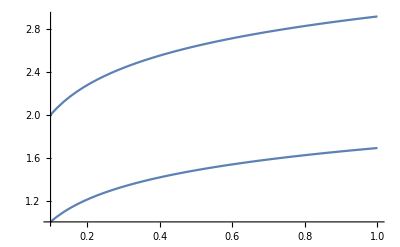

```mathematica
Plot[  {α[r] , β[r] } /. alphaBetaSol , {r,0.1,1}]
```

## Relationship Between Constants in Solution of Field Equations For Metric 1

```mathematica
Clear[alphaReplace]
alphaReplace = 
Flatten[DSolve[ eq2a , α[r],r]]
```

{α[r]→C[2]+C[1] Log[r]}

```mathematica
D[alphaReplace ,r]
D[alphaReplace ,{r,2}]
```

{α'[r]→C[1]/r}

{α''[r]→-C[1]/r^2}

```mathematica
Clear[betaReplace]
betaReplace = 
Flatten[DSolve[ eq2b , β[r],r]] /. C[1]-> C[3] /. C[2]-> C[4]
```

{β[r]→C[4]+C[3] Log[r]}

```mathematica
D[ betaReplace,r]
D[ betaReplace,{r,2}]
```

{β'[r]→C[3]/r}

{β''[r]→-C[3]/r^2}

```mathematica
eq2c
eq2c /.  D[alphaReplace ,r]
eq2c /.  D[alphaReplace ,r] /. D[ betaReplace,{r,2}]
Solve[( eq2c /.  D[alphaReplace ,r] /. D[ betaReplace,{r,2}] ) , C[1]][[2]]
```

α'[r]^2+β''[r]==0

C[1]^2/r^2+β''[r]==0

C[1]^2/r^2-C[3]/r^2==0

{C[1]→√C[3]}

## Line Element and Metric 3

```mathematica
Clear[eq3]
eq3 = 
r1^(2(𝒞/(1-𝒞))) dt1^2- r1^2 dϕ^2- K^2 r1^((2 𝒞^2)/(1-𝒞)) dr1^2- r1^(-2𝒞) dz1^2
```

-dϕ^2 r1^2-dz1^2 r1^(-2 𝒞)+dt1^2 r1^((2 𝒞)/(1-𝒞))-dr1^2 K^2 r1^((2 𝒞^2)/(1-𝒞))

```mathematica
Clear[metric3]
metric3 = 
lineToMetric[ eq3 , {dt1,dr1,dϕ,dz1}]  ;
metric3 // MatrixForm // pdConv
```

(r1^((2 𝒞)/(1-𝒞)) | 0 | 0 | 0
0 | -K^2 r1^((2 𝒞^2)/(1-𝒞)) | 0 | 0
0 | 0 | -r1^2 | 0
0 | 0 | 0 | -r1^(-2 𝒞))

## Line Element and Metric 4: Form Obtained by Levi-Civita 1919

```mathematica
Clear[eq4]
eq4 =
r2^(2𝒞) dt2^2- r2^(2(1-𝒞))dϕ^2- A^2 r2^(-2𝒞(1-𝒞))( dr2^2+ dz2^2)
```

-dϕ^2 r2^(2 (1-𝒞))+dt2^2 r2^(2 𝒞)-A^2 (dr2^2+dz2^2) r2^(-2 (1-𝒞) 𝒞)

```mathematica
Clear[metric4]
metric4 = 
lineToMetric[ eq4 , {dt2,dr2,dϕ,dz2}]  ;
metric4// MatrixForm // pdConv
```

(r2^(2 𝒞) | 0 | 0 | 0
0 | -A^2 r2^(-2 (1-𝒞) 𝒞) | 0 | 0
0 | 0 | -r2^(2 (1-𝒞)) | 0
0 | 0 | 0 | -A^2 r2^(-2 (1-𝒞) 𝒞))

```mathematica
Clear[eq4a]
eq4a = 
A == K(1-𝒞) ;
(eq4a /. Equal-> Rule)
```

A→K (1-𝒞)

```mathematica
metric4 /. (eq4a /. Equal-> Rule) // Expand // Simplify  // MatrixForm
```

(r2^(2 𝒞) | 0 | 0 | 0
0 | -K^2 r2^(2 (-1+𝒞) 𝒞) (-1+𝒞)^2 | 0 | 0
0 | 0 | -r2^(2-2 𝒞) | 0
0 | 0 | 0 | -K^2 r2^(2 (-1+𝒞) 𝒞) (-1+𝒞)^2)

## Line Element and Metric 10 From Appendix: Pulse Waves From Rosen 1954

```mathematica
(* General Form from Appendix... we'll put μ = 0 for this part *) 

Clear[lineElement10] 
lineElement10 = 
Exp[2γ-2ψ] (dt^2-dr^2 ) - r^2 Exp[-2 ψ] dϕ^2- Exp[2ψ+2μ] dz^2   /. μ-> 0
```

(-dr^2+dt^2) ⅇ^(2 γ-2 ψ)-dz^2 ⅇ^(2 ψ)-dϕ^2 ⅇ^(-2 ψ) r^2

```mathematica
lineToMetric[ lineElement10 , {dt,dr,dϕ,dz}] // MatrixForm
```

(ⅇ^(2 γ-2 ψ) | 0 | 0 | 0
0 | -ⅇ^(2 γ-2 ψ) | 0 | 0
0 | 0 | -ⅇ^(-2 ψ) r^2 | 0
0 | 0 | 0 | -ⅇ^(2 ψ))

```mathematica
Clear[rtReplace]
rtReplace = {
γ-> γ[r,t] , 
ψ-> ψ[r,t] , 
μ-> μ[r,t]
} ;
rtReplace  // TableForm
```

γ→γ[r,t]
ψ→ψ[r,t]
μ→μ[r,t]

```mathematica
Clear[metric10]
metric10 = 
lineToMetric[ lineElement10 , {dt,dr,dϕ,dz}]  /. rtReplace  ;
metric10  // MatrixForm // pdConv
```

(ⅇ^(2 γ(r,t)-2 ψ(r,t)) | 0 | 0 | 0
0 | -ⅇ^(2 γ(r,t)-2 ψ(r,t)) | 0 | 0
0 | 0 | r^2 (-ⅇ^(-2 ψ(r,t))) | 0
0 | 0 | 0 | -ⅇ^(2 ψ(r,t)))

## Tensors Calculated For Metric 10: Pulse Waves From Rosen 1954

```mathematica
Clear[input10] 
input10[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList10];
tensorList10 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList10[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList10[[2]]  = 
ChristoffelSymbol[ tensorList10[[1]] , ActWith-> Simplify] ;
tensorList10[[3]] = 
RiemannTensor[ tensorList10[[1]] , ActWithNested-> Simplify ];
tensorList10[[4]] = 
RicciTensor[ tensorList10[[1]] , ActWith-> Simplify ] ;
tensorList10[[5]] = 
RicciScalar[ tensorList10[[1]] , ActWith-> Simplify ] ;
tensorList10[[6]] = 
KretschmannScalar[ tensorList10[[1]] , ActWith-> Simplify] ;
tensorList10[[7]] = 
EinsteinTensor[ tensorList10[[1]] , ActWith-> Simplify] ; 
tensorList10[[8]] = 
WeylTensor[ tensorList10[[1]] , ActWith-> Simplify ] ;
tensorList10[[9]] = 
CottonTensor[ tensorList10[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
(* Last run took 8.27 seconds to evaluate all tensors *) 
input10[ "metric10", metric10,"Cylindrical","g^Rosen ",{t,r,ϕ,z}, "Greek"] // Timing
```

{9.34352,Null}

```mathematica
tensorList
```

{(g^static)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList[[1]] 
TensorName[tensorList[[1]]] 
TensorValues[tensorList[[1]]] // MatrixForm // pdConv
```

(g^static)_αβ^

StaticCylinder

(ⅇ^(2 α(r)) | 0 | 0 | 0
0 | -ⅇ^(2 β(r)-2 α(r)) | 0 | 0
0 | 0 | r^2 (-ⅇ^(-2 α(r))) | 0
0 | 0 | 0 | -ⅇ^(2 β(r)-2 α(r)))

```mathematica
tensorList[[2]] 
TensorName[tensorList[[2]]] 
TensorValues[tensorList[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolStaticCylinder

((0
(∂α(r))/(∂r)
0
0) | ((∂α(r))/(∂r)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(ⅇ^(4 α(r)-2 β(r)) (∂α(r))/(∂r)
0
0
0) | (0
(∂β(r))/(∂r)-(∂α(r))/(∂r)
0
0) | (0
0
r ⅇ^(-2 β(r)) (r (∂α(r))/(∂r)-1)
0) | (0
0
0
(∂α(r))/(∂r)-(∂β(r))/(∂r))
(0
0
0
0) | (0
0
1/r-(∂α(r))/(∂r)
0) | (0
1/r-(∂α(r))/(∂r)
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
(∂β(r))/(∂r)-(∂α(r))/(∂r)) | (0
0
0
0) | (0
(∂β(r))/(∂r)-(∂α(r))/(∂r)
0
0))

```mathematica
tensorList[[3]] 
TensorName[tensorList[[3]]] 
TensorValues[tensorList[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorStaticCylinder

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -ⅇ^(2 α(r)) ((∂^2 α(r))/(∂r^2)-(∂α(r))/(∂r) (∂β(r))/(∂r)+2 ((∂α(r))/(∂r))^2) | 0 | 0
ⅇ^(2 α(r)) ((∂^2 α(r))/(∂r^2)-(∂α(r))/(∂r) (∂β(r))/(∂r)+2 ((∂α(r))/(∂r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | r ⅇ^(2 α(r)-2 β(r)) (∂α(r))/(∂r) (r (∂α(r))/(∂r)-1) | 0
0 | 0 | 0 | 0
r (-ⅇ^(2 α(r)-2 β(r))) (∂α(r))/(∂r) (r (∂α(r))/(∂r)-1) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | ⅇ^(2 α(r)) (∂α(r))/(∂r) ((∂α(r))/(∂r)-(∂β(r))/(∂r))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-ⅇ^(2 α(r)) (∂α(r))/(∂r) ((∂α(r))/(∂r)-(∂β(r))/(∂r)) | 0 | 0 | 0)
(0 | ⅇ^(2 α(r)) ((∂^2 α(r))/(∂r^2)-(∂α(r))/(∂r) (∂β(r))/(∂r)+2 ((∂α(r))/(∂r))^2) | 0 | 0
-ⅇ^(2 α(r)) ((∂^2 α(r))/(∂r^2)-(∂α(r))/(∂r) (∂β(r))/(∂r)+2 ((∂α(r))/(∂r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | r ⅇ^(-2 α(r)) (-r (∂^2 α(r))/(∂r^2)+(∂α(r))/(∂r) (r (∂β(r))/(∂r)-1)-(∂β(r))/(∂r)) | 0
0 | r (-ⅇ^(-2 α(r))) (-r (∂^2 α(r))/(∂r^2)+(∂α(r))/(∂r) (r (∂β(r))/(∂r)-1)-(∂β(r))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(2 β(r)-2 α(r)) ((∂^2 β(r))/(∂r^2)-(∂^2 α(r))/(∂r^2))
0 | 0 | 0 | 0
0 | -ⅇ^(2 β(r)-2 α(r)) ((∂^2 β(r))/(∂r^2)-(∂^2 α(r))/(∂r^2)) | 0 | 0)
(0 | 0 | r (-ⅇ^(2 α(r)-2 β(r))) (∂α(r))/(∂r) (r (∂α(r))/(∂r)-1) | 0
0 | 0 | 0 | 0
r ⅇ^(2 α(r)-2 β(r)) (∂α(r))/(∂r) (r (∂α(r))/(∂r)-1) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | r (-ⅇ^(-2 α(r))) (-r (∂^2 α(r))/(∂r^2)+(∂α(r))/(∂r) (r (∂β(r))/(∂r)-1)-(∂β(r))/(∂r)) | 0
0 | r ⅇ^(-2 α(r)) (-r (∂^2 α(r))/(∂r^2)+(∂α(r))/(∂r) (r (∂β(r))/(∂r)-1)-(∂β(r))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | r ⅇ^(-2 α(r)) (r (∂α(r))/(∂r)-1) ((∂α(r))/(∂r)-(∂β(r))/(∂r))
0 | 0 | r (-ⅇ^(-2 α(r))) (r (∂α(r))/(∂r)-1) ((∂α(r))/(∂r)-(∂β(r))/(∂r)) | 0)
(0 | 0 | 0 | -ⅇ^(2 α(r)) (∂α(r))/(∂r) ((∂α(r))/(∂r)-(∂β(r))/(∂r))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
ⅇ^(2 α(r)) (∂α(r))/(∂r) ((∂α(r))/(∂r)-(∂β(r))/(∂r)) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -ⅇ^(2 β(r)-2 α(r)) ((∂^2 β(r))/(∂r^2)-(∂^2 α(r))/(∂r^2))
0 | 0 | 0 | 0
0 | ⅇ^(2 β(r)-2 α(r)) ((∂^2 β(r))/(∂r^2)-(∂^2 α(r))/(∂r^2)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | r (-ⅇ^(-2 α(r))) (r (∂α(r))/(∂r)-1) ((∂α(r))/(∂r)-(∂β(r))/(∂r))
0 | 0 | r ⅇ^(-2 α(r)) (r (∂α(r))/(∂r)-1) ((∂α(r))/(∂r)-(∂β(r))/(∂r)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[4]] 
TensorName[tensorList[[4]]] 
TensorValues[tensorList[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorStaticCylinder

((ⅇ^(4 α(r)-2 β(r)) (r (∂^2 α(r))/(∂r^2)+(∂α(r))/(∂r)))/r | 0 | 0 | 0
0 | (r (∂^2 α(r))/(∂r^2)-r (∂^2 β(r))/(∂r^2)-2 r ((∂α(r))/(∂r))^2+(∂α(r))/(∂r)+(∂β(r))/(∂r))/r | 0 | 0
0 | 0 | r ⅇ^(-2 β(r)) (r (∂^2 α(r))/(∂r^2)+(∂α(r))/(∂r)) | 0
0 | 0 | 0 | (r (∂^2 α(r))/(∂r^2)-r (∂^2 β(r))/(∂r^2)+(∂α(r))/(∂r)-(∂β(r))/(∂r))/r)

```mathematica
tensorList[[5]] 
TensorName[tensorList[[5]]] 
TensorValues[tensorList[[5]]] // MatrixForm // pdConv
```

R

RicciScalarStaticCylinder

(2 ⅇ^(2 α(r)-2 β(r)) (r ((∂^2 β(r))/(∂r^2)-(∂^2 α(r))/(∂r^2))+r ((∂α(r))/(∂r))^2-(∂α(r))/(∂r)))/r

```mathematica
tensorList[[6]] 
TensorName[tensorList[[6]]] 
TensorValues[tensorList[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarStaticCylinder

1/r^2 4 ⅇ^(4 α(r)-4 β(r)) (((∂α(r))/(∂r))^2 (4 r^2 (∂^2 α(r))/(∂r^2)+4 r^2 ((∂β(r))/(∂r))^2+2 r (∂β(r))/(∂r)+3)+2 r (∂α(r))/(∂r) (-2 r (∂^2 α(r))/(∂r^2) (∂β(r))/(∂r)+(∂^2 α(r))/(∂r^2)-2 ((∂β(r))/(∂r))^2)+2 r (∂^2 α(r))/(∂r^2) (∂β(r))/(∂r)+r^2 (-2 (∂^2 α(r))/(∂r^2) (∂^2 β(r))/(∂r^2)+3 ((∂^2 α(r))/(∂r^2))^2+((∂^2 β(r))/(∂r^2))^2)+7 r^2 ((∂α(r))/(∂r))^4-4 r ((∂α(r))/(∂r))^3 (2 r (∂β(r))/(∂r)+1)+2 ((∂β(r))/(∂r))^2)

```mathematica
tensorList[[7]] 
TensorName[tensorList[[7]]] 
TensorValues[tensorList[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorStaticCylinder

(-(ⅇ^(4 α(r)-2 β(r)) (r ((∂^2 β(r))/(∂r^2)-2 (∂^2 α(r))/(∂r^2))+r ((∂α(r))/(∂r))^2-2 (∂α(r))/(∂r)))/r | 0 | 0 | 0
0 | ((∂β(r))/(∂r))/r-((∂α(r))/(∂r))^2 | 0 | 0
0 | 0 | r^2 ⅇ^(-2 β(r)) ((∂^2 β(r))/(∂r^2)+((∂α(r))/(∂r))^2) | 0
0 | 0 | 0 | ((∂α(r))/(∂r))^2-((∂β(r))/(∂r))/r)

```mathematica
tensorList[[8]] 
TensorName[tensorList[[8]]] 
TensorValues[tensorList[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorStaticCylinder

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (ⅇ^(2 α(r)) (r ((∂^2 β(r))/(∂r^2)-4 (∂^2 α(r))/(∂r^2))+(∂α(r))/(∂r) (6 r (∂β(r))/(∂r)+2)-8 r ((∂α(r))/(∂r))^2-3 (∂β(r))/(∂r)))/(6 r) | 0 | 0
(ⅇ^(2 α(r)) (4 r (∂^2 α(r))/(∂r^2)-r (∂^2 β(r))/(∂r^2)-2 (∂α(r))/(∂r) (3 r (∂β(r))/(∂r)+1)+8 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)))/(6 r) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/3 r ⅇ^(2 α(r)-2 β(r)) (r ((∂^2 α(r))/(∂r^2)-(∂^2 β(r))/(∂r^2))+2 r ((∂α(r))/(∂r))^2-2 (∂α(r))/(∂r)) | 0
0 | 0 | 0 | 0
-1/3 r ⅇ^(2 α(r)-2 β(r)) (r ((∂^2 α(r))/(∂r^2)-(∂^2 β(r))/(∂r^2))+2 r ((∂α(r))/(∂r))^2-2 (∂α(r))/(∂r)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (ⅇ^(2 α(r)) (r (2 (∂^2 α(r))/(∂r^2)+(∂^2 β(r))/(∂r^2))+(∂α(r))/(∂r) (2-6 r (∂β(r))/(∂r))+4 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)))/(6 r)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(ⅇ^(2 α(r)) (r (2 (∂^2 α(r))/(∂r^2)+(∂^2 β(r))/(∂r^2))+(∂α(r))/(∂r) (2-6 r (∂β(r))/(∂r))+4 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)))/(6 r) | 0 | 0 | 0)
(0 | (ⅇ^(2 α(r)) (4 r (∂^2 α(r))/(∂r^2)-r (∂^2 β(r))/(∂r^2)-2 (∂α(r))/(∂r) (3 r (∂β(r))/(∂r)+1)+8 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)))/(6 r) | 0 | 0
(ⅇ^(2 α(r)) (r ((∂^2 β(r))/(∂r^2)-4 (∂^2 α(r))/(∂r^2))+(∂α(r))/(∂r) (6 r (∂β(r))/(∂r)+2)-8 r ((∂α(r))/(∂r))^2-3 (∂β(r))/(∂r)))/(6 r) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -1/6 r ⅇ^(-2 α(r)) (r (2 (∂^2 α(r))/(∂r^2)+(∂^2 β(r))/(∂r^2))+(∂α(r))/(∂r) (2-6 r (∂β(r))/(∂r))+4 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)) | 0
0 | 1/6 r ⅇ^(-2 α(r)) (r (2 (∂^2 α(r))/(∂r^2)+(∂^2 β(r))/(∂r^2))+(∂α(r))/(∂r) (2-6 r (∂β(r))/(∂r))+4 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (ⅇ^(2 β(r)-2 α(r)) (r ((∂^2 β(r))/(∂r^2)-(∂^2 α(r))/(∂r^2))-2 r ((∂α(r))/(∂r))^2+2 (∂α(r))/(∂r)))/(3 r)
0 | 0 | 0 | 0
0 | (ⅇ^(2 β(r)-2 α(r)) (r ((∂^2 α(r))/(∂r^2)-(∂^2 β(r))/(∂r^2))+2 r ((∂α(r))/(∂r))^2-2 (∂α(r))/(∂r)))/(3 r) | 0 | 0)
(0 | 0 | -1/3 r ⅇ^(2 α(r)-2 β(r)) (r ((∂^2 α(r))/(∂r^2)-(∂^2 β(r))/(∂r^2))+2 r ((∂α(r))/(∂r))^2-2 (∂α(r))/(∂r)) | 0
0 | 0 | 0 | 0
1/3 r ⅇ^(2 α(r)-2 β(r)) (r ((∂^2 α(r))/(∂r^2)-(∂^2 β(r))/(∂r^2))+2 r ((∂α(r))/(∂r))^2-2 (∂α(r))/(∂r)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 1/6 r ⅇ^(-2 α(r)) (r (2 (∂^2 α(r))/(∂r^2)+(∂^2 β(r))/(∂r^2))+(∂α(r))/(∂r) (2-6 r (∂β(r))/(∂r))+4 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)) | 0
0 | -1/6 r ⅇ^(-2 α(r)) (r (2 (∂^2 α(r))/(∂r^2)+(∂^2 β(r))/(∂r^2))+(∂α(r))/(∂r) (2-6 r (∂β(r))/(∂r))+4 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/6 r ⅇ^(-2 α(r)) (4 r (∂^2 α(r))/(∂r^2)-r (∂^2 β(r))/(∂r^2)-2 (∂α(r))/(∂r) (3 r (∂β(r))/(∂r)+1)+8 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r))
0 | 0 | -1/6 r ⅇ^(-2 α(r)) (4 r (∂^2 α(r))/(∂r^2)-r (∂^2 β(r))/(∂r^2)-2 (∂α(r))/(∂r) (3 r (∂β(r))/(∂r)+1)+8 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)) | 0)
(0 | 0 | 0 | -(ⅇ^(2 α(r)) (r (2 (∂^2 α(r))/(∂r^2)+(∂^2 β(r))/(∂r^2))+(∂α(r))/(∂r) (2-6 r (∂β(r))/(∂r))+4 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)))/(6 r)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(ⅇ^(2 α(r)) (r (2 (∂^2 α(r))/(∂r^2)+(∂^2 β(r))/(∂r^2))+(∂α(r))/(∂r) (2-6 r (∂β(r))/(∂r))+4 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)))/(6 r) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (ⅇ^(2 β(r)-2 α(r)) (r ((∂^2 α(r))/(∂r^2)-(∂^2 β(r))/(∂r^2))+2 r ((∂α(r))/(∂r))^2-2 (∂α(r))/(∂r)))/(3 r)
0 | 0 | 0 | 0
0 | (ⅇ^(2 β(r)-2 α(r)) (r ((∂^2 β(r))/(∂r^2)-(∂^2 α(r))/(∂r^2))-2 r ((∂α(r))/(∂r))^2+2 (∂α(r))/(∂r)))/(3 r) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1/6 r ⅇ^(-2 α(r)) (4 r (∂^2 α(r))/(∂r^2)-r (∂^2 β(r))/(∂r^2)-2 (∂α(r))/(∂r) (3 r (∂β(r))/(∂r)+1)+8 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r))
0 | 0 | 1/6 r ⅇ^(-2 α(r)) (4 r (∂^2 α(r))/(∂r^2)-r (∂^2 β(r))/(∂r^2)-2 (∂α(r))/(∂r) (3 r (∂β(r))/(∂r)+1)+8 r ((∂α(r))/(∂r))^2+3 (∂β(r))/(∂r)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[9]] 
TensorName[tensorList[[9]]] 
TensorValues[tensorList[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorStaticCylinder

((0
-(ⅇ^(4 α(r)-2 β(r)) ((∂α(r))/(∂r) (-12 r^2 (∂^2 α(r))/(∂r^2)+5 r^2 (∂^2 β(r))/(∂r^2)+5 r (∂β(r))/(∂r)+4)+8 r^2 ((∂α(r))/(∂r))^3+r ((∂^2 α(r))/(∂r^2) (8 r (∂β(r))/(∂r)-4)+r (-4 (∂^3 α(r))/(∂r^3)+(∂^3 β(r))/(∂r^3)-2 (∂β(r))/(∂r) (∂^2 β(r))/(∂r^2)))-2 r ((∂α(r))/(∂r))^2 (r (∂β(r))/(∂r)+7)))/(3 r^2)
0
0) | ((ⅇ^(4 α(r)-2 β(r)) ((∂α(r))/(∂r) (-12 r^2 (∂^2 α(r))/(∂r^2)+5 r^2 (∂^2 β(r))/(∂r^2)+5 r (∂β(r))/(∂r)+4)+8 r^2 ((∂α(r))/(∂r))^3+r ((∂^2 α(r))/(∂r^2) (8 r (∂β(r))/(∂r)-4)+r (-4 (∂^3 α(r))/(∂r^3)+(∂^3 β(r))/(∂r^3)-2 (∂β(r))/(∂r) (∂^2 β(r))/(∂r^2)))-2 r ((∂α(r))/(∂r))^2 (r (∂β(r))/(∂r)+7)))/(3 r^2)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
1/3 ⅇ^(-2 β(r)) ((∂α(r))/(∂r) (-6 r^2 (∂^2 α(r))/(∂r^2)+r^2 (∂^2 β(r))/(∂r^2)+r (∂β(r))/(∂r)+2)+(∂β(r))/(∂r) (4 r^2 (∂^2 α(r))/(∂r^2)+2 r^2 (∂^2 β(r))/(∂r^2)+3)+4 r^2 ((∂α(r))/(∂r))^3-r (2 r (∂^3 α(r))/(∂r^3)+r (∂^3 β(r))/(∂r^3)+2 (∂^2 α(r))/(∂r^2)+3 (∂^2 β(r))/(∂r^2))+2 r ((∂α(r))/(∂r))^2 (r (∂β(r))/(∂r)-5))
0) | (0
1/3 ⅇ^(-2 β(r)) ((∂α(r))/(∂r) (6 r^2 (∂^2 α(r))/(∂r^2)-r^2 (∂^2 β(r))/(∂r^2)-r (∂β(r))/(∂r)-2)-(∂β(r))/(∂r) (4 r^2 (∂^2 α(r))/(∂r^2)+2 r^2 (∂^2 β(r))/(∂r^2)+3)-4 r^2 ((∂α(r))/(∂r))^3+r (2 r (∂^3 α(r))/(∂r^3)+r (∂^3 β(r))/(∂r^3)+2 (∂^2 α(r))/(∂r^2)+3 (∂^2 β(r))/(∂r^2))-2 r ((∂α(r))/(∂r))^2 (r (∂β(r))/(∂r)-5))
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
((∂α(r))/(∂r) (-6 r^2 (∂^2 α(r))/(∂r^2)+4 r^2 (∂^2 β(r))/(∂r^2)+4 r (∂β(r))/(∂r)+2)+(∂β(r))/(∂r) (4 r^2 (∂^2 α(r))/(∂r^2)-4 r^2 (∂^2 β(r))/(∂r^2)-3)+4 r^2 ((∂α(r))/(∂r))^3+r (-2 r (∂^3 α(r))/(∂r^3)+2 r (∂^3 β(r))/(∂r^3)-2 (∂^2 α(r))/(∂r^2)+3 (∂^2 β(r))/(∂r^2))-4 r ((∂α(r))/(∂r))^2 (r (∂β(r))/(∂r)+1))/(3 r^2)) | (0
0
0
0) | (0
((∂α(r))/(∂r) (6 r^2 (∂^2 α(r))/(∂r^2)-4 r^2 (∂^2 β(r))/(∂r^2)-4 r (∂β(r))/(∂r)-2)+(∂β(r))/(∂r) (-4 r^2 (∂^2 α(r))/(∂r^2)+4 r^2 (∂^2 β(r))/(∂r^2)+3)-4 r^2 ((∂α(r))/(∂r))^3+r (2 r (∂^3 α(r))/(∂r^3)-2 r (∂^3 β(r))/(∂r^3)+2 (∂^2 α(r))/(∂r^2)-3 (∂^2 β(r))/(∂r^2))+4 r ((∂α(r))/(∂r))^2 (r (∂β(r))/(∂r)+1))/(3 r^2)
0
0))

## Derivation of Field Equations For Metric 10: Pulse Waves From Rosen 1954

```mathematica
Clear[nonzeroRicci10]
nonzeroRicci10 = { 
TensorValues[tensorList10[[4]]][[1,1]] , 
TensorValues[tensorList10[[4]]][[1,2]] , 
TensorValues[tensorList10[[4]]][[2,2]] , 
TensorValues[tensorList10[[4]]][[3,3]] , 
TensorValues[tensorList10[[4]]][[4,4]]
} ;
nonzeroRicci10  // TableForm  // pdConv
```

(∂^2 γ(r,t))/(∂r^2)-(∂^2 ψ(r,t))/(∂r^2)-(∂^2 γ(r,t))/(∂t^2)+(∂^2 ψ(r,t))/(∂t^2)+((∂γ(r,t))/(∂r))/r-2 ((∂ψ(r,t))/(∂t))^2-((∂ψ(r,t))/(∂r))/r
((∂γ(r,t))/(∂t))/r-2 (∂ψ(r,t))/(∂r) (∂ψ(r,t))/(∂t)
-(∂^2 γ(r,t))/(∂r^2)+(∂^2 ψ(r,t))/(∂r^2)+(∂^2 γ(r,t))/(∂t^2)-(∂^2 ψ(r,t))/(∂t^2)+((∂γ(r,t))/(∂r))/r-2 ((∂ψ(r,t))/(∂r))^2+((∂ψ(r,t))/(∂r))/r
r ⅇ^(-2 γ(r,t)) (r (∂^2 ψ(r,t))/(∂r^2)-r (∂^2 ψ(r,t))/(∂t^2)+(∂ψ(r,t))/(∂r))
(ⅇ^(4 ψ(r,t)-2 γ(r,t)) (-r (∂^2 ψ(r,t))/(∂r^2)+r (∂^2 ψ(r,t))/(∂t^2)-(∂ψ(r,t))/(∂r)))/r

```mathematica
Clear[nonzeroEinstein10]
nonzeroEinstein10 = { 
TensorValues[tensorList10[[7]]][[1,1]] , 
TensorValues[tensorList10[[7]]][[1,2]] , 
TensorValues[tensorList10[[7]]][[2,2]] , 
TensorValues[tensorList10[[7]]][[3,3]] , 
TensorValues[tensorList10[[7]]][[4,4]]
} ;
nonzeroEinstein10  // TableForm  // pdConv
```

((∂γ(r,t))/(∂r))/r-((∂ψ(r,t))/(∂r))^2-((∂ψ(r,t))/(∂t))^2
((∂γ(r,t))/(∂t))/r-2 (∂ψ(r,t))/(∂r) (∂ψ(r,t))/(∂t)
((∂γ(r,t))/(∂r))/r-((∂ψ(r,t))/(∂r))^2-((∂ψ(r,t))/(∂t))^2
r^2 (-ⅇ^(-2 γ(r,t))) (-(∂^2 γ(r,t))/(∂r^2)+(∂^2 γ(r,t))/(∂t^2)-((∂ψ(r,t))/(∂r))^2+((∂ψ(r,t))/(∂t))^2)
(ⅇ^(4 ψ(r,t)-2 γ(r,t)) (r (∂^2 γ(r,t))/(∂r^2)-2 r (∂^2 ψ(r,t))/(∂r^2)-r (∂^2 γ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)+r ((∂ψ(r,t))/(∂r))^2-2 (∂ψ(r,t))/(∂r)-r ((∂ψ(r,t))/(∂t))^2))/r

```mathematica
Clear[eq11]
eq11 = 
Expand[(1/r)TensorValues[tensorList10[[4]]] [[3,3]][[3]]] == 0  ;
eq11 // pdConv
```

(∂^2 ψ(r,t))/(∂r^2)-(∂^2 ψ(r,t))/(∂t^2)+((∂ψ(r,t))/(∂r))/r==0

```mathematica
Clear[eq12a]
eq12a = 
Flatten[Solve[nonzeroEinstein10[[1]]== 0 , Derivative[1,0][γ][r,t]]][[1]] /. Rule-> Equal   ;
eq12a // pdConv
```

(∂γ(r,t))/(∂r)==r (((∂ψ(r,t))/(∂r))^2+((∂ψ(r,t))/(∂t))^2)

```mathematica
Clear[eq12b]
eq12b = 
Flatten[Solve[nonzeroEinstein10[[2]]==0 ,Derivative[0,1][γ][r,t]]][[1]] /. Rule-> Equal   ;
eq12b// pdConv
```

(∂γ(r,t))/(∂t)==2 r (∂ψ(r,t))/(∂r) (∂ψ(r,t))/(∂t)

```mathematica
Clear[eq12]
eq12 = { 
eq12a , 
eq12b
} ;
eq12 // TableForm // pdConv
```

(∂γ(r,t))/(∂r)==r (((∂ψ(r,t))/(∂r))^2+((∂ψ(r,t))/(∂t))^2)
(∂γ(r,t))/(∂t)==2 r (∂ψ(r,t))/(∂r) (∂ψ(r,t))/(∂t)

## Radial Geodesics For Metric 10 From Euler Lagrange Equations (cut and paste this somewhere else)

```mathematica
Clear[q]
q = {
t[s],r[s],ϕ[s] , z[s]
} ;
q // TableForm
```

t[s]
r[s]
ϕ[s]
z[s]

```mathematica
Clear[rtsReplace]
rtsReplace = {
γ-> γ[r[s],t[s]] , 
ψ-> ψ[r[s],t[s]] , 
μ-> μ[r[s],t[s]]
} ;
rtsReplace  // TableForm
```

γ→γ[r[s],t[s]]
ψ→ψ[r[s],t[s]]
μ→μ[r[s],t[s]]

```mathematica
Clear[ℒ]
ℒ = 
Exp[2(γ-ψ)] ( (D[q[[1]], s])^2-  (D[q[[2]], s])^2) -r[s]^2 Exp[-2ψ] (D[q[[3]], s])^2 - Exp[2ψ]  (D[q[[4]], s])^2 /. rtsReplace  ;
ℒ // pdConv
```

(((∂t(s))/(∂s))^2-((∂r(s))/(∂s))^2) exp(2 (γ(r(s),t(s))-ψ(r(s),t(s))))+((∂z(s))/(∂s))^2 (-ⅇ^(2 ψ(r(s),t(s))))-(r(s))^2 ((∂ϕ(s))/(∂s))^2 ⅇ^(-2 ψ(r(s),t(s)))

```mathematica
Clear[eulerEquations]
eulerEquations = 
EulerEquations[ ℒ , q , s] ;
eulerEquations // TableForm // pdConv
```

-2 ⅇ^(-2 ψ(r(s),t(s))) ((∂^2 t(s))/(∂s^2) ⅇ^(2 γ(r(s),t(s)))+((∂r(s))/(∂s))^2 ⅇ^(2 γ(r(s),t(s))) ((∂γ(r(s),t(s)))/(∂t(s))-(∂ψ(r(s),t(s)))/(∂t(s)))+2 (∂r(s))/(∂s) (∂t(s))/(∂s) ⅇ^(2 γ(r(s),t(s))) ((∂γ(r(s),t(s)))/(∂r(s))-(∂ψ(r(s),t(s)))/(∂r(s)))-((∂t(s))/(∂s))^2 ⅇ^(2 γ(r(s),t(s))) (∂ψ(r(s),t(s)))/(∂t(s))+((∂t(s))/(∂s))^2 ⅇ^(2 γ(r(s),t(s))) (∂γ(r(s),t(s)))/(∂t(s))+((∂z(s))/(∂s))^2 ⅇ^(4 ψ(r(s),t(s))) (∂ψ(r(s),t(s)))/(∂t(s))-(r(s))^2 ((∂ϕ(s))/(∂s))^2 (∂ψ(r(s),t(s)))/(∂t(s)))==0
2 ⅇ^(-2 ψ(r(s),t(s))) ((∂^2 r(s))/(∂s^2) ⅇ^(2 γ(r(s),t(s)))-((∂r(s))/(∂s))^2 ⅇ^(2 γ(r(s),t(s))) (∂ψ(r(s),t(s)))/(∂r(s))-2 (∂r(s))/(∂s) (∂t(s))/(∂s) ⅇ^(2 γ(r(s),t(s))) (∂ψ(r(s),t(s)))/(∂t(s))-((∂t(s))/(∂s))^2 ⅇ^(2 γ(r(s),t(s))) (∂ψ(r(s),t(s)))/(∂r(s))+((∂r(s))/(∂s))^2 ⅇ^(2 γ(r(s),t(s))) (∂γ(r(s),t(s)))/(∂r(s))+2 (∂r(s))/(∂s) (∂t(s))/(∂s) ⅇ^(2 γ(r(s),t(s))) (∂γ(r(s),t(s)))/(∂t(s))+((∂t(s))/(∂s))^2 ⅇ^(2 γ(r(s),t(s))) (∂γ(r(s),t(s)))/(∂r(s))-((∂z(s))/(∂s))^2 ⅇ^(4 ψ(r(s),t(s))) (∂ψ(r(s),t(s)))/(∂r(s))+(r(s))^2 ((∂ϕ(s))/(∂s))^2 (∂ψ(r(s),t(s)))/(∂r(s))-r(s) ((∂ϕ(s))/(∂s))^2)==0
2 r(s) ⅇ^(-2 ψ(r(s),t(s))) (r(s) ((∂^2 ϕ(s))/(∂s^2)-2 (∂t(s))/(∂s) (∂ϕ(s))/(∂s) (∂ψ(r(s),t(s)))/(∂t(s)))-2 (∂r(s))/(∂s) (∂ϕ(s))/(∂s) (r(s) (∂ψ(r(s),t(s)))/(∂r(s))-1))==0
2 ⅇ^(2 ψ(r(s),t(s))) (2 (∂z(s))/(∂s) ((∂r(s))/(∂s) (∂ψ(r(s),t(s)))/(∂r(s))+(∂t(s))/(∂s) (∂ψ(r(s),t(s)))/(∂t(s)))+(∂^2 z(s))/(∂s^2))==0

```mathematica
FirstIntegrals[ℒ,q,s] // TableForm // pdConv
```

FirstIntegral(ϕ)→2 (r(s))^2 (∂ϕ(s))/(∂s) ⅇ^(-2 ψ(r(s),t(s)))
FirstIntegral(z)→2 (∂z(s))/(∂s) ⅇ^(2 ψ(r(s),t(s)))
FirstIntegral(s)→-ⅇ^(-2 ψ(r(s),t(s))) (((∂r(s))/(∂s))^2 ⅇ^(2 γ(r(s),t(s)))-((∂t(s))/(∂s))^2 ⅇ^(2 γ(r(s),t(s)))+((∂z(s))/(∂s))^2 ⅇ^(4 ψ(r(s),t(s)))+(r(s))^2 ((∂ϕ(s))/(∂s))^2)

```mathematica
Clear[eq22c]
eq22c = { 
FirstIntegrals[ℒ,q,s][[1]][[2]][[4]] -> 0  , 
FirstIntegrals[ℒ,q,s][[2]][[2]][[3]] -> 0 
} ;
eq22c // TableForm
```

ϕ'[s]→0
z'[s]→0

```mathematica
Clear[eq23]
eq23 = 
( FirstIntegrals[ℒ,q,s][[3]][[2]]/. eq22c   // Simplify ) == 1 ;
eq23  // pdConv
```

(((∂t(s))/(∂s))^2-((∂r(s))/(∂s))^2) exp(2 γ(r(s),t(s))-2 ψ(r(s),t(s)))==1

```mathematica
Clear[eq22a]
eq22a = 
(eulerEquations[[2]][[1]][[3]]  /. eq22c  // Simplify)[[2]]  ==0 ;
eq22a// pdConv
```

((∂r(s))/(∂s))^2 ((∂γ(r(s),t(s)))/(∂r(s))-(∂ψ(r(s),t(s)))/(∂r(s)))+2 (∂r(s))/(∂s) (∂t(s))/(∂s) ((∂γ(r(s),t(s)))/(∂t(s))-(∂ψ(r(s),t(s)))/(∂t(s)))+((∂t(s))/(∂s))^2 ((∂γ(r(s),t(s)))/(∂r(s))-(∂ψ(r(s),t(s)))/(∂r(s)))+(∂^2 r(s))/(∂s^2)==0

```mathematica
Clear[eq22b]
eq22b = 
(eulerEquations[[1]][[1]][[3]]/. eq22c // Simplify)[[2]] == 0 // pdConv
```

((∂r(s))/(∂s))^2 ((∂γ(r(s),t(s)))/(∂t(s))-(∂ψ(r(s),t(s)))/(∂t(s)))+2 (∂r(s))/(∂s) (∂t(s))/(∂s) ((∂γ(r(s),t(s)))/(∂r(s))-(∂ψ(r(s),t(s)))/(∂r(s)))+((∂t(s))/(∂s))^2 ((∂γ(r(s),t(s)))/(∂t(s))-(∂ψ(r(s),t(s)))/(∂t(s)))+(∂^2 t(s))/(∂s^2)==0

```mathematica
Clear[eq22]
eq22 = { 
eq22a,eq22b,eq22c
}  // Flatten ;
eq22 // TableForm // pdConv
```

((∂r(s))/(∂s))^2 ((∂γ(r(s),t(s)))/(∂r(s))-(∂ψ(r(s),t(s)))/(∂r(s)))+2 (∂r(s))/(∂s) (∂t(s))/(∂s) ((∂γ(r(s),t(s)))/(∂t(s))-(∂ψ(r(s),t(s)))/(∂t(s)))+((∂t(s))/(∂s))^2 ((∂γ(r(s),t(s)))/(∂r(s))-(∂ψ(r(s),t(s)))/(∂r(s)))+(∂^2 r(s))/(∂s^2)==0
((∂r(s))/(∂s))^2 ((∂γ(r(s),t(s)))/(∂t(s))-(∂ψ(r(s),t(s)))/(∂t(s)))+2 (∂r(s))/(∂s) (∂t(s))/(∂s) ((∂γ(r(s),t(s)))/(∂r(s))-(∂ψ(r(s),t(s)))/(∂r(s)))+((∂t(s))/(∂s))^2 ((∂γ(r(s),t(s)))/(∂t(s))-(∂ψ(r(s),t(s)))/(∂t(s)))+(∂^2 t(s))/(∂s^2)==0
(∂ϕ(s))/(∂s)→0
(∂z(s))/(∂s)→0

## Solution to Equation 11 by Separation of Variables

```mathematica
Clear[psiReplace]
psiReplace = 
ψ[r,t]-> f[r] g[t]
```

ψ[r,t]→f[r] g[t]

```mathematica
D[ psiReplace , r] // pdConv
```

(∂ψ(r,t))/(∂r)→g(t) (∂f(r))/(∂r)

```mathematica
D[ psiReplace , {r,2}] // pdConv
```

(∂^2 ψ(r,t))/(∂r^2)→g(t) (∂^2 f(r))/(∂r^2)

```mathematica
D[ psiReplace , {t,2}] // pdConv
```

(∂^2 ψ(r,t))/(∂t^2)→f(r) (∂^2 g(t))/(∂t^2)

```mathematica
eq11[[1]] // pdConv
eq11[[1]] /. D[ psiReplace , r] // pdConv
eq11[[1]] /. D[ psiReplace , r] /. D[ psiReplace , {r,2}]// pdConv
eq11[[1]] /. D[ psiReplace , r] /. D[ psiReplace , {r,2}]/. D[ psiReplace , {t,2}] // pdConv
```

(∂^2 ψ(r,t))/(∂r^2)-(∂^2 ψ(r,t))/(∂t^2)+((∂ψ(r,t))/(∂r))/r

(∂^2 ψ(r,t))/(∂r^2)-(∂^2 ψ(r,t))/(∂t^2)+(g(t) (∂f(r))/(∂r))/r

-(∂^2 ψ(r,t))/(∂t^2)+g(t) (∂^2 f(r))/(∂r^2)+(g(t) (∂f(r))/(∂r))/r

g(t) (∂^2 f(r))/(∂r^2)+f(r) (-(∂^2 g(t))/(∂t^2))+(g(t) (∂f(r))/(∂r))/r

```mathematica
(* separation of variables *) 

Clear[sov] 
sov = 
(1/ψ[r,t]/. psiReplace)* ( eq11[[1]] /. D[ psiReplace , r] /. D[ psiReplace , {r,2}]/. D[ psiReplace , {t,2}] ) // Expand
```

f'[r]/(r f[r])+f''[r]/f[r]-g''[t]/g[t]

```mathematica
Clear[gODE]
gODE = 
Select[ sov , (!FreeQ[#,t])&] == ω^2
```

-g''[t]/g[t]==ω^2

```mathematica
Clear[gReplace]
gReplace = 
Flatten[DSolve[ gODE , g[t],t]][[1]] (* Fix these constants later *)
```

g[t]→C[1] Cos[t ω]+C[2] Sin[t ω]

```mathematica
Clear[fODE]
fODE = 
Select[ sov , (!FreeQ[#,r])&] == -ω^2
```

f'[r]/(r f[r])+f''[r]/f[r]==-ω^2

```mathematica
Clear[fReplace]
fReplace = 
Flatten[DSolve[ fODE , f[r],r]][[1]]  /. C[1]-> C[3] /. C[2]-> C[4] (* Fix these constants later *)
```

f[r]→BesselJ[0,r ω] C[3]+BesselY[0,r ω] C[4]

```mathematica
ψ[r,t]
ψ[r,t] /. psiReplace
ψ[r,t] /. psiReplace /. fReplace

Clear[psiSolution]
psiSolution = 
ψ[r,t]-> ( ψ[r,t] /. psiReplace /. fReplace /. gReplace  )
```

ψ[r,t]

f[r] g[t]

(BesselJ[0,r ω] C[3]+BesselY[0,r ω] C[4]) g[t]

ψ[r,t]→(BesselJ[0,r ω] C[3]+BesselY[0,r ω] C[4]) (C[1] Cos[t ω]+C[2] Sin[t ω])

```mathematica
(* We'll use this in section 6 on periodic waves and it looks like I've already done it *) 

Clear[eq33a]
eq33a = 
ψ[r,t]->( Expand[psiSolution[[2]]][[1]] /. C[3]-> 1 /. C[1]-> A) +( Expand[psiSolution[[2]]][[4]]  /. C[4]-> 1 /. C[2]-> A )
```

ψ[r,t]→A BesselJ[0,r ω] Cos[t ω]+A BesselY[0,r ω] Sin[t ω]

## Solution To Equation 12 by Using Solution To Equation 11

```mathematica
eq12a  // pdConv
D[psiSolution,t] // pdConv
D[psiSolution,r] // pdConv
```

(∂γ(r,t))/(∂r)==r (((∂ψ(r,t))/(∂r))^2+((∂ψ(r,t))/(∂t))^2)

(∂ψ(r,t))/(∂t)→(3 0r ω+4 0r ω) (2 ω cos(t ω)-1 ω sin(t ω))

(∂ψ(r,t))/(∂r)→(3 (-ω) 1r ω-4 ω 1r ω) (1 cos(t ω)+2 sin(t ω))

```mathematica
eq12a // pdConv
eq12a  //.  D[psiSolution,t] // pdConv
eq12a  //.  D[psiSolution,t]   //.  D[psiSolution,r] // pdConv
```

(∂γ(r,t))/(∂r)==r (((∂ψ(r,t))/(∂r))^2+((∂ψ(r,t))/(∂t))^2)

(∂γ(r,t))/(∂r)==r (((∂ψ(r,t))/(∂r))^2+(3 0r ω+4 0r ω)^2 (2 ω cos(t ω)-1 ω sin(t ω))^2)

(∂γ(r,t))/(∂r)==r ((3 0r ω+4 0r ω)^2 (2 ω cos(t ω)-1 ω sin(t ω))^2+(3 (-ω) 1r ω-4 ω 1r ω)^2 (1 cos(t ω)+2 sin(t ω))^2)

```mathematica
Clear[gammaSolutionR]
gammaSolutionR = 
Flatten[DSolve[ (eq12a  //.  D[psiSolution,t]   //.  D[psiSolution,r]) , γ[r,t],r]] ;
gammaSolutionR  // pdConv
```

{γ(r,t)→5-1/4 r^2 ω^2 (-(4 4 3 (1 cos(t ω)+2 sin(t ω))^2 G_(3,5)^(2,2)(r ω,1/2|0,1/2,-1/2
0,1,-1,-1,-1/2))/(√π)-2 4^2 (0r ω)^2 (2 cos(t ω)-1 sin(t ω))^2-4 4 3 1r ω 1r ω (2 cos(t ω)-1 sin(t ω))^2+4 0r ω (2 4 2r ω (1 cos(t ω)+2 sin(t ω))^2-4 3 0r ω (2 cos(t ω)-1 sin(t ω))^2)-2 (3^2 0r ω (0r ω (2 cos(t ω)-1 sin(t ω))^2-2r ω (1 cos(t ω)+2 sin(t ω))^2)+(1^2+2^2) 4^2 (1r ω)^2)-2 (1^2+2^2) 3^2 (1r ω)^2)}

```mathematica
eq12b // pdConv
eq12b  //.  D[psiSolution,t] // pdConv
eq12b  //.  D[psiSolution,t]   //.  D[psiSolution,r] // pdConv
```

(∂γ(r,t))/(∂t)==2 r (∂ψ(r,t))/(∂r) (∂ψ(r,t))/(∂t)

(∂γ(r,t))/(∂t)==2 r (∂ψ(r,t))/(∂r) (3 0r ω+4 0r ω) (2 ω cos(t ω)-1 ω sin(t ω))

(∂γ(r,t))/(∂t)==2 r (3 0r ω+4 0r ω) (3 (-ω) 1r ω-4 ω 1r ω) (2 ω cos(t ω)-1 ω sin(t ω)) (1 cos(t ω)+2 sin(t ω))

```mathematica
Clear[gammaSolutionT]
gammaSolutionT = 
Flatten[DSolve[ ( eq12b  //.  D[psiSolution,t]   //.  D[psiSolution,r]) , γ[r,t] , t]] ;
gammaSolutionT  // pdConv
```

{γ(r,t)→r ω^2 (3 0r ω+4 0r ω) (3 1r ω+4 1r ω) (-(1^2 cos(2 t ω))/(2 ω)+(2^2 cos(2 t ω))/(2 ω)-(2 1 sin(2 t ω))/ω)+5}

```mathematica
Clear[eq18]
eq18 = 
eq12 /. γ-> η /. ψ-> λ ;
eq18 // TableForm // pdConv
```

(∂η(r,t))/(∂r)==r (((∂λ(r,t))/(∂r))^2+((∂λ(r,t))/(∂t))^2)
(∂η(r,t))/(∂t)==2 r (∂λ(r,t))/(∂r) (∂λ(r,t))/(∂t)

## Line Element and Metric 25

```mathematica
(* Use [esc]scr[esc] for 𝓇 *) 

Clear[eq25]  
eq25 = 
Exp[2γ-2ψ] ( dt^2- d𝓇^2) - 𝓇^2 Exp[-2ψ] dϕ^2- Exp[2ψ+2μ] dz^2
```

(dt^2-d𝓇^2) ⅇ^(2 γ-2 ψ)-dz^2 ⅇ^(2 μ+2 ψ)-dϕ^2 ⅇ^(-2 ψ) 𝓇^2

```mathematica
lineToMetric[ eq25 , {dt,d𝓇,dϕ,dz}] // MatrixForm
```

(ⅇ^(2 γ-2 ψ) | 0 | 0 | 0
0 | -ⅇ^(2 γ-2 ψ) | 0 | 0
0 | 0 | -ⅇ^(-2 ψ) 𝓇^2 | 0
0 | 0 | 0 | -ⅇ^(2 μ+2 ψ))

```mathematica
Clear[eq25a]
eq25a = { 
γ-> γ[𝓇,t] , 
ψ-> ψ[𝓇,t],
μ-> μ[𝓇,t] 
} ;
eq25a // TableForm
```

γ→γ[𝓇,t]
ψ→ψ[𝓇,t]
μ→μ[𝓇,t]

```mathematica
Clear[metric25]
metric25 = 
lineToMetric[ eq25 , {dt,d𝓇,dϕ,dz}] /. eq25a  ;
metric25// MatrixForm // pdConv
```

(ⅇ^(2 γ(𝓇,t)-2 ψ(𝓇,t)) | 0 | 0 | 0
0 | -ⅇ^(2 γ(𝓇,t)-2 ψ(𝓇,t)) | 0 | 0
0 | 0 | 𝓇^2 (-ⅇ^(-2 ψ(𝓇,t))) | 0
0 | 0 | 0 | -ⅇ^(2 μ(𝓇,t)+2 ψ(𝓇,t)))

## Tensors Calculated For Metric 25

```mathematica
Clear[input25] 
input25[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList25];
tensorList25 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList25[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList25[[2]]  = 
ChristoffelSymbol[ tensorList25[[1]] , ActWith-> Simplify] ;
tensorList25[[3]] = 
RiemannTensor[ tensorList25[[1]] , ActWithNested-> Simplify ];
tensorList25[[4]] = 
RicciTensor[ tensorList25[[1]] , ActWith-> Simplify ] ;
tensorList25[[5]] = 
RicciScalar[ tensorList25[[1]] , ActWith-> Simplify ] ;
tensorList25[[6]] = 
KretschmannScalar[ tensorList25[[1]] , ActWith-> Simplify] ; 
tensorList25[[7]] = 
EinsteinTensor[ tensorList25[[1]] , ActWith-> Simplify] ;  
tensorList25[[8]] = 
WeylTensor[ tensorList25[[1]] , ActWith-> Simplify ] ;
 tensorList25[[9]] = 
CottonTensor[ tensorList25[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
(* Last timing took 33.29 for all tensors *)
input25[ "metric25", metric25, "ModelSource","g^source",{t,𝓇,ϕ,z}, "Greek"] // Timing
```

{18.0238,Null}

```mathematica
tensorList25
```

{(g^source)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList25[[1]] 
TensorName[tensorList25[[1]]] 
TensorValues[tensorList25[[1]]] // MatrixForm // pdConv
```

(g^source)_αβ^

ModelSource

(ⅇ^(2 γ(𝓇,t)-2 ψ(𝓇,t)) | 0 | 0 | 0
0 | -ⅇ^(2 γ(𝓇,t)-2 ψ(𝓇,t)) | 0 | 0
0 | 0 | 𝓇^2 (-ⅇ^(-2 ψ(𝓇,t))) | 0
0 | 0 | 0 | -ⅇ^(2 μ(𝓇,t)+2 ψ(𝓇,t)))

```mathematica
tensorList25[[2]] 
TensorName[tensorList25[[2]]] 
TensorValues[tensorList25[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolModelSource

(((∂γ(𝓇,t))/(∂t)-(∂ψ(𝓇,t))/(∂t)
(∂γ(𝓇,t))/(∂𝓇)-(∂ψ(𝓇,t))/(∂𝓇)
0
0) | ((∂γ(𝓇,t))/(∂𝓇)-(∂ψ(𝓇,t))/(∂𝓇)
(∂γ(𝓇,t))/(∂t)-(∂ψ(𝓇,t))/(∂t)
0
0) | (0
0
𝓇^2 (-ⅇ^(-2 γ(𝓇,t))) (∂ψ(𝓇,t))/(∂t)
0) | (0
0
0
((∂μ(𝓇,t))/(∂t)+(∂ψ(𝓇,t))/(∂t)) exp(-2 γ(𝓇,t)+2 μ(𝓇,t)+4 ψ(𝓇,t)))
((∂γ(𝓇,t))/(∂𝓇)-(∂ψ(𝓇,t))/(∂𝓇)
(∂γ(𝓇,t))/(∂t)-(∂ψ(𝓇,t))/(∂t)
0
0) | ((∂γ(𝓇,t))/(∂t)-(∂ψ(𝓇,t))/(∂t)
(∂γ(𝓇,t))/(∂𝓇)-(∂ψ(𝓇,t))/(∂𝓇)
0
0) | (0
0
𝓇 ⅇ^(-2 γ(𝓇,t)) (𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)
0) | (0
0
0
((∂μ(𝓇,t))/(∂𝓇)+(∂ψ(𝓇,t))/(∂𝓇)) (-exp(-2 γ(𝓇,t)+2 μ(𝓇,t)+4 ψ(𝓇,t))))
(0
0
-(∂ψ(𝓇,t))/(∂t)
0) | (0
0
1/𝓇-(∂ψ(𝓇,t))/(∂𝓇)
0) | (-(∂ψ(𝓇,t))/(∂t)
1/𝓇-(∂ψ(𝓇,t))/(∂𝓇)
0
0) | (0
0
0
0)
(0
0
0
(∂μ(𝓇,t))/(∂t)+(∂ψ(𝓇,t))/(∂t)) | (0
0
0
(∂μ(𝓇,t))/(∂𝓇)+(∂ψ(𝓇,t))/(∂𝓇)) | (0
0
0
0) | ((∂μ(𝓇,t))/(∂t)+(∂ψ(𝓇,t))/(∂t)
(∂μ(𝓇,t))/(∂𝓇)+(∂ψ(𝓇,t))/(∂𝓇)
0
0))

```mathematica
tensorList25[[3]] 
TensorName[tensorList25[[3]]] 
TensorValues[tensorList25[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorModelSource

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | ⅇ^(2 γ(𝓇,t)-2 ψ(𝓇,t)) ((∂^2 γ(𝓇,t))/(∂t^2)-(∂^2 ψ(𝓇,t))/(∂t^2)-(∂^2 γ(𝓇,t))/(∂𝓇^2)+(∂^2 ψ(𝓇,t))/(∂𝓇^2)) | 0 | 0
-ⅇ^(2 γ(𝓇,t)-2 ψ(𝓇,t)) ((∂^2 γ(𝓇,t))/(∂t^2)-(∂^2 ψ(𝓇,t))/(∂t^2)-(∂^2 γ(𝓇,t))/(∂𝓇^2)+(∂^2 ψ(𝓇,t))/(∂𝓇^2)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 𝓇 ⅇ^(-2 ψ(𝓇,t)) (-𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+𝓇 (∂γ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+(𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1) ((∂γ(𝓇,t))/(∂𝓇)-(∂ψ(𝓇,t))/(∂𝓇))) | 0
0 | 0 | 𝓇 ⅇ^(-2 ψ(𝓇,t)) (-𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+𝓇 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂ψ(𝓇,t))/(∂𝓇))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)) | 0
𝓇 (-ⅇ^(-2 ψ(𝓇,t))) (-𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+𝓇 (∂γ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+(𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1) ((∂γ(𝓇,t))/(∂𝓇)-(∂ψ(𝓇,t))/(∂𝓇))) | 𝓇 (-ⅇ^(-2 ψ(𝓇,t))) (-𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+𝓇 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂ψ(𝓇,t))/(∂𝓇))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) ((∂^2 μ(𝓇,t))/(∂t^2)+(∂^2 ψ(𝓇,t))/(∂t^2)-(∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+(∂ψ(𝓇,t))/(∂t))-(∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-(∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+(∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+((∂μ(𝓇,t))/(∂t))^2+2 ((∂ψ(𝓇,t))/(∂t))^2+((∂ψ(𝓇,t))/(∂𝓇))^2)
0 | 0 | 0 | -ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-(∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-2 (∂μ(𝓇,t))/(∂𝓇)-3 (∂ψ(𝓇,t))/(∂𝓇))+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+(∂γ(𝓇,t))/(∂t) (∂μ(𝓇,t))/(∂𝓇)+(∂γ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂𝓇))
0 | 0 | 0 | 0
-ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) ((∂^2 μ(𝓇,t))/(∂t^2)+(∂^2 ψ(𝓇,t))/(∂t^2)-(∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+(∂ψ(𝓇,t))/(∂t))-(∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-(∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+(∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+((∂μ(𝓇,t))/(∂t))^2+2 ((∂ψ(𝓇,t))/(∂t))^2+((∂ψ(𝓇,t))/(∂𝓇))^2) | ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-(∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-2 (∂μ(𝓇,t))/(∂𝓇)-3 (∂ψ(𝓇,t))/(∂𝓇))+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+(∂γ(𝓇,t))/(∂t) (∂μ(𝓇,t))/(∂𝓇)+(∂γ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂𝓇)) | 0 | 0)
(0 | -ⅇ^(2 γ(𝓇,t)-2 ψ(𝓇,t)) ((∂^2 γ(𝓇,t))/(∂t^2)-(∂^2 ψ(𝓇,t))/(∂t^2)-(∂^2 γ(𝓇,t))/(∂𝓇^2)+(∂^2 ψ(𝓇,t))/(∂𝓇^2)) | 0 | 0
ⅇ^(2 γ(𝓇,t)-2 ψ(𝓇,t)) ((∂^2 γ(𝓇,t))/(∂t^2)-(∂^2 ψ(𝓇,t))/(∂t^2)-(∂^2 γ(𝓇,t))/(∂𝓇^2)+(∂^2 ψ(𝓇,t))/(∂𝓇^2)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 𝓇 ⅇ^(-2 ψ(𝓇,t)) (-𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+𝓇 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂ψ(𝓇,t))/(∂𝓇))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)) | 0
0 | 0 | 𝓇 ⅇ^(-2 ψ(𝓇,t)) (-𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+𝓇 (∂γ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-(∂γ(𝓇,t))/(∂𝓇)-𝓇 ((∂ψ(𝓇,t))/(∂t))^2-(∂ψ(𝓇,t))/(∂𝓇)) | 0
𝓇 (-ⅇ^(-2 ψ(𝓇,t))) (-𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+𝓇 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂ψ(𝓇,t))/(∂𝓇))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)) | 𝓇 (-ⅇ^(-2 ψ(𝓇,t))) (-𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+𝓇 (∂γ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-(∂γ(𝓇,t))/(∂𝓇)-𝓇 ((∂ψ(𝓇,t))/(∂t))^2-(∂ψ(𝓇,t))/(∂𝓇)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-(∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-2 (∂μ(𝓇,t))/(∂𝓇)-3 (∂ψ(𝓇,t))/(∂𝓇))+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+(∂γ(𝓇,t))/(∂t) (∂μ(𝓇,t))/(∂𝓇)+(∂γ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂𝓇))
0 | 0 | 0 | ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) ((∂^2 μ(𝓇,t))/(∂𝓇^2)+(∂^2 ψ(𝓇,t))/(∂𝓇^2)-(∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+(∂ψ(𝓇,t))/(∂t))-(∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-(∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+(∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+((∂μ(𝓇,t))/(∂𝓇))^2+((∂ψ(𝓇,t))/(∂t))^2+2 ((∂ψ(𝓇,t))/(∂𝓇))^2)
0 | 0 | 0 | 0
ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-(∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-2 (∂μ(𝓇,t))/(∂𝓇)-3 (∂ψ(𝓇,t))/(∂𝓇))+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+(∂γ(𝓇,t))/(∂t) (∂μ(𝓇,t))/(∂𝓇)+(∂γ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂𝓇)) | -ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) ((∂^2 μ(𝓇,t))/(∂𝓇^2)+(∂^2 ψ(𝓇,t))/(∂𝓇^2)-(∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+(∂ψ(𝓇,t))/(∂t))-(∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-(∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+(∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+((∂μ(𝓇,t))/(∂𝓇))^2+((∂ψ(𝓇,t))/(∂t))^2+2 ((∂ψ(𝓇,t))/(∂𝓇))^2) | 0 | 0)
(0 | 0 | 𝓇 (-ⅇ^(-2 ψ(𝓇,t))) (-𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+𝓇 (∂γ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+(𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1) ((∂γ(𝓇,t))/(∂𝓇)-(∂ψ(𝓇,t))/(∂𝓇))) | 0
0 | 0 | 𝓇 (-ⅇ^(-2 ψ(𝓇,t))) (-𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+𝓇 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂ψ(𝓇,t))/(∂𝓇))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)) | 0
𝓇 ⅇ^(-2 ψ(𝓇,t)) (-𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+𝓇 (∂γ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+(𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1) ((∂γ(𝓇,t))/(∂𝓇)-(∂ψ(𝓇,t))/(∂𝓇))) | 𝓇 ⅇ^(-2 ψ(𝓇,t)) (-𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+𝓇 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂ψ(𝓇,t))/(∂𝓇))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 𝓇 (-ⅇ^(-2 ψ(𝓇,t))) (-𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+𝓇 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂ψ(𝓇,t))/(∂𝓇))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)) | 0
0 | 0 | 𝓇 (-ⅇ^(-2 ψ(𝓇,t))) (-𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+𝓇 (∂γ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-(∂γ(𝓇,t))/(∂𝓇)-𝓇 ((∂ψ(𝓇,t))/(∂t))^2-(∂ψ(𝓇,t))/(∂𝓇)) | 0
𝓇 ⅇ^(-2 ψ(𝓇,t)) (-𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+𝓇 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂ψ(𝓇,t))/(∂𝓇))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)) | 𝓇 ⅇ^(-2 ψ(𝓇,t)) (-𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+𝓇 (∂γ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-(∂γ(𝓇,t))/(∂𝓇)-𝓇 ((∂ψ(𝓇,t))/(∂t))^2-(∂ψ(𝓇,t))/(∂𝓇)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 𝓇 ⅇ^(2 (-γ(𝓇,t)+μ(𝓇,t)+ψ(𝓇,t))) (𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-(𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1) ((∂μ(𝓇,t))/(∂𝓇)+(∂ψ(𝓇,t))/(∂𝓇))+𝓇 ((∂ψ(𝓇,t))/(∂t))^2)
0 | 0 | 𝓇 (-ⅇ^(2 (-γ(𝓇,t)+μ(𝓇,t)+ψ(𝓇,t)))) (𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-(𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1) ((∂μ(𝓇,t))/(∂𝓇)+(∂ψ(𝓇,t))/(∂𝓇))+𝓇 ((∂ψ(𝓇,t))/(∂t))^2) | 0)
(0 | 0 | 0 | -ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) ((∂^2 μ(𝓇,t))/(∂t^2)+(∂^2 ψ(𝓇,t))/(∂t^2)-(∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+(∂ψ(𝓇,t))/(∂t))-(∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-(∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+(∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+((∂μ(𝓇,t))/(∂t))^2+2 ((∂ψ(𝓇,t))/(∂t))^2+((∂ψ(𝓇,t))/(∂𝓇))^2)
0 | 0 | 0 | ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-(∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-2 (∂μ(𝓇,t))/(∂𝓇)-3 (∂ψ(𝓇,t))/(∂𝓇))+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+(∂γ(𝓇,t))/(∂t) (∂μ(𝓇,t))/(∂𝓇)+(∂γ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂𝓇))
0 | 0 | 0 | 0
ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) ((∂^2 μ(𝓇,t))/(∂t^2)+(∂^2 ψ(𝓇,t))/(∂t^2)-(∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+(∂ψ(𝓇,t))/(∂t))-(∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-(∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+(∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+((∂μ(𝓇,t))/(∂t))^2+2 ((∂ψ(𝓇,t))/(∂t))^2+((∂ψ(𝓇,t))/(∂𝓇))^2) | -ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-(∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-2 (∂μ(𝓇,t))/(∂𝓇)-3 (∂ψ(𝓇,t))/(∂𝓇))+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+(∂γ(𝓇,t))/(∂t) (∂μ(𝓇,t))/(∂𝓇)+(∂γ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂𝓇)) | 0 | 0) | (0 | 0 | 0 | ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-(∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-2 (∂μ(𝓇,t))/(∂𝓇)-3 (∂ψ(𝓇,t))/(∂𝓇))+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+(∂γ(𝓇,t))/(∂t) (∂μ(𝓇,t))/(∂𝓇)+(∂γ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂𝓇))
0 | 0 | 0 | -ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) ((∂^2 μ(𝓇,t))/(∂𝓇^2)+(∂^2 ψ(𝓇,t))/(∂𝓇^2)-(∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+(∂ψ(𝓇,t))/(∂t))-(∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-(∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+(∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+((∂μ(𝓇,t))/(∂𝓇))^2+((∂ψ(𝓇,t))/(∂t))^2+2 ((∂ψ(𝓇,t))/(∂𝓇))^2)
0 | 0 | 0 | 0
-ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-(∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-2 (∂μ(𝓇,t))/(∂𝓇)-3 (∂ψ(𝓇,t))/(∂𝓇))+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+(∂γ(𝓇,t))/(∂t) (∂μ(𝓇,t))/(∂𝓇)+(∂γ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂𝓇)) | ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) ((∂^2 μ(𝓇,t))/(∂𝓇^2)+(∂^2 ψ(𝓇,t))/(∂𝓇^2)-(∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+(∂ψ(𝓇,t))/(∂t))-(∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-(∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+(∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+((∂μ(𝓇,t))/(∂𝓇))^2+((∂ψ(𝓇,t))/(∂t))^2+2 ((∂ψ(𝓇,t))/(∂𝓇))^2) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 𝓇 (-ⅇ^(2 (-γ(𝓇,t)+μ(𝓇,t)+ψ(𝓇,t)))) (𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-(𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1) ((∂μ(𝓇,t))/(∂𝓇)+(∂ψ(𝓇,t))/(∂𝓇))+𝓇 ((∂ψ(𝓇,t))/(∂t))^2)
0 | 0 | 𝓇 ⅇ^(2 (-γ(𝓇,t)+μ(𝓇,t)+ψ(𝓇,t))) (𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-(𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1) ((∂μ(𝓇,t))/(∂𝓇)+(∂ψ(𝓇,t))/(∂𝓇))+𝓇 ((∂ψ(𝓇,t))/(∂t))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList25[[4]] 
TensorName[tensorList25[[4]]] 
TensorValues[tensorList25[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorModelSource

(-(∂^2 γ(𝓇,t))/(∂t^2)-(∂^2 μ(𝓇,t))/(∂t^2)+(∂^2 ψ(𝓇,t))/(∂t^2)+(∂^2 γ(𝓇,t))/(∂𝓇^2)-(∂^2 ψ(𝓇,t))/(∂𝓇^2)+(∂γ(𝓇,t))/(∂t) (∂μ(𝓇,t))/(∂t)+(∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)+((∂γ(𝓇,t))/(∂𝓇))/𝓇-3 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-(∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-((∂μ(𝓇,t))/(∂t))^2-2 ((∂ψ(𝓇,t))/(∂t))^2-((∂ψ(𝓇,t))/(∂𝓇))/𝓇 | -(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+((∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+1))/𝓇-2 (∂ψ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂𝓇)+(∂ψ(𝓇,t))/(∂𝓇)) | 0 | 0
-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+((∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+1))/𝓇-2 (∂ψ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂𝓇)+(∂ψ(𝓇,t))/(∂𝓇)) | (∂^2 γ(𝓇,t))/(∂t^2)-(∂^2 ψ(𝓇,t))/(∂t^2)-(∂^2 γ(𝓇,t))/(∂𝓇^2)-(∂^2 μ(𝓇,t))/(∂𝓇^2)+(∂^2 ψ(𝓇,t))/(∂𝓇^2)+(∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)+(∂γ(𝓇,t))/(∂t) (∂μ(𝓇,t))/(∂t)+((∂γ(𝓇,t))/(∂𝓇))/𝓇-3 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-((∂μ(𝓇,t))/(∂𝓇))^2-2 ((∂ψ(𝓇,t))/(∂𝓇))^2+((∂ψ(𝓇,t))/(∂𝓇))/𝓇 | 0 | 0
0 | 0 | 𝓇 (-ⅇ^(-2 γ(𝓇,t))) (𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)-𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+(∂μ(𝓇,t))/(∂𝓇)-(∂ψ(𝓇,t))/(∂𝓇)) | 0
0 | 0 | 0 | -((-𝓇 (∂^2 μ(𝓇,t))/(∂t^2)-𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-𝓇 ((∂μ(𝓇,t))/(∂t))^2+𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+(∂μ(𝓇,t))/(∂𝓇)+(∂ψ(𝓇,t))/(∂𝓇)) exp(-2 γ(𝓇,t)+2 μ(𝓇,t)+4 ψ(𝓇,t)))/𝓇)

```mathematica
tensorList25[[5]] 
TensorName[tensorList25[[5]]] 
TensorValues[tensorList25[[5]]] // MatrixForm // pdConv
```

R

RicciScalarModelSource

(2 ⅇ^(2 ψ(𝓇,t)-2 γ(𝓇,t)) (-𝓇 (∂^2 γ(𝓇,t))/(∂t^2)-𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)-𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-𝓇 ((∂μ(𝓇,t))/(∂t))^2+𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+(∂μ(𝓇,t))/(∂𝓇)-𝓇 ((∂ψ(𝓇,t))/(∂t))^2+𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2-(∂ψ(𝓇,t))/(∂𝓇)))/𝓇

```mathematica
tensorList25[[6]] 
TensorName[tensorList25[[6]]] 
TensorValues[tensorList25[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarModelSource

1/𝓇^2 4 ⅇ^(4 ψ(𝓇,t)-4 γ(𝓇,t)) (𝓇^2 ((∂μ(𝓇,t))/(∂t))^4+6 𝓇^2 (∂ψ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t))^3+𝓇^2 (15 ((∂ψ(𝓇,t))/(∂t))^2+2 (-((∂γ(𝓇,t))/(∂𝓇))^2+(∂μ(𝓇,t))/(∂𝓇) (∂γ(𝓇,t))/(∂𝓇)+3 (∂ψ(𝓇,t))/(∂𝓇) (∂γ(𝓇,t))/(∂𝓇)-((∂μ(𝓇,t))/(∂𝓇))^2-3 ((∂ψ(𝓇,t))/(∂𝓇))^2+(∂^2 μ(𝓇,t))/(∂t^2)-3 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+(∂^2 ψ(𝓇,t))/(∂t^2))) ((∂μ(𝓇,t))/(∂t))^2+2 𝓇 (8 𝓇 ((∂ψ(𝓇,t))/(∂t))^3+(-2 𝓇 ((∂γ(𝓇,t))/(∂𝓇))^2+2 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂γ(𝓇,t))/(∂𝓇)+6 𝓇 (∂ψ(𝓇,t))/(∂𝓇) (∂γ(𝓇,t))/(∂𝓇)-3 𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2-8 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+(∂μ(𝓇,t))/(∂𝓇)+3 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)-9 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+(∂ψ(𝓇,t))/(∂𝓇)+3 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)) (∂ψ(𝓇,t))/(∂t)+2 𝓇 ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)) ((∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+(∂^2 ψ(𝓇,t))/(∂𝓇 ∂t))) (∂μ(𝓇,t))/(∂t)+𝓇^2 ((∂μ(𝓇,t))/(∂𝓇))^4+7 𝓇^2 ((∂ψ(𝓇,t))/(∂t))^4+7 𝓇^2 ((∂ψ(𝓇,t))/(∂𝓇))^4-2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) ((∂μ(𝓇,t))/(∂𝓇))^3-4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^3-8 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂𝓇))^3+16 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂𝓇))^3+2 ((∂γ(𝓇,t))/(∂𝓇))^2+𝓇^2 ((∂^2 γ(𝓇,t))/(∂t^2))^2+𝓇^2 ((∂^2 γ(𝓇,t))/(∂𝓇^2))^2+2 𝓇^2 ((∂γ(𝓇,t))/(∂𝓇))^2 ((∂μ(𝓇,t))/(∂𝓇))^2+((∂μ(𝓇,t))/(∂𝓇))^2+𝓇^2 ((∂^2 μ(𝓇,t))/(∂t^2))^2+𝓇^2 ((∂^2 μ(𝓇,t))/(∂𝓇^2))^2-4 𝓇^2 ((∂γ(𝓇,t))/(∂𝓇))^2 ((∂ψ(𝓇,t))/(∂t))^2-6 𝓇^2 ((∂μ(𝓇,t))/(∂𝓇))^2 ((∂ψ(𝓇,t))/(∂t))^2+2 𝓇 (∂γ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂t))^2+2 𝓇 (∂μ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂t))^2+2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂t))^2+4 𝓇^2 (∂^2 μ(𝓇,t))/(∂t^2) ((∂ψ(𝓇,t))/(∂t))^2+2 𝓇^2 (∂^2 μ(𝓇,t))/(∂𝓇^2) ((∂ψ(𝓇,t))/(∂t))^2+4 𝓇^2 ((∂γ(𝓇,t))/(∂𝓇))^2 ((∂ψ(𝓇,t))/(∂𝓇))^2+15 𝓇^2 ((∂μ(𝓇,t))/(∂𝓇))^2 ((∂ψ(𝓇,t))/(∂𝓇))^2-14 𝓇^2 ((∂ψ(𝓇,t))/(∂t))^2 ((∂ψ(𝓇,t))/(∂𝓇))^2+2 𝓇 (∂γ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂𝓇))^2-4 𝓇 (∂μ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂𝓇))^2-14 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂𝓇))^2+2 𝓇^2 (∂^2 μ(𝓇,t))/(∂t^2) ((∂ψ(𝓇,t))/(∂𝓇))^2+4 𝓇^2 (∂^2 μ(𝓇,t))/(∂𝓇^2) ((∂ψ(𝓇,t))/(∂𝓇))^2+3 ((∂ψ(𝓇,t))/(∂𝓇))^2+3 𝓇^2 ((∂^2 ψ(𝓇,t))/(∂t^2))^2+3 𝓇^2 ((∂^2 ψ(𝓇,t))/(∂𝓇^2))^2-2 𝓇^2 ((∂^2 μ(𝓇,t))/(∂𝓇 ∂t))^2-4 𝓇^2 ((∂^2 ψ(𝓇,t))/(∂𝓇 ∂t))^2-2 𝓇^2 (∂^2 γ(𝓇,t))/(∂t^2) (∂^2 γ(𝓇,t))/(∂𝓇^2)-2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂t^2)+2 𝓇^2 ((∂μ(𝓇,t))/(∂𝓇))^2 (∂^2 μ(𝓇,t))/(∂𝓇^2)-2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇^2)+6 𝓇^2 ((∂μ(𝓇,t))/(∂𝓇))^3 (∂ψ(𝓇,t))/(∂𝓇)-4 𝓇 ((∂γ(𝓇,t))/(∂𝓇))^2 (∂ψ(𝓇,t))/(∂𝓇)-2 𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2 (∂ψ(𝓇,t))/(∂𝓇)-10 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) ((∂μ(𝓇,t))/(∂𝓇))^2 (∂ψ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂𝓇)+8 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂𝓇)-16 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂𝓇)+4 𝓇^2 ((∂γ(𝓇,t))/(∂𝓇))^2 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+2 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂𝓇)-2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)+6 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)+2 ((∂γ(𝓇,t))/(∂t))^2 (((∂μ(𝓇,t))/(∂t))^2 𝓇^2-((∂μ(𝓇,t))/(∂𝓇))^2 𝓇^2+2 ((∂ψ(𝓇,t))/(∂t))^2 𝓇^2-2 ((∂ψ(𝓇,t))/(∂𝓇))^2 𝓇^2+2 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t) 𝓇^2-2 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇) 𝓇^2+2 (∂ψ(𝓇,t))/(∂𝓇) 𝓇-1)+4 𝓇^2 ((∂ψ(𝓇,t))/(∂t))^2 (∂^2 ψ(𝓇,t))/(∂t^2)+4 𝓇^2 ((∂ψ(𝓇,t))/(∂𝓇))^2 (∂^2 ψ(𝓇,t))/(∂t^2)+2 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂t^2)-2 𝓇^2 (∂^2 γ(𝓇,t))/(∂t^2) (∂^2 ψ(𝓇,t))/(∂t^2)+2 𝓇^2 (∂^2 γ(𝓇,t))/(∂𝓇^2) (∂^2 ψ(𝓇,t))/(∂t^2)-2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂t^2)+2 𝓇^2 (∂^2 μ(𝓇,t))/(∂t^2) (∂^2 ψ(𝓇,t))/(∂t^2)-2 𝓇 (∂ψ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂t^2)-4 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂t^2)+2 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂t^2)+2 𝓇^2 ((∂μ(𝓇,t))/(∂𝓇))^2 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+4 𝓇^2 ((∂ψ(𝓇,t))/(∂t))^2 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+4 𝓇^2 ((∂ψ(𝓇,t))/(∂𝓇))^2 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇^2)+2 𝓇^2 (∂^2 γ(𝓇,t))/(∂t^2) (∂^2 ψ(𝓇,t))/(∂𝓇^2)-2 𝓇^2 (∂^2 γ(𝓇,t))/(∂𝓇^2) (∂^2 ψ(𝓇,t))/(∂𝓇^2)-2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇^2)+2 𝓇^2 (∂^2 μ(𝓇,t))/(∂𝓇^2) (∂^2 ψ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇^2)-4 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇^2)+6 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇^2)-2 𝓇^2 (∂^2 ψ(𝓇,t))/(∂t^2) (∂^2 ψ(𝓇,t))/(∂𝓇^2)+4 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂t) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-8 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂t) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-12 𝓇^2 (∂ψ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+8 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂t) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)-8 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂t) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)-16 𝓇^2 (∂ψ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)-4 𝓇^2 (∂^2 μ(𝓇,t))/(∂𝓇 ∂t) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)-2 𝓇 (∂γ(𝓇,t))/(∂t) (𝓇 ((∂μ(𝓇,t))/(∂t))^3+5 𝓇 (∂ψ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t))^2+𝓇 (-((∂μ(𝓇,t))/(∂𝓇))^2-2 (∂ψ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)+7 ((∂ψ(𝓇,t))/(∂t))^2-((∂ψ(𝓇,t))/(∂𝓇))^2+(∂^2 μ(𝓇,t))/(∂t^2)+(∂^2 μ(𝓇,t))/(∂𝓇^2)+(∂^2 ψ(𝓇,t))/(∂t^2)+(∂^2 ψ(𝓇,t))/(∂𝓇^2)) (∂μ(𝓇,t))/(∂t)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^3+(∂ψ(𝓇,t))/(∂t) (-3 𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2-6 𝓇 (∂ψ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+2 (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2))+2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)-2 𝓇 (∂μ(𝓇,t))/(∂𝓇) ((∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+(∂^2 ψ(𝓇,t))/(∂𝓇 ∂t))-2 𝓇 (∂ψ(𝓇,t))/(∂𝓇) ((∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t))))

```mathematica
tensorList25[[7]] 
TensorName[tensorList25[[7]]] 
TensorValues[tensorList25[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorModelSource

((∂γ(𝓇,t))/(∂t) (∂μ(𝓇,t))/(∂t)-(𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)-𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-(∂γ(𝓇,t))/(∂𝓇)+2 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+(∂μ(𝓇,t))/(∂𝓇)+𝓇 ((∂ψ(𝓇,t))/(∂t))^2+𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2)/𝓇 | -(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+((∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+1))/𝓇-2 (∂ψ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂𝓇)+(∂ψ(𝓇,t))/(∂𝓇)) | 0 | 0
-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+((∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+1))/𝓇-2 (∂ψ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂𝓇)+(∂ψ(𝓇,t))/(∂𝓇)) | -(∂^2 μ(𝓇,t))/(∂t^2)+(∂γ(𝓇,t))/(∂t) (∂μ(𝓇,t))/(∂t)+(∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)+((∂γ(𝓇,t))/(∂𝓇))/𝓇-2 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-2 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-((∂μ(𝓇,t))/(∂t))^2+((∂μ(𝓇,t))/(∂𝓇))/𝓇-((∂ψ(𝓇,t))/(∂t))^2-((∂ψ(𝓇,t))/(∂𝓇))^2 | 0 | 0
0 | 0 | 𝓇^2 (-ⅇ^(-2 γ(𝓇,t))) ((∂^2 γ(𝓇,t))/(∂t^2)+(∂^2 μ(𝓇,t))/(∂t^2)-(∂^2 γ(𝓇,t))/(∂𝓇^2)-(∂^2 μ(𝓇,t))/(∂𝓇^2)+2 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-2 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+((∂μ(𝓇,t))/(∂t))^2-((∂μ(𝓇,t))/(∂𝓇))^2+((∂ψ(𝓇,t))/(∂t))^2-((∂ψ(𝓇,t))/(∂𝓇))^2) | 0
0 | 0 | 0 | ((-𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)-2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-𝓇 ((∂ψ(𝓇,t))/(∂t))^2+𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2-2 (∂ψ(𝓇,t))/(∂𝓇)) exp(-2 γ(𝓇,t)+2 μ(𝓇,t)+4 ψ(𝓇,t)))/𝓇)

```mathematica
tensorList25[[8]] 
TensorName[tensorList25[[8]]] 
TensorValues[tensorList25[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorModelSource

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -(ⅇ^(2 γ(𝓇,t)-2 ψ(𝓇,t)) (-2 𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)-𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)-2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇 ((∂μ(𝓇,t))/(∂t))^2-𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+2 (∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2-4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+4 (∂ψ(𝓇,t))/(∂𝓇)))/(6 𝓇) | 0 | 0
(ⅇ^(2 γ(𝓇,t)-2 ψ(𝓇,t)) (-2 𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)-𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)-2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇 ((∂μ(𝓇,t))/(∂t))^2-𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+2 (∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2-4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+4 (∂ψ(𝓇,t))/(∂𝓇)))/(6 𝓇) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -1/6 𝓇 ⅇ^(-2 ψ(𝓇,t)) (𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)-𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-3 𝓇 (∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+2 (∂ψ(𝓇,t))/(∂t))-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-6 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂γ(𝓇,t))/(∂𝓇)+4 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+8 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇 ((∂μ(𝓇,t))/(∂t))^2+2 𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2-(∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2+8 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2-2 (∂ψ(𝓇,t))/(∂𝓇)) | 0
0 | 0 | 1/2 𝓇 ⅇ^(-2 ψ(𝓇,t)) (𝓇 (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+2 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)) | 0
1/6 𝓇 ⅇ^(-2 ψ(𝓇,t)) (𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)-𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-3 𝓇 (∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+2 (∂ψ(𝓇,t))/(∂t))-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-6 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂γ(𝓇,t))/(∂𝓇)+4 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+8 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇 ((∂μ(𝓇,t))/(∂t))^2+2 𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2-(∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2+8 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2-2 (∂ψ(𝓇,t))/(∂𝓇)) | -1/2 𝓇 ⅇ^(-2 ψ(𝓇,t)) (𝓇 (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+2 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (-𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-3 𝓇 (∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+2 (∂ψ(𝓇,t))/(∂t))-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-6 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂γ(𝓇,t))/(∂𝓇)+8 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇 ((∂μ(𝓇,t))/(∂t))^2+𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+(∂μ(𝓇,t))/(∂𝓇)+8 𝓇 ((∂ψ(𝓇,t))/(∂t))^2+4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+2 (∂ψ(𝓇,t))/(∂𝓇)))/(6 𝓇)
0 | 0 | 0 | -(ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (𝓇 (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+2 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)))/(2 𝓇)
0 | 0 | 0 | 0
-(ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (-𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-3 𝓇 (∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+2 (∂ψ(𝓇,t))/(∂t))-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-6 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂γ(𝓇,t))/(∂𝓇)+8 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇 ((∂μ(𝓇,t))/(∂t))^2+𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+(∂μ(𝓇,t))/(∂𝓇)+8 𝓇 ((∂ψ(𝓇,t))/(∂t))^2+4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+2 (∂ψ(𝓇,t))/(∂𝓇)))/(6 𝓇) | (ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (𝓇 (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+2 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)))/(2 𝓇) | 0 | 0)
(0 | (ⅇ^(2 γ(𝓇,t)-2 ψ(𝓇,t)) (-2 𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)-𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)-2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇 ((∂μ(𝓇,t))/(∂t))^2-𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+2 (∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2-4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+4 (∂ψ(𝓇,t))/(∂𝓇)))/(6 𝓇) | 0 | 0
-(ⅇ^(2 γ(𝓇,t)-2 ψ(𝓇,t)) (-2 𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)-𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)-2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇 ((∂μ(𝓇,t))/(∂t))^2-𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+2 (∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2-4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+4 (∂ψ(𝓇,t))/(∂𝓇)))/(6 𝓇) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/2 𝓇 ⅇ^(-2 ψ(𝓇,t)) (𝓇 (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+2 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)) | 0
0 | 0 | -1/6 𝓇 ⅇ^(-2 ψ(𝓇,t)) (-𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-3 𝓇 (∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+2 (∂ψ(𝓇,t))/(∂t))-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-6 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂γ(𝓇,t))/(∂𝓇)+8 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇 ((∂μ(𝓇,t))/(∂t))^2+𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+(∂μ(𝓇,t))/(∂𝓇)+8 𝓇 ((∂ψ(𝓇,t))/(∂t))^2+4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+2 (∂ψ(𝓇,t))/(∂𝓇)) | 0
-1/2 𝓇 ⅇ^(-2 ψ(𝓇,t)) (𝓇 (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+2 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)) | 1/6 𝓇 ⅇ^(-2 ψ(𝓇,t)) (-𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-3 𝓇 (∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+2 (∂ψ(𝓇,t))/(∂t))-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-6 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂γ(𝓇,t))/(∂𝓇)+8 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇 ((∂μ(𝓇,t))/(∂t))^2+𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+(∂μ(𝓇,t))/(∂𝓇)+8 𝓇 ((∂ψ(𝓇,t))/(∂t))^2+4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+2 (∂ψ(𝓇,t))/(∂𝓇)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -(ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (𝓇 (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+2 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)))/(2 𝓇)
0 | 0 | 0 | (ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)-𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-3 𝓇 (∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+2 (∂ψ(𝓇,t))/(∂t))-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-6 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂γ(𝓇,t))/(∂𝓇)+4 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+8 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇 ((∂μ(𝓇,t))/(∂t))^2+2 𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2-(∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2+8 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2-2 (∂ψ(𝓇,t))/(∂𝓇)))/(6 𝓇)
0 | 0 | 0 | 0
(ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (𝓇 (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+2 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)))/(2 𝓇) | -(ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)-𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-3 𝓇 (∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+2 (∂ψ(𝓇,t))/(∂t))-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-6 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂γ(𝓇,t))/(∂𝓇)+4 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+8 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇 ((∂μ(𝓇,t))/(∂t))^2+2 𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2-(∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2+8 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2-2 (∂ψ(𝓇,t))/(∂𝓇)))/(6 𝓇) | 0 | 0)
(0 | 0 | 1/6 𝓇 ⅇ^(-2 ψ(𝓇,t)) (𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)-𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-3 𝓇 (∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+2 (∂ψ(𝓇,t))/(∂t))-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-6 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂γ(𝓇,t))/(∂𝓇)+4 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+8 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇 ((∂μ(𝓇,t))/(∂t))^2+2 𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2-(∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2+8 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2-2 (∂ψ(𝓇,t))/(∂𝓇)) | 0
0 | 0 | -1/2 𝓇 ⅇ^(-2 ψ(𝓇,t)) (𝓇 (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+2 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)) | 0
-1/6 𝓇 ⅇ^(-2 ψ(𝓇,t)) (𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)-𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-3 𝓇 (∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+2 (∂ψ(𝓇,t))/(∂t))-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-6 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂γ(𝓇,t))/(∂𝓇)+4 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+8 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇 ((∂μ(𝓇,t))/(∂t))^2+2 𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2-(∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2+8 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2-2 (∂ψ(𝓇,t))/(∂𝓇)) | 1/2 𝓇 ⅇ^(-2 ψ(𝓇,t)) (𝓇 (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+2 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -1/2 𝓇 ⅇ^(-2 ψ(𝓇,t)) (𝓇 (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+2 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)) | 0
0 | 0 | 1/6 𝓇 ⅇ^(-2 ψ(𝓇,t)) (-𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-3 𝓇 (∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+2 (∂ψ(𝓇,t))/(∂t))-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-6 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂γ(𝓇,t))/(∂𝓇)+8 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇 ((∂μ(𝓇,t))/(∂t))^2+𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+(∂μ(𝓇,t))/(∂𝓇)+8 𝓇 ((∂ψ(𝓇,t))/(∂t))^2+4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+2 (∂ψ(𝓇,t))/(∂𝓇)) | 0
1/2 𝓇 ⅇ^(-2 ψ(𝓇,t)) (𝓇 (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+2 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)) | -1/6 𝓇 ⅇ^(-2 ψ(𝓇,t)) (-𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-3 𝓇 (∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+2 (∂ψ(𝓇,t))/(∂t))-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-6 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂γ(𝓇,t))/(∂𝓇)+8 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇 ((∂μ(𝓇,t))/(∂t))^2+𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+(∂μ(𝓇,t))/(∂𝓇)+8 𝓇 ((∂ψ(𝓇,t))/(∂t))^2+4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+2 (∂ψ(𝓇,t))/(∂𝓇)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/6 𝓇 ⅇ^(2 (-γ(𝓇,t)+μ(𝓇,t)+ψ(𝓇,t))) (-2 𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)-𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)-2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇 ((∂μ(𝓇,t))/(∂t))^2-𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+2 (∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2-4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+4 (∂ψ(𝓇,t))/(∂𝓇))
0 | 0 | -1/6 𝓇 ⅇ^(2 (-γ(𝓇,t)+μ(𝓇,t)+ψ(𝓇,t))) (-2 𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)-𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)-2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇 ((∂μ(𝓇,t))/(∂t))^2-𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+2 (∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2-4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+4 (∂ψ(𝓇,t))/(∂𝓇)) | 0)
(0 | 0 | 0 | -(ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (-𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-3 𝓇 (∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+2 (∂ψ(𝓇,t))/(∂t))-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-6 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂γ(𝓇,t))/(∂𝓇)+8 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇 ((∂μ(𝓇,t))/(∂t))^2+𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+(∂μ(𝓇,t))/(∂𝓇)+8 𝓇 ((∂ψ(𝓇,t))/(∂t))^2+4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+2 (∂ψ(𝓇,t))/(∂𝓇)))/(6 𝓇)
0 | 0 | 0 | (ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (𝓇 (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+2 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)))/(2 𝓇)
0 | 0 | 0 | 0
(ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (-𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-3 𝓇 (∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+2 (∂ψ(𝓇,t))/(∂t))-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-6 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂γ(𝓇,t))/(∂𝓇)+8 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇 ((∂μ(𝓇,t))/(∂t))^2+𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+(∂μ(𝓇,t))/(∂𝓇)+8 𝓇 ((∂ψ(𝓇,t))/(∂t))^2+4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+2 (∂ψ(𝓇,t))/(∂𝓇)))/(6 𝓇) | -(ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (𝓇 (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+2 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)))/(2 𝓇) | 0 | 0) | (0 | 0 | 0 | (ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (𝓇 (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+2 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)))/(2 𝓇)
0 | 0 | 0 | -(ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)-𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-3 𝓇 (∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+2 (∂ψ(𝓇,t))/(∂t))-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-6 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂γ(𝓇,t))/(∂𝓇)+4 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+8 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇 ((∂μ(𝓇,t))/(∂t))^2+2 𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2-(∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2+8 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2-2 (∂ψ(𝓇,t))/(∂𝓇)))/(6 𝓇)
0 | 0 | 0 | 0
-(ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (𝓇 (-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+(∂μ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇))+2 (∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)))+(∂γ(𝓇,t))/(∂t) (𝓇 (∂μ(𝓇,t))/(∂𝓇)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)))/(2 𝓇) | (ⅇ^(2 (μ(𝓇,t)+ψ(𝓇,t))) (𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)-𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-3 𝓇 (∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t)+2 (∂ψ(𝓇,t))/(∂t))-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-6 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂γ(𝓇,t))/(∂𝓇)+4 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+8 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇 ((∂μ(𝓇,t))/(∂t))^2+2 𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2-(∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2+8 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2-2 (∂ψ(𝓇,t))/(∂𝓇)))/(6 𝓇) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1/6 𝓇 ⅇ^(2 (-γ(𝓇,t)+μ(𝓇,t)+ψ(𝓇,t))) (-2 𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)-𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)-2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇 ((∂μ(𝓇,t))/(∂t))^2-𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+2 (∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2-4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+4 (∂ψ(𝓇,t))/(∂𝓇))
0 | 0 | 1/6 𝓇 ⅇ^(2 (-γ(𝓇,t)+μ(𝓇,t)+ψ(𝓇,t))) (-2 𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)-𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)-2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇 ((∂μ(𝓇,t))/(∂t))^2-𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+2 (∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2-4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+4 (∂ψ(𝓇,t))/(∂𝓇)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList25[[9]] 
TensorName[tensorList25[[9]]] 
TensorValues[tensorList25[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorModelSource

((0
(4 𝓇^2 ((∂ψ(𝓇,t))/(∂𝓇))^3-4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+4 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂𝓇))^2-𝓇^2 ((∂μ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂𝓇)+𝓇^2 ((∂μ(𝓇,t))/(∂𝓇))^2 (∂ψ(𝓇,t))/(∂𝓇)-4 𝓇^2 ((∂ψ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂𝓇)+4 𝓇^2 (∂^2 γ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)-2 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+5 𝓇^2 (∂^2 μ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂𝓇)-3 𝓇^2 (∂^2 μ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)-4 𝓇^2 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂𝓇)+10 𝓇^2 (∂^2 ψ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂𝓇)-6 𝓇^2 (∂^2 ψ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)+2 (∂ψ(𝓇,t))/(∂𝓇)+3 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+2 𝓇^2 (∂^3 γ(𝓇,t))/(∂𝓇^3)+3 𝓇^2 (∂^2 γ(𝓇,t))/(∂𝓇^2) (∂μ(𝓇,t))/(∂𝓇)+(∂μ(𝓇,t))/(∂𝓇)+3 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂t^2)-𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)-2 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇^2)-𝓇^2 (∂^3 μ(𝓇,t))/(∂𝓇^3)+𝓇 (∂^2 γ(𝓇,t))/(∂t^2) (4 𝓇 (∂γ(𝓇,t))/(∂𝓇)-3 𝓇 (∂μ(𝓇,t))/(∂𝓇)-4 𝓇 (∂ψ(𝓇,t))/(∂𝓇)-3)+6 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂t^2)-2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-4 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇^2)+(∂γ(𝓇,t))/(∂𝓇) (((∂μ(𝓇,t))/(∂t))^2 𝓇^2-((∂μ(𝓇,t))/(∂𝓇))^2 𝓇^2+4 ((∂ψ(𝓇,t))/(∂t))^2 𝓇^2-4 ((∂ψ(𝓇,t))/(∂𝓇))^2 𝓇^2-4 (∂^2 γ(𝓇,t))/(∂𝓇^2) 𝓇^2-2 (∂^2 μ(𝓇,t))/(∂t^2) 𝓇^2+2 (∂^2 μ(𝓇,t))/(∂𝓇^2) 𝓇^2+4 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t) 𝓇^2-4 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇) 𝓇^2-4 (∂^2 ψ(𝓇,t))/(∂t^2) 𝓇^2+4 (∂^2 ψ(𝓇,t))/(∂𝓇^2) 𝓇^2+2 (∂μ(𝓇,t))/(∂𝓇) 𝓇+4 (∂ψ(𝓇,t))/(∂𝓇) 𝓇-3)-2 𝓇^2 (∂^3 ψ(𝓇,t))/(∂𝓇^3)-2 𝓇^2 (∂^3 γ(𝓇,t))/(∂𝓇 ∂t^2)-𝓇^2 (∂μ(𝓇,t))/(∂t) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 𝓇^2 (∂ψ(𝓇,t))/(∂t) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+𝓇^2 (∂^3 μ(𝓇,t))/(∂𝓇 ∂t^2)-2 𝓇^2 (∂μ(𝓇,t))/(∂t) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)-4 𝓇^2 (∂ψ(𝓇,t))/(∂t) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+2 𝓇^2 (∂^3 ψ(𝓇,t))/(∂𝓇 ∂t^2))/(3 𝓇^2)
0
0) | ((-4 𝓇^2 ((∂ψ(𝓇,t))/(∂𝓇))^3+4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2-4 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂𝓇))^2+𝓇^2 ((∂μ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂𝓇)-𝓇^2 ((∂μ(𝓇,t))/(∂𝓇))^2 (∂ψ(𝓇,t))/(∂𝓇)+4 𝓇^2 ((∂ψ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂𝓇)-4 𝓇^2 (∂^2 γ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-5 𝓇^2 (∂^2 μ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂𝓇)+3 𝓇^2 (∂^2 μ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)+4 𝓇^2 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂𝓇)-10 𝓇^2 (∂^2 ψ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂𝓇)+6 𝓇^2 (∂^2 ψ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)-3 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)-2 𝓇^2 (∂^3 γ(𝓇,t))/(∂𝓇^3)-3 𝓇^2 (∂^2 γ(𝓇,t))/(∂𝓇^2) (∂μ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)-3 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+2 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇^2)+𝓇^2 (∂^3 μ(𝓇,t))/(∂𝓇^3)+𝓇 (∂^2 γ(𝓇,t))/(∂t^2) (-4 𝓇 (∂γ(𝓇,t))/(∂𝓇)+3 𝓇 (∂μ(𝓇,t))/(∂𝓇)+4 𝓇 (∂ψ(𝓇,t))/(∂𝓇)+3)-6 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+4 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇^2)+(∂γ(𝓇,t))/(∂𝓇) (-((∂μ(𝓇,t))/(∂t))^2 𝓇^2+((∂μ(𝓇,t))/(∂𝓇))^2 𝓇^2-4 ((∂ψ(𝓇,t))/(∂t))^2 𝓇^2+4 ((∂ψ(𝓇,t))/(∂𝓇))^2 𝓇^2+4 (∂^2 γ(𝓇,t))/(∂𝓇^2) 𝓇^2+2 (∂^2 μ(𝓇,t))/(∂t^2) 𝓇^2-2 (∂^2 μ(𝓇,t))/(∂𝓇^2) 𝓇^2-4 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t) 𝓇^2+4 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇) 𝓇^2+4 (∂^2 ψ(𝓇,t))/(∂t^2) 𝓇^2-4 (∂^2 ψ(𝓇,t))/(∂𝓇^2) 𝓇^2-2 (∂μ(𝓇,t))/(∂𝓇) 𝓇-4 (∂ψ(𝓇,t))/(∂𝓇) 𝓇+3)+2 𝓇^2 (∂^3 ψ(𝓇,t))/(∂𝓇^3)+2 𝓇^2 (∂^3 γ(𝓇,t))/(∂𝓇 ∂t^2)+𝓇^2 (∂μ(𝓇,t))/(∂t) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+2 𝓇^2 (∂ψ(𝓇,t))/(∂t) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-𝓇^2 (∂^3 μ(𝓇,t))/(∂𝓇 ∂t^2)+2 𝓇^2 (∂μ(𝓇,t))/(∂t) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+4 𝓇^2 (∂ψ(𝓇,t))/(∂t) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)-2 𝓇^2 (∂^3 ψ(𝓇,t))/(∂𝓇 ∂t^2))/(3 𝓇^2)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
(𝓇 (2 𝓇 (∂^3 γ(𝓇,t))/(∂𝓇^2 ∂t)-𝓇 (∂^3 μ(𝓇,t))/(∂𝓇^2 ∂t)-2 𝓇 (∂^3 ψ(𝓇,t))/(∂𝓇^2 ∂t)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+2 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+4 𝓇 (∂ψ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)-2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)-2 𝓇 (∂^3 γ(𝓇,t))/(∂t^3)+𝓇 (∂^3 μ(𝓇,t))/(∂t^3)+2 𝓇 (∂^3 ψ(𝓇,t))/(∂t^3)+(∂ψ(𝓇,t))/(∂t) (-4 𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+3 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+6 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+4 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)-5 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)-10 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2-2 (∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2-4 (∂ψ(𝓇,t))/(∂𝓇))+𝓇 (∂μ(𝓇,t))/(∂t) (-3 (∂^2 γ(𝓇,t))/(∂t^2)+2 (∂^2 μ(𝓇,t))/(∂t^2)+4 (∂^2 ψ(𝓇,t))/(∂t^2)+3 (∂^2 γ(𝓇,t))/(∂𝓇^2)-3 (∂^2 μ(𝓇,t))/(∂𝓇^2)-6 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-4 ((∂ψ(𝓇,t))/(∂t))^2)-𝓇 ((∂μ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂t)-4 𝓇 ((∂ψ(𝓇,t))/(∂t))^3)+(∂γ(𝓇,t))/(∂t) (4 𝓇^2 (∂^2 γ(𝓇,t))/(∂t^2)-2 𝓇^2 (∂^2 μ(𝓇,t))/(∂t^2)-4 𝓇^2 (∂^2 ψ(𝓇,t))/(∂t^2)-4 𝓇^2 (∂^2 γ(𝓇,t))/(∂𝓇^2)+4 𝓇^2 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-4 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇^2 (∂^2 μ(𝓇,t))/(∂𝓇^2)+𝓇^2 ((∂μ(𝓇,t))/(∂t))^2-𝓇^2 ((∂μ(𝓇,t))/(∂𝓇))^2+4 𝓇^2 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+4 𝓇^2 ((∂ψ(𝓇,t))/(∂t))^2-4 𝓇^2 ((∂ψ(𝓇,t))/(∂𝓇))^2+2 𝓇 (∂μ(𝓇,t))/(∂𝓇)+4 𝓇 (∂ψ(𝓇,t))/(∂𝓇)-3))/(3 𝓇^2)
0
0) | ((𝓇 (-2 𝓇 (∂^3 γ(𝓇,t))/(∂𝓇^2 ∂t)+𝓇 (∂^3 μ(𝓇,t))/(∂𝓇^2 ∂t)+2 𝓇 (∂^3 ψ(𝓇,t))/(∂𝓇^2 ∂t)-2 𝓇 (∂ψ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)-𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-4 𝓇 (∂ψ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+2 𝓇 (∂^3 γ(𝓇,t))/(∂t^3)-𝓇 (∂^3 μ(𝓇,t))/(∂t^3)-2 𝓇 (∂^3 ψ(𝓇,t))/(∂t^3)+(∂ψ(𝓇,t))/(∂t) (4 𝓇 (∂^2 γ(𝓇,t))/(∂t^2)-3 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)-6 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)-4 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+5 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+10 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+2 (∂μ(𝓇,t))/(∂𝓇)-4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+4 (∂ψ(𝓇,t))/(∂𝓇))+𝓇 (∂μ(𝓇,t))/(∂t) (3 (∂^2 γ(𝓇,t))/(∂t^2)-2 (∂^2 μ(𝓇,t))/(∂t^2)-4 (∂^2 ψ(𝓇,t))/(∂t^2)-3 (∂^2 γ(𝓇,t))/(∂𝓇^2)+3 (∂^2 μ(𝓇,t))/(∂𝓇^2)+6 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+4 ((∂ψ(𝓇,t))/(∂t))^2)+𝓇 ((∂μ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂t)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^3)+(∂γ(𝓇,t))/(∂t) (-4 𝓇^2 (∂^2 γ(𝓇,t))/(∂t^2)+2 𝓇^2 (∂^2 μ(𝓇,t))/(∂t^2)+4 𝓇^2 (∂^2 ψ(𝓇,t))/(∂t^2)+4 𝓇^2 (∂^2 γ(𝓇,t))/(∂𝓇^2)-4 𝓇^2 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+4 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-2 𝓇^2 (∂^2 μ(𝓇,t))/(∂𝓇^2)+𝓇^2 (-((∂μ(𝓇,t))/(∂t))^2)+𝓇^2 ((∂μ(𝓇,t))/(∂𝓇))^2-4 𝓇^2 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-4 𝓇^2 ((∂ψ(𝓇,t))/(∂t))^2+4 𝓇^2 ((∂ψ(𝓇,t))/(∂𝓇))^2-2 𝓇 (∂μ(𝓇,t))/(∂𝓇)-4 𝓇 (∂ψ(𝓇,t))/(∂𝓇)+3))/(3 𝓇^2)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
1/3 ⅇ^(-2 γ(𝓇,t)) ((∂γ(𝓇,t))/(∂t) (-2 𝓇^2 (∂^2 γ(𝓇,t))/(∂t^2)-2 𝓇^2 (∂^2 μ(𝓇,t))/(∂t^2)-4 𝓇^2 (∂^2 ψ(𝓇,t))/(∂t^2)+2 𝓇^2 (∂^2 γ(𝓇,t))/(∂𝓇^2)-5 𝓇^2 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+5 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇^2 (∂^2 μ(𝓇,t))/(∂𝓇^2)-2 𝓇^2 ((∂μ(𝓇,t))/(∂t))^2+2 𝓇^2 ((∂μ(𝓇,t))/(∂𝓇))^2+4 𝓇^2 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-2 𝓇^2 ((∂ψ(𝓇,t))/(∂t))^2+2 𝓇^2 ((∂ψ(𝓇,t))/(∂𝓇))^2-𝓇 (∂μ(𝓇,t))/(∂𝓇)+𝓇 (∂ψ(𝓇,t))/(∂𝓇)+3)-𝓇 (𝓇 (∂^3 γ(𝓇,t))/(∂𝓇^2 ∂t)+𝓇 (∂^3 μ(𝓇,t))/(∂𝓇^2 ∂t)+2 𝓇 (∂^3 ψ(𝓇,t))/(∂𝓇^2 ∂t)+𝓇 (∂ψ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+2 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)-𝓇 (∂^3 γ(𝓇,t))/(∂t^3)-𝓇 (∂^3 μ(𝓇,t))/(∂t^3)-2 𝓇 (∂^3 ψ(𝓇,t))/(∂t^3)+(∂ψ(𝓇,t))/(∂t) (𝓇 (∂^2 γ(𝓇,t))/(∂t^2)-3 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)-6 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)-𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-3 (∂γ(𝓇,t))/(∂𝓇)+2 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+5 (∂μ(𝓇,t))/(∂𝓇)-4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+10 (∂ψ(𝓇,t))/(∂𝓇))+(∂μ(𝓇,t))/(∂t) (-2 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)-4 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-3 (∂γ(𝓇,t))/(∂𝓇)-3 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2-6 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+6 (∂ψ(𝓇,t))/(∂𝓇))+𝓇 ((∂μ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂t)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^3))
0) | (0
0
1/3 ⅇ^(-2 γ(𝓇,t)) (4 𝓇^2 ((∂ψ(𝓇,t))/(∂𝓇))^3-10 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂𝓇))^2+4 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂𝓇))^2+2 𝓇^2 ((∂μ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂𝓇)+𝓇^2 ((∂μ(𝓇,t))/(∂𝓇))^2 (∂ψ(𝓇,t))/(∂𝓇)-4 𝓇^2 ((∂ψ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂𝓇)+𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇^2 (∂^2 γ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)-11 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+5 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇^2 (∂^2 μ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂𝓇)-3 𝓇^2 (∂^2 μ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇^2 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂𝓇)+4 𝓇^2 (∂^2 ψ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂𝓇)-6 𝓇^2 (∂^2 ψ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)+2 (∂ψ(𝓇,t))/(∂𝓇)-2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) ((∂μ(𝓇,t))/(∂t))^2-3 𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) ((∂μ(𝓇,t))/(∂𝓇))^2-2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂t))^2-6 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂t))^2+3 (∂γ(𝓇,t))/(∂𝓇)-3 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 γ(𝓇,t))/(∂𝓇^2)-𝓇^2 (∂^3 γ(𝓇,t))/(∂𝓇^3)-𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)+(∂μ(𝓇,t))/(∂𝓇)-2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂t^2)-𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇^2)-2 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇^2)-𝓇^2 (∂^3 μ(𝓇,t))/(∂𝓇^3)-5 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-3 𝓇^2 (∂μ(𝓇,t))/(∂t) (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂t)-𝓇 (∂^2 γ(𝓇,t))/(∂t^2) (2 𝓇 (∂γ(𝓇,t))/(∂𝓇)+𝓇 (∂ψ(𝓇,t))/(∂𝓇)-3)+3 𝓇 (∂γ(𝓇,t))/(∂t) ((𝓇 (∂μ(𝓇,t))/(∂𝓇)+1) (∂ψ(𝓇,t))/(∂t)+(∂μ(𝓇,t))/(∂t) (1-𝓇 (∂ψ(𝓇,t))/(∂𝓇)))-4 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂t^2)-2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+4 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇^2)-4 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇^2)-2 𝓇^2 (∂^3 ψ(𝓇,t))/(∂𝓇^3)+𝓇^2 (∂^3 γ(𝓇,t))/(∂𝓇 ∂t^2)+2 𝓇^2 (∂μ(𝓇,t))/(∂t) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+𝓇^2 (∂ψ(𝓇,t))/(∂t) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+𝓇^2 (∂^3 μ(𝓇,t))/(∂𝓇 ∂t^2)+4 𝓇^2 (∂μ(𝓇,t))/(∂t) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+2 𝓇^2 (∂ψ(𝓇,t))/(∂t) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+2 𝓇^2 (∂^3 ψ(𝓇,t))/(∂𝓇 ∂t^2))
0) | (1/3 ⅇ^(-2 γ(𝓇,t)) (𝓇 (𝓇 (∂^3 γ(𝓇,t))/(∂𝓇^2 ∂t)+𝓇 (∂^3 μ(𝓇,t))/(∂𝓇^2 ∂t)+2 𝓇 (∂^3 ψ(𝓇,t))/(∂𝓇^2 ∂t)+𝓇 (∂ψ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+4 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+2 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+2 𝓇 (∂ψ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)-𝓇 (∂^3 γ(𝓇,t))/(∂t^3)-𝓇 (∂^3 μ(𝓇,t))/(∂t^3)-2 𝓇 (∂^3 ψ(𝓇,t))/(∂t^3)+(∂ψ(𝓇,t))/(∂t) (𝓇 (∂^2 γ(𝓇,t))/(∂t^2)-3 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)-6 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)-𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-3 (∂γ(𝓇,t))/(∂𝓇)+2 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+5 (∂μ(𝓇,t))/(∂𝓇)-4 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+10 (∂ψ(𝓇,t))/(∂𝓇))+(∂μ(𝓇,t))/(∂t) (-2 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)-4 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-3 (∂γ(𝓇,t))/(∂𝓇)-3 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+3 (∂μ(𝓇,t))/(∂𝓇)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^2-6 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+6 (∂ψ(𝓇,t))/(∂𝓇))+𝓇 ((∂μ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂t)+4 𝓇 ((∂ψ(𝓇,t))/(∂t))^3)+(∂γ(𝓇,t))/(∂t) (2 𝓇^2 (∂^2 γ(𝓇,t))/(∂t^2)+2 𝓇^2 (∂^2 μ(𝓇,t))/(∂t^2)+4 𝓇^2 (∂^2 ψ(𝓇,t))/(∂t^2)-2 𝓇^2 (∂^2 γ(𝓇,t))/(∂𝓇^2)+5 𝓇^2 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)-5 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-2 𝓇^2 (∂^2 μ(𝓇,t))/(∂𝓇^2)+2 𝓇^2 ((∂μ(𝓇,t))/(∂t))^2-2 𝓇^2 ((∂μ(𝓇,t))/(∂𝓇))^2-4 𝓇^2 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+2 𝓇^2 ((∂ψ(𝓇,t))/(∂t))^2-2 𝓇^2 ((∂ψ(𝓇,t))/(∂𝓇))^2+𝓇 (∂μ(𝓇,t))/(∂𝓇)-𝓇 (∂ψ(𝓇,t))/(∂𝓇)-3))
1/3 ⅇ^(-2 γ(𝓇,t)) (-4 𝓇^2 ((∂ψ(𝓇,t))/(∂𝓇))^3+10 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2-2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂𝓇))^2-4 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂𝓇))^2-2 𝓇^2 ((∂μ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂𝓇)-𝓇^2 ((∂μ(𝓇,t))/(∂𝓇))^2 (∂ψ(𝓇,t))/(∂𝓇)+4 𝓇^2 ((∂ψ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂𝓇)-𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-𝓇^2 (∂^2 γ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)+11 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-5 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-2 𝓇^2 (∂^2 μ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂𝓇)+3 𝓇^2 (∂^2 μ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)-2 𝓇^2 (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂𝓇)-4 𝓇^2 (∂^2 ψ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂𝓇)+6 𝓇^2 (∂^2 ψ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)-2 (∂ψ(𝓇,t))/(∂𝓇)+2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) ((∂μ(𝓇,t))/(∂t))^2+3 𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2-2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) ((∂μ(𝓇,t))/(∂𝓇))^2+2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂t))^2+6 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂t))^2-3 (∂γ(𝓇,t))/(∂𝓇)+3 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)-2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 γ(𝓇,t))/(∂𝓇^2)+𝓇^2 (∂^3 γ(𝓇,t))/(∂𝓇^3)+𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-(∂μ(𝓇,t))/(∂𝓇)+2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂t^2)+𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)-2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇^2)+2 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇^2)+𝓇^2 (∂^3 μ(𝓇,t))/(∂𝓇^3)+5 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂t) (∂ψ(𝓇,t))/(∂t)+3 𝓇^2 (∂μ(𝓇,t))/(∂t) (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂t)+𝓇 (∂^2 γ(𝓇,t))/(∂t^2) (2 𝓇 (∂γ(𝓇,t))/(∂𝓇)+𝓇 (∂ψ(𝓇,t))/(∂𝓇)-3)+3 𝓇 (∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t) (𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)-(𝓇 (∂μ(𝓇,t))/(∂𝓇)+1) (∂ψ(𝓇,t))/(∂t))+4 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-4 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇^2)+4 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇^2)+2 𝓇^2 (∂^3 ψ(𝓇,t))/(∂𝓇^3)-𝓇^2 (∂^3 γ(𝓇,t))/(∂𝓇 ∂t^2)-2 𝓇^2 (∂μ(𝓇,t))/(∂t) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-𝓇^2 (∂ψ(𝓇,t))/(∂t) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-𝓇^2 (∂^3 μ(𝓇,t))/(∂𝓇 ∂t^2)-4 𝓇^2 (∂μ(𝓇,t))/(∂t) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)-2 𝓇^2 (∂ψ(𝓇,t))/(∂t) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)-2 𝓇^2 (∂^3 ψ(𝓇,t))/(∂𝓇 ∂t^2))
0
0) | (0
0
0
0)
(0
0
0
(ⅇ^(-2 γ(𝓇,t)+2 μ(𝓇,t)+4 ψ(𝓇,t)) (8 𝓇 ((∂ψ(𝓇,t))/(∂t))^3+2 𝓇 ((∂μ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂t)+𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2 (∂ψ(𝓇,t))/(∂t)-8 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2 (∂ψ(𝓇,t))/(∂t)-3 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂t)+5 𝓇 (∂^2 γ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂t)-5 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂t)-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂t)+7 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂t)-6 𝓇 (∂^2 μ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂t)+7 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂t)-2 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂t)+14 (∂ψ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂t)-12 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂t)+14 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂t)+𝓇 (∂^3 γ(𝓇,t))/(∂t^3)-2 𝓇 (∂^3 μ(𝓇,t))/(∂t^3)-4 𝓇 (∂^3 ψ(𝓇,t))/(∂t^3)+(∂γ(𝓇,t))/(∂t) (𝓇 ((∂μ(𝓇,t))/(∂t))^2+𝓇 (∂ψ(𝓇,t))/(∂t) (∂μ(𝓇,t))/(∂t)-𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2-2 𝓇 ((∂ψ(𝓇,t))/(∂t))^2+2 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2-2 𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)-(∂μ(𝓇,t))/(∂𝓇)+4 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)-4 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)-𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-5 (∂ψ(𝓇,t))/(∂𝓇)+8 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)-8 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2))+(∂μ(𝓇,t))/(∂t) (8 𝓇 ((∂ψ(𝓇,t))/(∂t))^2-6 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2-3 (∂γ(𝓇,t))/(∂𝓇)+3 𝓇 (∂^2 γ(𝓇,t))/(∂t^2)-3 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+3 (∂μ(𝓇,t))/(∂𝓇)-4 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+3 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-3 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+6 (∂ψ(𝓇,t))/(∂𝓇)-8 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+6 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2))-𝓇 (∂^3 γ(𝓇,t))/(∂𝓇^2 ∂t)+𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-𝓇 (∂ψ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+2 (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+2 𝓇 (∂^3 μ(𝓇,t))/(∂𝓇^2 ∂t)+2 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)-2 𝓇 (∂ψ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+4 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+4 𝓇 (∂^3 ψ(𝓇,t))/(∂𝓇^2 ∂t)))/(3 𝓇)) | (0
0
0
(ⅇ^(-2 γ(𝓇,t)+2 μ(𝓇,t)+4 ψ(𝓇,t)) (-8 𝓇^2 ((∂ψ(𝓇,t))/(∂𝓇))^3+14 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2+2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂𝓇))^2-8 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂𝓇))^2-2 𝓇^2 ((∂μ(𝓇,t))/(∂𝓇))^2 (∂ψ(𝓇,t))/(∂𝓇)+8 𝓇^2 ((∂ψ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂𝓇)-5 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+5 𝓇^2 (∂^2 γ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂𝓇)-5 𝓇^2 (∂^2 γ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)+13 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-7 𝓇^2 (∂^2 μ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂𝓇)+6 𝓇^2 (∂^2 μ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)-14 𝓇^2 (∂^2 ψ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂𝓇)+12 𝓇^2 (∂^2 ψ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)-4 (∂ψ(𝓇,t))/(∂𝓇)+3 𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2-𝓇^2 (∂γ(𝓇,t))/(∂𝓇) ((∂μ(𝓇,t))/(∂𝓇))^2-2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂t))^2+6 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂t))^2-2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 γ(𝓇,t))/(∂t^2)+2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 γ(𝓇,t))/(∂𝓇^2)-𝓇^2 (∂^3 γ(𝓇,t))/(∂𝓇^3)-𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)+3 𝓇^2 (∂^2 γ(𝓇,t))/(∂t^2) (∂μ(𝓇,t))/(∂𝓇)-3 𝓇^2 (∂^2 γ(𝓇,t))/(∂𝓇^2) (∂μ(𝓇,t))/(∂𝓇)-2 (∂μ(𝓇,t))/(∂𝓇)+4 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂t^2)-3 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)-4 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇^2)+4 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇^2)+2 𝓇^2 (∂^3 μ(𝓇,t))/(∂𝓇^3)+𝓇^2 ((∂μ(𝓇,t))/(∂t))^2 ((∂γ(𝓇,t))/(∂𝓇)-(∂ψ(𝓇,t))/(∂𝓇))+3 𝓇 (∂γ(𝓇,t))/(∂t) ((∂μ(𝓇,t))/(∂t) (𝓇 (∂ψ(𝓇,t))/(∂𝓇)-1)-(𝓇 (∂μ(𝓇,t))/(∂𝓇)+1) (∂ψ(𝓇,t))/(∂t))+8 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂t^2)-6 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂t^2)+4 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)-8 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇^2)+8 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇^2)+4 𝓇^2 (∂^3 ψ(𝓇,t))/(∂𝓇^3)+𝓇^2 (∂^3 γ(𝓇,t))/(∂𝓇 ∂t^2)+𝓇^2 (∂ψ(𝓇,t))/(∂t) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 𝓇^2 (∂^3 μ(𝓇,t))/(∂𝓇 ∂t^2)+𝓇^2 (∂μ(𝓇,t))/(∂t) ((∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)+3 (∂μ(𝓇,t))/(∂𝓇)+2 (∂ψ(𝓇,t))/(∂𝓇))-(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t))+2 𝓇^2 (∂ψ(𝓇,t))/(∂t) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)-4 𝓇^2 (∂^3 ψ(𝓇,t))/(∂𝓇 ∂t^2)))/(3 𝓇^2)) | (0
0
0
0) | (-(ⅇ^(-2 γ(𝓇,t)+2 μ(𝓇,t)+4 ψ(𝓇,t)) (8 𝓇 ((∂ψ(𝓇,t))/(∂t))^3+2 𝓇 ((∂μ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂t)+𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2 (∂ψ(𝓇,t))/(∂t)-8 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2 (∂ψ(𝓇,t))/(∂t)-3 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂t)+5 𝓇 (∂^2 γ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂t)-5 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂t)-3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂t)+7 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂t)-6 𝓇 (∂^2 μ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂t)+7 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂t)-2 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂t)+14 (∂ψ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂t)-12 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂t)+14 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂t)+𝓇 (∂^3 γ(𝓇,t))/(∂t^3)-2 𝓇 (∂^3 μ(𝓇,t))/(∂t^3)-4 𝓇 (∂^3 ψ(𝓇,t))/(∂t^3)+(∂γ(𝓇,t))/(∂t) (𝓇 ((∂μ(𝓇,t))/(∂t))^2+𝓇 (∂ψ(𝓇,t))/(∂t) (∂μ(𝓇,t))/(∂t)-𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2-2 𝓇 ((∂ψ(𝓇,t))/(∂t))^2+2 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2-2 𝓇 (∂^2 γ(𝓇,t))/(∂t^2)+2 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)-(∂μ(𝓇,t))/(∂𝓇)+4 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)-4 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)-𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-5 (∂ψ(𝓇,t))/(∂𝓇)+8 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)-8 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2))+(∂μ(𝓇,t))/(∂t) (8 𝓇 ((∂ψ(𝓇,t))/(∂t))^2-6 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2-3 (∂γ(𝓇,t))/(∂𝓇)+3 𝓇 (∂^2 γ(𝓇,t))/(∂t^2)-3 𝓇 (∂^2 γ(𝓇,t))/(∂𝓇^2)+3 (∂μ(𝓇,t))/(∂𝓇)-4 𝓇 (∂^2 μ(𝓇,t))/(∂t^2)+3 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+3 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-3 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+6 (∂ψ(𝓇,t))/(∂𝓇)-8 𝓇 (∂^2 ψ(𝓇,t))/(∂t^2)+6 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2))-𝓇 (∂^3 γ(𝓇,t))/(∂𝓇^2 ∂t)+𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)-𝓇 (∂ψ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+2 (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+2 𝓇 (∂^3 μ(𝓇,t))/(∂𝓇^2 ∂t)+2 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)-2 𝓇 (∂ψ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+4 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+4 𝓇 (∂^3 ψ(𝓇,t))/(∂𝓇^2 ∂t)))/(3 𝓇)
(ⅇ^(-2 γ(𝓇,t)+2 μ(𝓇,t)+4 ψ(𝓇,t)) (8 𝓇^2 ((∂ψ(𝓇,t))/(∂𝓇))^3-14 𝓇 ((∂ψ(𝓇,t))/(∂𝓇))^2-2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂𝓇))^2+8 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂𝓇))^2+2 𝓇^2 ((∂μ(𝓇,t))/(∂𝓇))^2 (∂ψ(𝓇,t))/(∂𝓇)-8 𝓇^2 ((∂ψ(𝓇,t))/(∂t))^2 (∂ψ(𝓇,t))/(∂𝓇)+5 𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)-5 𝓇^2 (∂^2 γ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂𝓇)+5 𝓇^2 (∂^2 γ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)-13 𝓇 (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇) (∂ψ(𝓇,t))/(∂𝓇)+7 𝓇^2 (∂^2 μ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂𝓇)-6 𝓇^2 (∂^2 μ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)+14 𝓇^2 (∂^2 ψ(𝓇,t))/(∂t^2) (∂ψ(𝓇,t))/(∂𝓇)-12 𝓇^2 (∂^2 ψ(𝓇,t))/(∂𝓇^2) (∂ψ(𝓇,t))/(∂𝓇)+4 (∂ψ(𝓇,t))/(∂𝓇)-3 𝓇 ((∂μ(𝓇,t))/(∂𝓇))^2+𝓇^2 (∂γ(𝓇,t))/(∂𝓇) ((∂μ(𝓇,t))/(∂𝓇))^2+2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂t))^2-6 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) ((∂ψ(𝓇,t))/(∂t))^2+2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 γ(𝓇,t))/(∂t^2)-2 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 γ(𝓇,t))/(∂𝓇^2)+𝓇^2 (∂^3 γ(𝓇,t))/(∂𝓇^3)+𝓇 (∂γ(𝓇,t))/(∂𝓇) (∂μ(𝓇,t))/(∂𝓇)-3 𝓇^2 (∂^2 γ(𝓇,t))/(∂t^2) (∂μ(𝓇,t))/(∂𝓇)+3 𝓇^2 (∂^2 γ(𝓇,t))/(∂𝓇^2) (∂μ(𝓇,t))/(∂𝓇)+2 (∂μ(𝓇,t))/(∂𝓇)-4 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂t^2)+3 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂t^2)-2 𝓇 (∂^2 μ(𝓇,t))/(∂𝓇^2)+4 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇^2)-4 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 μ(𝓇,t))/(∂𝓇^2)-2 𝓇^2 (∂^3 μ(𝓇,t))/(∂𝓇^3)+𝓇^2 ((∂μ(𝓇,t))/(∂t))^2 ((∂ψ(𝓇,t))/(∂𝓇)-(∂γ(𝓇,t))/(∂𝓇))+3 𝓇 (∂γ(𝓇,t))/(∂t) ((𝓇 (∂μ(𝓇,t))/(∂𝓇)+1) (∂ψ(𝓇,t))/(∂t)+(∂μ(𝓇,t))/(∂t) (1-𝓇 (∂ψ(𝓇,t))/(∂𝓇)))-8 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂t^2)+6 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂t^2)-4 𝓇 (∂^2 ψ(𝓇,t))/(∂𝓇^2)+8 𝓇^2 (∂γ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇^2)-8 𝓇^2 (∂μ(𝓇,t))/(∂𝓇) (∂^2 ψ(𝓇,t))/(∂𝓇^2)-4 𝓇^2 (∂^3 ψ(𝓇,t))/(∂𝓇^3)-𝓇^2 (∂^3 γ(𝓇,t))/(∂𝓇 ∂t^2)-𝓇^2 (∂ψ(𝓇,t))/(∂t) (∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+2 𝓇^2 (∂^3 μ(𝓇,t))/(∂𝓇 ∂t^2)-2 𝓇^2 (∂ψ(𝓇,t))/(∂t) (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t)+𝓇^2 (∂μ(𝓇,t))/(∂t) (-(∂ψ(𝓇,t))/(∂t) ((∂γ(𝓇,t))/(∂𝓇)+3 (∂μ(𝓇,t))/(∂𝓇)+2 (∂ψ(𝓇,t))/(∂𝓇))+(∂^2 μ(𝓇,t))/(∂𝓇 ∂t)+2 (∂^2 ψ(𝓇,t))/(∂𝓇 ∂t))+4 𝓇^2 (∂^3 ψ(𝓇,t))/(∂𝓇 ∂t^2)))/(3 𝓇^2)
0
0))

## Solutions To Equation 34 Using Equation 33 (Check Rosen Paper To See Which Form )

```mathematica
Clear[eq33]
eq33 = 
ψ[r,t] ->  (fReplace[[2]][[1]] /. C[3]-> 1)*(gReplace[[2]][[1]] /. C[1]-> A)+(fReplace[[2]][[2]] /. C[4]-> 1)*(gReplace[[2]][[2]] /. C[2]-> A) ;
eq33 // pdConv
```

ψ(r,t)→A 0r ω cos(t ω)+A 0r ω sin(t ω)

```mathematica
D[ eq33 , r ]  // pdConv
```

(∂ψ(r,t))/(∂r)→-A ω 1r ω cos(t ω)-A ω 1r ω sin(t ω)

```mathematica
D[ eq33 , t ]  // pdConv
```

(∂ψ(r,t))/(∂t)→A ω 0r ω cos(t ω)-A ω 0r ω sin(t ω)

```mathematica
eq12a // pdConv
eq12a  /. D[ eq33 , r ] // pdConv
eq12a  /. D[ eq33 , r ]  /. D[ eq33 , t ] // pdConv
```

(∂γ(r,t))/(∂r)==r (((∂ψ(r,t))/(∂r))^2+((∂ψ(r,t))/(∂t))^2)

(∂γ(r,t))/(∂r)==r (((∂ψ(r,t))/(∂t))^2+(-A ω 1r ω cos(t ω)-A ω 1r ω sin(t ω))^2)

(∂γ(r,t))/(∂r)==r ((A ω 0r ω cos(t ω)-A ω 0r ω sin(t ω))^2+(-A ω 1r ω cos(t ω)-A ω 1r ω sin(t ω))^2)

```mathematica
Flatten[DSolve[ (eq12a  /. D[ eq33 , r ]  /. D[ eq33 , t ] ) , γ[r,t],r]][[1]] // pdConv
```

γ(r,t)→-1/2 A^2 r^2 ω^2 (-(sin(2 t ω) G_(3,5)^(2,2)(r ω,1/2|0,1/2,-1/2
0,1,-1,-1,-1/2))/(√π)-(0r ω)^2 sin^2(t ω)+0r ω 2r ω cos^2(t ω)+0r ω 2r ω sin^2(t ω)-(0r ω)^2 cos^2(t ω)+1r ω 1r ω sin(2 t ω)+0r ω 0r ω sin(2 t ω)-(1r ω)^2-(1r ω)^2)+1

```mathematica
eq12b // pdConv
eq12b  /. D[ eq33 , r ] // pdConv
eq12b  /. D[ eq33 , r ]  /. D[ eq33 , t ] // pdConv
```

(∂γ(r,t))/(∂t)==2 r (∂ψ(r,t))/(∂r) (∂ψ(r,t))/(∂t)

(∂γ(r,t))/(∂t)==2 r (∂ψ(r,t))/(∂t) (-A ω 1r ω cos(t ω)-A ω 1r ω sin(t ω))

(∂γ(r,t))/(∂t)==2 r (A ω 0r ω cos(t ω)-A ω 0r ω sin(t ω)) (-A ω 1r ω cos(t ω)-A ω 1r ω sin(t ω))

```mathematica
Flatten[DSolve[ (eq12b  /. D[ eq33 , r ]  /. D[ eq33 , t ] ) , γ[r,t],t]][[1]] // pdConv
```

γ(r,t)→-1/2 A^2 r ω (1r ω (0r ω (sin(2 t ω)-2 t ω)-0r ω cos(2 t ω))+1r ω (0r ω cos(2 t ω)+0r ω (2 t ω+sin(2 t ω))))+1

## Line Element and Metric From Appendix

```mathematica
Clear[lineElementAppendix] 
lineElementAppendix = 
Exp[2γ-2ψ] (dt^2-dr^2 ) - r^2 Exp[-2 ψ] dϕ^2- Exp[2ψ+2μ] dz^2
```

(-dr^2+dt^2) ⅇ^(2 γ-2 ψ)-dz^2 ⅇ^(2 μ+2 ψ)-dϕ^2 ⅇ^(-2 ψ) r^2

```mathematica
lineToMetric[ lineElementAppendix , {dt,dr,dϕ,dz}] // MatrixForm
```

(ⅇ^(2 γ-2 ψ) | 0 | 0 | 0
0 | -ⅇ^(2 γ-2 ψ) | 0 | 0
0 | 0 | -ⅇ^(-2 ψ) r^2 | 0
0 | 0 | 0 | -ⅇ^(2 μ+2 ψ))

```mathematica
Clear[metricAppendix]
metricAppendix = 
lineToMetric[ lineElementAppendix , {dt,dr,dϕ,dz}]  /. rtReplace   ;
metricAppendix // MatrixForm
```

(ⅇ^(2 γ[r,t]-2 ψ[r,t]) | 0 | 0 | 0
0 | -ⅇ^(2 γ[r,t]-2 ψ[r,t]) | 0 | 0
0 | 0 | -ⅇ^(-2 ψ[r,t]) r^2 | 0
0 | 0 | 0 | -ⅇ^(2 μ[r,t]+2 ψ[r,t]))

## Tensors Calculated For Metric In Appendix

```mathematica
Clear[inputAppendix] 
inputAppendix[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorListAppendix];
tensorListAppendix = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorListAppendix[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorListAppendix[[2]]  = 
ChristoffelSymbol[ tensorListAppendix[[1]] , ActWith-> Simplify] ;
tensorListAppendix[[3]] = 
RiemannTensor[ tensorListAppendix[[1]] , ActWithNested-> Simplify ];
tensorListAppendix[[4]] = 
RicciTensor[ tensorListAppendix[[1]] , ActWith-> Simplify ] ;
tensorListAppendix[[5]] = 
RicciScalar[ tensorListAppendix[[1]] , ActWith-> Simplify ] ;
(* tensorListAppendix[[6]] = 
KretschmannScalar[ tensorListAppendix[[1]] , ActWith-> Simplify] ; *) 
tensorListAppendix[[7]] = 
EinsteinTensor[ tensorListAppendix[[1]] , ActWith-> Simplify] ;  
tensorListAppendix[[8]] = 
WeylTensor[ tensorListAppendix[[1]] , ActWith-> Simplify ] ;
(* tensorListAppendix[[9]] = 
CottonTensor[ tensorListAppendix[[1]] , ActWith-> Simplify ] ; *) 
];
```

```mathematica
inputAppendix[ "metricAppendix", metricAppendix,"CylindricalA","g^RosenA ",{t,r,ϕ,z}, "Greek"] // Timing
```

{2.81736,Null}

```mathematica
tensorListAppendix
```

{(g^RosenA)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,kretschmannscalarmetricAppendix,G_αβ^,C_αβγδ^,cottonmetricAppendix}

```mathematica
tensorListAppendix[[1]]
TensorName[tensorListAppendix[[1]]]
TensorValues[tensorListAppendix[[1]]] // MatrixForm // pdConv
```

(g^RosenA)_αβ^

CylindricalA

(ⅇ^(2 γ(r,t)-2 ψ(r,t)) | 0 | 0 | 0
0 | -ⅇ^(2 γ(r,t)-2 ψ(r,t)) | 0 | 0
0 | 0 | r^2 (-ⅇ^(-2 ψ(r,t))) | 0
0 | 0 | 0 | -ⅇ^(2 μ(r,t)+2 ψ(r,t)))

```mathematica
tensorListAppendix[[2]]
TensorName[tensorListAppendix[[2]]]
TensorValues[tensorListAppendix[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolCylindricalA

(((∂γ(r,t))/(∂t)-(∂ψ(r,t))/(∂t)
(∂γ(r,t))/(∂r)-(∂ψ(r,t))/(∂r)
0
0) | ((∂γ(r,t))/(∂r)-(∂ψ(r,t))/(∂r)
(∂γ(r,t))/(∂t)-(∂ψ(r,t))/(∂t)
0
0) | (0
0
r^2 (-ⅇ^(-2 γ(r,t))) (∂ψ(r,t))/(∂t)
0) | (0
0
0
((∂μ(r,t))/(∂t)+(∂ψ(r,t))/(∂t)) exp(-2 γ(r,t)+2 μ(r,t)+4 ψ(r,t)))
((∂γ(r,t))/(∂r)-(∂ψ(r,t))/(∂r)
(∂γ(r,t))/(∂t)-(∂ψ(r,t))/(∂t)
0
0) | ((∂γ(r,t))/(∂t)-(∂ψ(r,t))/(∂t)
(∂γ(r,t))/(∂r)-(∂ψ(r,t))/(∂r)
0
0) | (0
0
r ⅇ^(-2 γ(r,t)) (r (∂ψ(r,t))/(∂r)-1)
0) | (0
0
0
((∂μ(r,t))/(∂r)+(∂ψ(r,t))/(∂r)) (-exp(-2 γ(r,t)+2 μ(r,t)+4 ψ(r,t))))
(0
0
-(∂ψ(r,t))/(∂t)
0) | (0
0
1/r-(∂ψ(r,t))/(∂r)
0) | (-(∂ψ(r,t))/(∂t)
1/r-(∂ψ(r,t))/(∂r)
0
0) | (0
0
0
0)
(0
0
0
(∂μ(r,t))/(∂t)+(∂ψ(r,t))/(∂t)) | (0
0
0
(∂μ(r,t))/(∂r)+(∂ψ(r,t))/(∂r)) | (0
0
0
0) | ((∂μ(r,t))/(∂t)+(∂ψ(r,t))/(∂t)
(∂μ(r,t))/(∂r)+(∂ψ(r,t))/(∂r)
0
0))

```mathematica
tensorListAppendix[[3]]
TensorName[tensorListAppendix[[3]]]
TensorValues[tensorListAppendix[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorCylindricalA

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | ⅇ^(2 γ(r,t)-2 ψ(r,t)) (-(∂^2 γ(r,t))/(∂r^2)+(∂^2 ψ(r,t))/(∂r^2)+(∂^2 γ(r,t))/(∂t^2)-(∂^2 ψ(r,t))/(∂t^2)) | 0 | 0
-ⅇ^(2 γ(r,t)-2 ψ(r,t)) (-(∂^2 γ(r,t))/(∂r^2)+(∂^2 ψ(r,t))/(∂r^2)+(∂^2 γ(r,t))/(∂t^2)-(∂^2 ψ(r,t))/(∂t^2)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | r ⅇ^(-2 ψ(r,t)) (-r (∂^2 ψ(r,t))/(∂t^2)+(r (∂ψ(r,t))/(∂r)-1) ((∂γ(r,t))/(∂r)-(∂ψ(r,t))/(∂r))+r (∂γ(r,t))/(∂t) (∂ψ(r,t))/(∂t)) | 0
0 | 0 | r ⅇ^(-2 ψ(r,t)) (-r (∂^2 ψ(r,t))/(∂r ∂t)+(∂γ(r,t))/(∂t) (r (∂ψ(r,t))/(∂r)-1)+r (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂ψ(r,t))/(∂r))) | 0
r (-ⅇ^(-2 ψ(r,t))) (-r (∂^2 ψ(r,t))/(∂t^2)+(r (∂ψ(r,t))/(∂r)-1) ((∂γ(r,t))/(∂r)-(∂ψ(r,t))/(∂r))+r (∂γ(r,t))/(∂t) (∂ψ(r,t))/(∂t)) | r (-ⅇ^(-2 ψ(r,t))) (-r (∂^2 ψ(r,t))/(∂r ∂t)+(∂γ(r,t))/(∂t) (r (∂ψ(r,t))/(∂r)-1)+r (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂ψ(r,t))/(∂r))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | ⅇ^(2 (μ(r,t)+ψ(r,t))) ((∂^2 μ(r,t))/(∂t^2)+(∂^2 ψ(r,t))/(∂t^2)-(∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+(∂ψ(r,t))/(∂t))-(∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-(∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+(∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+((∂μ(r,t))/(∂t))^2+((∂ψ(r,t))/(∂r))^2+2 ((∂ψ(r,t))/(∂t))^2)
0 | 0 | 0 | -ⅇ^(2 (μ(r,t)+ψ(r,t))) (-(∂^2 μ(r,t))/(∂r ∂t)-(∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+(∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-2 (∂μ(r,t))/(∂r)-3 (∂ψ(r,t))/(∂r))+(∂γ(r,t))/(∂t) (∂μ(r,t))/(∂r)+(∂γ(r,t))/(∂t) (∂ψ(r,t))/(∂r))
0 | 0 | 0 | 0
-ⅇ^(2 (μ(r,t)+ψ(r,t))) ((∂^2 μ(r,t))/(∂t^2)+(∂^2 ψ(r,t))/(∂t^2)-(∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+(∂ψ(r,t))/(∂t))-(∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-(∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+(∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+((∂μ(r,t))/(∂t))^2+((∂ψ(r,t))/(∂r))^2+2 ((∂ψ(r,t))/(∂t))^2) | ⅇ^(2 (μ(r,t)+ψ(r,t))) (-(∂^2 μ(r,t))/(∂r ∂t)-(∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+(∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-2 (∂μ(r,t))/(∂r)-3 (∂ψ(r,t))/(∂r))+(∂γ(r,t))/(∂t) (∂μ(r,t))/(∂r)+(∂γ(r,t))/(∂t) (∂ψ(r,t))/(∂r)) | 0 | 0)
(0 | -ⅇ^(2 γ(r,t)-2 ψ(r,t)) (-(∂^2 γ(r,t))/(∂r^2)+(∂^2 ψ(r,t))/(∂r^2)+(∂^2 γ(r,t))/(∂t^2)-(∂^2 ψ(r,t))/(∂t^2)) | 0 | 0
ⅇ^(2 γ(r,t)-2 ψ(r,t)) (-(∂^2 γ(r,t))/(∂r^2)+(∂^2 ψ(r,t))/(∂r^2)+(∂^2 γ(r,t))/(∂t^2)-(∂^2 ψ(r,t))/(∂t^2)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | r ⅇ^(-2 ψ(r,t)) (-r (∂^2 ψ(r,t))/(∂r ∂t)+(∂γ(r,t))/(∂t) (r (∂ψ(r,t))/(∂r)-1)+r (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂ψ(r,t))/(∂r))) | 0
0 | 0 | r ⅇ^(-2 ψ(r,t)) (-r (∂^2 ψ(r,t))/(∂r^2)+r (∂γ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)-(∂γ(r,t))/(∂r)-r ((∂ψ(r,t))/(∂t))^2-(∂ψ(r,t))/(∂r)) | 0
r (-ⅇ^(-2 ψ(r,t))) (-r (∂^2 ψ(r,t))/(∂r ∂t)+(∂γ(r,t))/(∂t) (r (∂ψ(r,t))/(∂r)-1)+r (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂ψ(r,t))/(∂r))) | r (-ⅇ^(-2 ψ(r,t))) (-r (∂^2 ψ(r,t))/(∂r^2)+r (∂γ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)-(∂γ(r,t))/(∂r)-r ((∂ψ(r,t))/(∂t))^2-(∂ψ(r,t))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -ⅇ^(2 (μ(r,t)+ψ(r,t))) (-(∂^2 μ(r,t))/(∂r ∂t)-(∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+(∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-2 (∂μ(r,t))/(∂r)-3 (∂ψ(r,t))/(∂r))+(∂γ(r,t))/(∂t) (∂μ(r,t))/(∂r)+(∂γ(r,t))/(∂t) (∂ψ(r,t))/(∂r))
0 | 0 | 0 | ⅇ^(2 (μ(r,t)+ψ(r,t))) ((∂^2 μ(r,t))/(∂r^2)+(∂^2 ψ(r,t))/(∂r^2)-(∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+(∂ψ(r,t))/(∂t))-(∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-(∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+(∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+((∂μ(r,t))/(∂r))^2+2 ((∂ψ(r,t))/(∂r))^2+((∂ψ(r,t))/(∂t))^2)
0 | 0 | 0 | 0
ⅇ^(2 (μ(r,t)+ψ(r,t))) (-(∂^2 μ(r,t))/(∂r ∂t)-(∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+(∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-2 (∂μ(r,t))/(∂r)-3 (∂ψ(r,t))/(∂r))+(∂γ(r,t))/(∂t) (∂μ(r,t))/(∂r)+(∂γ(r,t))/(∂t) (∂ψ(r,t))/(∂r)) | -ⅇ^(2 (μ(r,t)+ψ(r,t))) ((∂^2 μ(r,t))/(∂r^2)+(∂^2 ψ(r,t))/(∂r^2)-(∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+(∂ψ(r,t))/(∂t))-(∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-(∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+(∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+((∂μ(r,t))/(∂r))^2+2 ((∂ψ(r,t))/(∂r))^2+((∂ψ(r,t))/(∂t))^2) | 0 | 0)
(0 | 0 | r (-ⅇ^(-2 ψ(r,t))) (-r (∂^2 ψ(r,t))/(∂t^2)+(r (∂ψ(r,t))/(∂r)-1) ((∂γ(r,t))/(∂r)-(∂ψ(r,t))/(∂r))+r (∂γ(r,t))/(∂t) (∂ψ(r,t))/(∂t)) | 0
0 | 0 | r (-ⅇ^(-2 ψ(r,t))) (-r (∂^2 ψ(r,t))/(∂r ∂t)+(∂γ(r,t))/(∂t) (r (∂ψ(r,t))/(∂r)-1)+r (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂ψ(r,t))/(∂r))) | 0
r ⅇ^(-2 ψ(r,t)) (-r (∂^2 ψ(r,t))/(∂t^2)+(r (∂ψ(r,t))/(∂r)-1) ((∂γ(r,t))/(∂r)-(∂ψ(r,t))/(∂r))+r (∂γ(r,t))/(∂t) (∂ψ(r,t))/(∂t)) | r ⅇ^(-2 ψ(r,t)) (-r (∂^2 ψ(r,t))/(∂r ∂t)+(∂γ(r,t))/(∂t) (r (∂ψ(r,t))/(∂r)-1)+r (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂ψ(r,t))/(∂r))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | r (-ⅇ^(-2 ψ(r,t))) (-r (∂^2 ψ(r,t))/(∂r ∂t)+(∂γ(r,t))/(∂t) (r (∂ψ(r,t))/(∂r)-1)+r (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂ψ(r,t))/(∂r))) | 0
0 | 0 | r (-ⅇ^(-2 ψ(r,t))) (-r (∂^2 ψ(r,t))/(∂r^2)+r (∂γ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)-(∂γ(r,t))/(∂r)-r ((∂ψ(r,t))/(∂t))^2-(∂ψ(r,t))/(∂r)) | 0
r ⅇ^(-2 ψ(r,t)) (-r (∂^2 ψ(r,t))/(∂r ∂t)+(∂γ(r,t))/(∂t) (r (∂ψ(r,t))/(∂r)-1)+r (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂ψ(r,t))/(∂r))) | r ⅇ^(-2 ψ(r,t)) (-r (∂^2 ψ(r,t))/(∂r^2)+r (∂γ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)-(∂γ(r,t))/(∂r)-r ((∂ψ(r,t))/(∂t))^2-(∂ψ(r,t))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | r ⅇ^(2 (-γ(r,t)+μ(r,t)+ψ(r,t))) (r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-(r (∂ψ(r,t))/(∂r)-1) ((∂μ(r,t))/(∂r)+(∂ψ(r,t))/(∂r))+r ((∂ψ(r,t))/(∂t))^2)
0 | 0 | r (-ⅇ^(2 (-γ(r,t)+μ(r,t)+ψ(r,t)))) (r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-(r (∂ψ(r,t))/(∂r)-1) ((∂μ(r,t))/(∂r)+(∂ψ(r,t))/(∂r))+r ((∂ψ(r,t))/(∂t))^2) | 0)
(0 | 0 | 0 | -ⅇ^(2 (μ(r,t)+ψ(r,t))) ((∂^2 μ(r,t))/(∂t^2)+(∂^2 ψ(r,t))/(∂t^2)-(∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+(∂ψ(r,t))/(∂t))-(∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-(∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+(∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+((∂μ(r,t))/(∂t))^2+((∂ψ(r,t))/(∂r))^2+2 ((∂ψ(r,t))/(∂t))^2)
0 | 0 | 0 | ⅇ^(2 (μ(r,t)+ψ(r,t))) (-(∂^2 μ(r,t))/(∂r ∂t)-(∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+(∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-2 (∂μ(r,t))/(∂r)-3 (∂ψ(r,t))/(∂r))+(∂γ(r,t))/(∂t) (∂μ(r,t))/(∂r)+(∂γ(r,t))/(∂t) (∂ψ(r,t))/(∂r))
0 | 0 | 0 | 0
ⅇ^(2 (μ(r,t)+ψ(r,t))) ((∂^2 μ(r,t))/(∂t^2)+(∂^2 ψ(r,t))/(∂t^2)-(∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+(∂ψ(r,t))/(∂t))-(∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-(∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+(∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+((∂μ(r,t))/(∂t))^2+((∂ψ(r,t))/(∂r))^2+2 ((∂ψ(r,t))/(∂t))^2) | -ⅇ^(2 (μ(r,t)+ψ(r,t))) (-(∂^2 μ(r,t))/(∂r ∂t)-(∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+(∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-2 (∂μ(r,t))/(∂r)-3 (∂ψ(r,t))/(∂r))+(∂γ(r,t))/(∂t) (∂μ(r,t))/(∂r)+(∂γ(r,t))/(∂t) (∂ψ(r,t))/(∂r)) | 0 | 0) | (0 | 0 | 0 | ⅇ^(2 (μ(r,t)+ψ(r,t))) (-(∂^2 μ(r,t))/(∂r ∂t)-(∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+(∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-2 (∂μ(r,t))/(∂r)-3 (∂ψ(r,t))/(∂r))+(∂γ(r,t))/(∂t) (∂μ(r,t))/(∂r)+(∂γ(r,t))/(∂t) (∂ψ(r,t))/(∂r))
0 | 0 | 0 | -ⅇ^(2 (μ(r,t)+ψ(r,t))) ((∂^2 μ(r,t))/(∂r^2)+(∂^2 ψ(r,t))/(∂r^2)-(∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+(∂ψ(r,t))/(∂t))-(∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-(∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+(∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+((∂μ(r,t))/(∂r))^2+2 ((∂ψ(r,t))/(∂r))^2+((∂ψ(r,t))/(∂t))^2)
0 | 0 | 0 | 0
-ⅇ^(2 (μ(r,t)+ψ(r,t))) (-(∂^2 μ(r,t))/(∂r ∂t)-(∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+(∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-2 (∂μ(r,t))/(∂r)-3 (∂ψ(r,t))/(∂r))+(∂γ(r,t))/(∂t) (∂μ(r,t))/(∂r)+(∂γ(r,t))/(∂t) (∂ψ(r,t))/(∂r)) | ⅇ^(2 (μ(r,t)+ψ(r,t))) ((∂^2 μ(r,t))/(∂r^2)+(∂^2 ψ(r,t))/(∂r^2)-(∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+(∂ψ(r,t))/(∂t))-(∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-(∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+(∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+((∂μ(r,t))/(∂r))^2+2 ((∂ψ(r,t))/(∂r))^2+((∂ψ(r,t))/(∂t))^2) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | r (-ⅇ^(2 (-γ(r,t)+μ(r,t)+ψ(r,t)))) (r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-(r (∂ψ(r,t))/(∂r)-1) ((∂μ(r,t))/(∂r)+(∂ψ(r,t))/(∂r))+r ((∂ψ(r,t))/(∂t))^2)
0 | 0 | r ⅇ^(2 (-γ(r,t)+μ(r,t)+ψ(r,t))) (r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-(r (∂ψ(r,t))/(∂r)-1) ((∂μ(r,t))/(∂r)+(∂ψ(r,t))/(∂r))+r ((∂ψ(r,t))/(∂t))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorListAppendix[[4]]
TensorName[tensorListAppendix[[4]]]
TensorValues[tensorListAppendix[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorCylindricalA

((∂^2 γ(r,t))/(∂r^2)-(∂^2 ψ(r,t))/(∂r^2)-(∂^2 γ(r,t))/(∂t^2)-(∂^2 μ(r,t))/(∂t^2)+(∂^2 ψ(r,t))/(∂t^2)+(∂γ(r,t))/(∂t) (∂μ(r,t))/(∂t)+(∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)+((∂γ(r,t))/(∂r))/r-3 (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-(∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)-((∂μ(r,t))/(∂t))^2-2 ((∂ψ(r,t))/(∂t))^2-((∂ψ(r,t))/(∂r))/r | -(∂^2 μ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+((∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+1))/r-2 (∂ψ(r,t))/(∂t) ((∂μ(r,t))/(∂r)+(∂ψ(r,t))/(∂r)) | 0 | 0
-(∂^2 μ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+((∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+1))/r-2 (∂ψ(r,t))/(∂t) ((∂μ(r,t))/(∂r)+(∂ψ(r,t))/(∂r)) | -(∂^2 γ(r,t))/(∂r^2)-(∂^2 μ(r,t))/(∂r^2)+(∂^2 ψ(r,t))/(∂r^2)+(∂^2 γ(r,t))/(∂t^2)-(∂^2 ψ(r,t))/(∂t^2)+(∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)+(∂γ(r,t))/(∂t) (∂μ(r,t))/(∂t)+((∂γ(r,t))/(∂r))/r-3 (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)-(∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-((∂μ(r,t))/(∂r))^2-2 ((∂ψ(r,t))/(∂r))^2+((∂ψ(r,t))/(∂r))/r | 0 | 0
0 | 0 | r (-ⅇ^(-2 γ(r,t))) (-r (∂^2 ψ(r,t))/(∂r^2)+r (∂^2 ψ(r,t))/(∂t^2)-r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+(∂μ(r,t))/(∂r)-(∂ψ(r,t))/(∂r)) | 0
0 | 0 | 0 | -((r (∂^2 μ(r,t))/(∂r^2)+r (∂^2 ψ(r,t))/(∂r^2)-r (∂^2 μ(r,t))/(∂t^2)-r (∂^2 ψ(r,t))/(∂t^2)+r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)-r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+r ((∂μ(r,t))/(∂r))^2+(∂μ(r,t))/(∂r)-r ((∂μ(r,t))/(∂t))^2+(∂ψ(r,t))/(∂r)) exp(-2 γ(r,t)+2 μ(r,t)+4 ψ(r,t)))/r)

```mathematica
tensorListAppendix[[5]]
TensorName[tensorListAppendix[[5]]]
TensorValues[tensorListAppendix[[5]]] // MatrixForm // pdConv
```

R

RicciScalarCylindricalA

(2 ⅇ^(2 ψ(r,t)-2 γ(r,t)) (r (∂^2 γ(r,t))/(∂r^2)+r (∂^2 μ(r,t))/(∂r^2)-r (∂^2 ψ(r,t))/(∂r^2)-r (∂^2 γ(r,t))/(∂t^2)-r (∂^2 μ(r,t))/(∂t^2)+r (∂^2 ψ(r,t))/(∂t^2)+r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)-r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+r ((∂μ(r,t))/(∂r))^2+(∂μ(r,t))/(∂r)-r ((∂μ(r,t))/(∂t))^2+r ((∂ψ(r,t))/(∂r))^2-r ((∂ψ(r,t))/(∂t))^2-(∂ψ(r,t))/(∂r)))/r

```mathematica
(*
tensorListAppendix[[6]]
TensorName[tensorListAppendix[[6]]]
TensorValues[tensorListAppendix[[6]]] // MatrixForm // pdConv
*)
```

```mathematica
tensorListAppendix[[7]]
TensorName[tensorListAppendix[[7]]]
TensorValues[tensorListAppendix[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorCylindricalA

((∂γ(r,t))/(∂t) (∂μ(r,t))/(∂t)-(r (∂^2 μ(r,t))/(∂r^2)-r (∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-(∂γ(r,t))/(∂r)+2 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+2 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+r ((∂μ(r,t))/(∂r))^2+(∂μ(r,t))/(∂r)+r ((∂ψ(r,t))/(∂r))^2+r ((∂ψ(r,t))/(∂t))^2)/r | -(∂^2 μ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+((∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+1))/r-2 (∂ψ(r,t))/(∂t) ((∂μ(r,t))/(∂r)+(∂ψ(r,t))/(∂r)) | 0 | 0
-(∂^2 μ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+((∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+1))/r-2 (∂ψ(r,t))/(∂t) ((∂μ(r,t))/(∂r)+(∂ψ(r,t))/(∂r)) | -(∂^2 μ(r,t))/(∂t^2)+(∂γ(r,t))/(∂t) (∂μ(r,t))/(∂t)+(∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)+((∂γ(r,t))/(∂r))/r-2 (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-2 (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)-((∂μ(r,t))/(∂t))^2+((∂μ(r,t))/(∂r))/r-((∂ψ(r,t))/(∂r))^2-((∂ψ(r,t))/(∂t))^2 | 0 | 0
0 | 0 | r^2 (-ⅇ^(-2 γ(r,t))) (-(∂^2 γ(r,t))/(∂r^2)-(∂^2 μ(r,t))/(∂r^2)+(∂^2 γ(r,t))/(∂t^2)+(∂^2 μ(r,t))/(∂t^2)-2 (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+2 (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-((∂μ(r,t))/(∂r))^2+((∂μ(r,t))/(∂t))^2-((∂ψ(r,t))/(∂r))^2+((∂ψ(r,t))/(∂t))^2) | 0
0 | 0 | 0 | ((r (∂^2 γ(r,t))/(∂r^2)-2 r (∂^2 ψ(r,t))/(∂r^2)-r (∂^2 γ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)+r ((∂ψ(r,t))/(∂r))^2-2 (∂ψ(r,t))/(∂r)-r ((∂ψ(r,t))/(∂t))^2) exp(-2 γ(r,t)+2 μ(r,t)+4 ψ(r,t)))/r)

```mathematica
tensorListAppendix[[8]]
TensorName[tensorListAppendix[[8]]]
TensorValues[tensorListAppendix[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorCylindricalA

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -(ⅇ^(2 γ(r,t)-2 ψ(r,t)) (2 r (∂^2 γ(r,t))/(∂r^2)-r (∂^2 μ(r,t))/(∂r^2)-2 r (∂^2 ψ(r,t))/(∂r^2)-2 r (∂^2 γ(r,t))/(∂t^2)+r (∂^2 μ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)-4 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-r ((∂μ(r,t))/(∂r))^2+2 (∂μ(r,t))/(∂r)+r ((∂μ(r,t))/(∂t))^2-4 r ((∂ψ(r,t))/(∂r))^2+4 r ((∂ψ(r,t))/(∂t))^2+4 (∂ψ(r,t))/(∂r)))/(6 r) | 0 | 0
(ⅇ^(2 γ(r,t)-2 ψ(r,t)) (2 r (∂^2 γ(r,t))/(∂r^2)-r (∂^2 μ(r,t))/(∂r^2)-2 r (∂^2 ψ(r,t))/(∂r^2)-2 r (∂^2 γ(r,t))/(∂t^2)+r (∂^2 μ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)-4 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-r ((∂μ(r,t))/(∂r))^2+2 (∂μ(r,t))/(∂r)+r ((∂μ(r,t))/(∂t))^2-4 r ((∂ψ(r,t))/(∂r))^2+4 r ((∂ψ(r,t))/(∂t))^2+4 (∂ψ(r,t))/(∂r)))/(6 r) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -1/6 r ⅇ^(-2 ψ(r,t)) (-r (∂^2 γ(r,t))/(∂r^2)+2 r (∂^2 μ(r,t))/(∂r^2)+4 r (∂^2 ψ(r,t))/(∂r^2)+r (∂^2 γ(r,t))/(∂t^2)+r (∂^2 μ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)-3 r (∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+2 (∂ψ(r,t))/(∂t))-3 r (∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-6 r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂γ(r,t))/(∂r)+8 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+2 r ((∂μ(r,t))/(∂r))^2-(∂μ(r,t))/(∂r)+r ((∂μ(r,t))/(∂t))^2+8 r ((∂ψ(r,t))/(∂r))^2+4 r ((∂ψ(r,t))/(∂t))^2-2 (∂ψ(r,t))/(∂r)) | 0
0 | 0 | 1/2 r ⅇ^(-2 ψ(r,t)) (r (-(∂^2 μ(r,t))/(∂r ∂t)-2 (∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+2 (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r)))+(∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+2 r (∂ψ(r,t))/(∂r)-1)) | 0
1/6 r ⅇ^(-2 ψ(r,t)) (-r (∂^2 γ(r,t))/(∂r^2)+2 r (∂^2 μ(r,t))/(∂r^2)+4 r (∂^2 ψ(r,t))/(∂r^2)+r (∂^2 γ(r,t))/(∂t^2)+r (∂^2 μ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)-3 r (∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+2 (∂ψ(r,t))/(∂t))-3 r (∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-6 r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂γ(r,t))/(∂r)+8 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+2 r ((∂μ(r,t))/(∂r))^2-(∂μ(r,t))/(∂r)+r ((∂μ(r,t))/(∂t))^2+8 r ((∂ψ(r,t))/(∂r))^2+4 r ((∂ψ(r,t))/(∂t))^2-2 (∂ψ(r,t))/(∂r)) | -1/2 r ⅇ^(-2 ψ(r,t)) (r (-(∂^2 μ(r,t))/(∂r ∂t)-2 (∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+2 (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r)))+(∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+2 r (∂ψ(r,t))/(∂r)-1)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (ⅇ^(2 (μ(r,t)+ψ(r,t))) (r (∂^2 γ(r,t))/(∂r^2)+r (∂^2 μ(r,t))/(∂r^2)+2 r (∂^2 ψ(r,t))/(∂r^2)-r (∂^2 γ(r,t))/(∂t^2)+2 r (∂^2 μ(r,t))/(∂t^2)+4 r (∂^2 ψ(r,t))/(∂t^2)-3 r (∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+2 (∂ψ(r,t))/(∂t))-3 r (∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-6 r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂γ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+8 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+r ((∂μ(r,t))/(∂r))^2+(∂μ(r,t))/(∂r)+2 r ((∂μ(r,t))/(∂t))^2+4 r ((∂ψ(r,t))/(∂r))^2+8 r ((∂ψ(r,t))/(∂t))^2+2 (∂ψ(r,t))/(∂r)))/(6 r)
0 | 0 | 0 | -(ⅇ^(2 (μ(r,t)+ψ(r,t))) (r (-(∂^2 μ(r,t))/(∂r ∂t)-2 (∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+2 (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r)))+(∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+2 r (∂ψ(r,t))/(∂r)-1)))/(2 r)
0 | 0 | 0 | 0
-(ⅇ^(2 (μ(r,t)+ψ(r,t))) (r (∂^2 γ(r,t))/(∂r^2)+r (∂^2 μ(r,t))/(∂r^2)+2 r (∂^2 ψ(r,t))/(∂r^2)-r (∂^2 γ(r,t))/(∂t^2)+2 r (∂^2 μ(r,t))/(∂t^2)+4 r (∂^2 ψ(r,t))/(∂t^2)-3 r (∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+2 (∂ψ(r,t))/(∂t))-3 r (∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-6 r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂γ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+8 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+r ((∂μ(r,t))/(∂r))^2+(∂μ(r,t))/(∂r)+2 r ((∂μ(r,t))/(∂t))^2+4 r ((∂ψ(r,t))/(∂r))^2+8 r ((∂ψ(r,t))/(∂t))^2+2 (∂ψ(r,t))/(∂r)))/(6 r) | (ⅇ^(2 (μ(r,t)+ψ(r,t))) (r (-(∂^2 μ(r,t))/(∂r ∂t)-2 (∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+2 (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r)))+(∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+2 r (∂ψ(r,t))/(∂r)-1)))/(2 r) | 0 | 0)
(0 | (ⅇ^(2 γ(r,t)-2 ψ(r,t)) (2 r (∂^2 γ(r,t))/(∂r^2)-r (∂^2 μ(r,t))/(∂r^2)-2 r (∂^2 ψ(r,t))/(∂r^2)-2 r (∂^2 γ(r,t))/(∂t^2)+r (∂^2 μ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)-4 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-r ((∂μ(r,t))/(∂r))^2+2 (∂μ(r,t))/(∂r)+r ((∂μ(r,t))/(∂t))^2-4 r ((∂ψ(r,t))/(∂r))^2+4 r ((∂ψ(r,t))/(∂t))^2+4 (∂ψ(r,t))/(∂r)))/(6 r) | 0 | 0
-(ⅇ^(2 γ(r,t)-2 ψ(r,t)) (2 r (∂^2 γ(r,t))/(∂r^2)-r (∂^2 μ(r,t))/(∂r^2)-2 r (∂^2 ψ(r,t))/(∂r^2)-2 r (∂^2 γ(r,t))/(∂t^2)+r (∂^2 μ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)-4 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-r ((∂μ(r,t))/(∂r))^2+2 (∂μ(r,t))/(∂r)+r ((∂μ(r,t))/(∂t))^2-4 r ((∂ψ(r,t))/(∂r))^2+4 r ((∂ψ(r,t))/(∂t))^2+4 (∂ψ(r,t))/(∂r)))/(6 r) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/2 r ⅇ^(-2 ψ(r,t)) (r (-(∂^2 μ(r,t))/(∂r ∂t)-2 (∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+2 (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r)))+(∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+2 r (∂ψ(r,t))/(∂r)-1)) | 0
0 | 0 | -1/6 r ⅇ^(-2 ψ(r,t)) (r (∂^2 γ(r,t))/(∂r^2)+r (∂^2 μ(r,t))/(∂r^2)+2 r (∂^2 ψ(r,t))/(∂r^2)-r (∂^2 γ(r,t))/(∂t^2)+2 r (∂^2 μ(r,t))/(∂t^2)+4 r (∂^2 ψ(r,t))/(∂t^2)-3 r (∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+2 (∂ψ(r,t))/(∂t))-3 r (∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-6 r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂γ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+8 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+r ((∂μ(r,t))/(∂r))^2+(∂μ(r,t))/(∂r)+2 r ((∂μ(r,t))/(∂t))^2+4 r ((∂ψ(r,t))/(∂r))^2+8 r ((∂ψ(r,t))/(∂t))^2+2 (∂ψ(r,t))/(∂r)) | 0
-1/2 r ⅇ^(-2 ψ(r,t)) (r (-(∂^2 μ(r,t))/(∂r ∂t)-2 (∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+2 (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r)))+(∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+2 r (∂ψ(r,t))/(∂r)-1)) | 1/6 r ⅇ^(-2 ψ(r,t)) (r (∂^2 γ(r,t))/(∂r^2)+r (∂^2 μ(r,t))/(∂r^2)+2 r (∂^2 ψ(r,t))/(∂r^2)-r (∂^2 γ(r,t))/(∂t^2)+2 r (∂^2 μ(r,t))/(∂t^2)+4 r (∂^2 ψ(r,t))/(∂t^2)-3 r (∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+2 (∂ψ(r,t))/(∂t))-3 r (∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-6 r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂γ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+8 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+r ((∂μ(r,t))/(∂r))^2+(∂μ(r,t))/(∂r)+2 r ((∂μ(r,t))/(∂t))^2+4 r ((∂ψ(r,t))/(∂r))^2+8 r ((∂ψ(r,t))/(∂t))^2+2 (∂ψ(r,t))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -(ⅇ^(2 (μ(r,t)+ψ(r,t))) (r (-(∂^2 μ(r,t))/(∂r ∂t)-2 (∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+2 (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r)))+(∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+2 r (∂ψ(r,t))/(∂r)-1)))/(2 r)
0 | 0 | 0 | (ⅇ^(2 (μ(r,t)+ψ(r,t))) (-r (∂^2 γ(r,t))/(∂r^2)+2 r (∂^2 μ(r,t))/(∂r^2)+4 r (∂^2 ψ(r,t))/(∂r^2)+r (∂^2 γ(r,t))/(∂t^2)+r (∂^2 μ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)-3 r (∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+2 (∂ψ(r,t))/(∂t))-3 r (∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-6 r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂γ(r,t))/(∂r)+8 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+2 r ((∂μ(r,t))/(∂r))^2-(∂μ(r,t))/(∂r)+r ((∂μ(r,t))/(∂t))^2+8 r ((∂ψ(r,t))/(∂r))^2+4 r ((∂ψ(r,t))/(∂t))^2-2 (∂ψ(r,t))/(∂r)))/(6 r)
0 | 0 | 0 | 0
(ⅇ^(2 (μ(r,t)+ψ(r,t))) (r (-(∂^2 μ(r,t))/(∂r ∂t)-2 (∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+2 (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r)))+(∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+2 r (∂ψ(r,t))/(∂r)-1)))/(2 r) | -(ⅇ^(2 (μ(r,t)+ψ(r,t))) (-r (∂^2 γ(r,t))/(∂r^2)+2 r (∂^2 μ(r,t))/(∂r^2)+4 r (∂^2 ψ(r,t))/(∂r^2)+r (∂^2 γ(r,t))/(∂t^2)+r (∂^2 μ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)-3 r (∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+2 (∂ψ(r,t))/(∂t))-3 r (∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-6 r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂γ(r,t))/(∂r)+8 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+2 r ((∂μ(r,t))/(∂r))^2-(∂μ(r,t))/(∂r)+r ((∂μ(r,t))/(∂t))^2+8 r ((∂ψ(r,t))/(∂r))^2+4 r ((∂ψ(r,t))/(∂t))^2-2 (∂ψ(r,t))/(∂r)))/(6 r) | 0 | 0)
(0 | 0 | 1/6 r ⅇ^(-2 ψ(r,t)) (-r (∂^2 γ(r,t))/(∂r^2)+2 r (∂^2 μ(r,t))/(∂r^2)+4 r (∂^2 ψ(r,t))/(∂r^2)+r (∂^2 γ(r,t))/(∂t^2)+r (∂^2 μ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)-3 r (∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+2 (∂ψ(r,t))/(∂t))-3 r (∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-6 r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂γ(r,t))/(∂r)+8 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+2 r ((∂μ(r,t))/(∂r))^2-(∂μ(r,t))/(∂r)+r ((∂μ(r,t))/(∂t))^2+8 r ((∂ψ(r,t))/(∂r))^2+4 r ((∂ψ(r,t))/(∂t))^2-2 (∂ψ(r,t))/(∂r)) | 0
0 | 0 | -1/2 r ⅇ^(-2 ψ(r,t)) (r (-(∂^2 μ(r,t))/(∂r ∂t)-2 (∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+2 (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r)))+(∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+2 r (∂ψ(r,t))/(∂r)-1)) | 0
-1/6 r ⅇ^(-2 ψ(r,t)) (-r (∂^2 γ(r,t))/(∂r^2)+2 r (∂^2 μ(r,t))/(∂r^2)+4 r (∂^2 ψ(r,t))/(∂r^2)+r (∂^2 γ(r,t))/(∂t^2)+r (∂^2 μ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)-3 r (∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+2 (∂ψ(r,t))/(∂t))-3 r (∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-6 r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂γ(r,t))/(∂r)+8 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+2 r ((∂μ(r,t))/(∂r))^2-(∂μ(r,t))/(∂r)+r ((∂μ(r,t))/(∂t))^2+8 r ((∂ψ(r,t))/(∂r))^2+4 r ((∂ψ(r,t))/(∂t))^2-2 (∂ψ(r,t))/(∂r)) | 1/2 r ⅇ^(-2 ψ(r,t)) (r (-(∂^2 μ(r,t))/(∂r ∂t)-2 (∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+2 (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r)))+(∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+2 r (∂ψ(r,t))/(∂r)-1)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -1/2 r ⅇ^(-2 ψ(r,t)) (r (-(∂^2 μ(r,t))/(∂r ∂t)-2 (∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+2 (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r)))+(∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+2 r (∂ψ(r,t))/(∂r)-1)) | 0
0 | 0 | 1/6 r ⅇ^(-2 ψ(r,t)) (r (∂^2 γ(r,t))/(∂r^2)+r (∂^2 μ(r,t))/(∂r^2)+2 r (∂^2 ψ(r,t))/(∂r^2)-r (∂^2 γ(r,t))/(∂t^2)+2 r (∂^2 μ(r,t))/(∂t^2)+4 r (∂^2 ψ(r,t))/(∂t^2)-3 r (∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+2 (∂ψ(r,t))/(∂t))-3 r (∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-6 r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂γ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+8 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+r ((∂μ(r,t))/(∂r))^2+(∂μ(r,t))/(∂r)+2 r ((∂μ(r,t))/(∂t))^2+4 r ((∂ψ(r,t))/(∂r))^2+8 r ((∂ψ(r,t))/(∂t))^2+2 (∂ψ(r,t))/(∂r)) | 0
1/2 r ⅇ^(-2 ψ(r,t)) (r (-(∂^2 μ(r,t))/(∂r ∂t)-2 (∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+2 (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r)))+(∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+2 r (∂ψ(r,t))/(∂r)-1)) | -1/6 r ⅇ^(-2 ψ(r,t)) (r (∂^2 γ(r,t))/(∂r^2)+r (∂^2 μ(r,t))/(∂r^2)+2 r (∂^2 ψ(r,t))/(∂r^2)-r (∂^2 γ(r,t))/(∂t^2)+2 r (∂^2 μ(r,t))/(∂t^2)+4 r (∂^2 ψ(r,t))/(∂t^2)-3 r (∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+2 (∂ψ(r,t))/(∂t))-3 r (∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-6 r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂γ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+8 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+r ((∂μ(r,t))/(∂r))^2+(∂μ(r,t))/(∂r)+2 r ((∂μ(r,t))/(∂t))^2+4 r ((∂ψ(r,t))/(∂r))^2+8 r ((∂ψ(r,t))/(∂t))^2+2 (∂ψ(r,t))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/6 r ⅇ^(2 (-γ(r,t)+μ(r,t)+ψ(r,t))) (2 r (∂^2 γ(r,t))/(∂r^2)-r (∂^2 μ(r,t))/(∂r^2)-2 r (∂^2 ψ(r,t))/(∂r^2)-2 r (∂^2 γ(r,t))/(∂t^2)+r (∂^2 μ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)-4 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-r ((∂μ(r,t))/(∂r))^2+2 (∂μ(r,t))/(∂r)+r ((∂μ(r,t))/(∂t))^2-4 r ((∂ψ(r,t))/(∂r))^2+4 r ((∂ψ(r,t))/(∂t))^2+4 (∂ψ(r,t))/(∂r))
0 | 0 | -1/6 r ⅇ^(2 (-γ(r,t)+μ(r,t)+ψ(r,t))) (2 r (∂^2 γ(r,t))/(∂r^2)-r (∂^2 μ(r,t))/(∂r^2)-2 r (∂^2 ψ(r,t))/(∂r^2)-2 r (∂^2 γ(r,t))/(∂t^2)+r (∂^2 μ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)-4 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-r ((∂μ(r,t))/(∂r))^2+2 (∂μ(r,t))/(∂r)+r ((∂μ(r,t))/(∂t))^2-4 r ((∂ψ(r,t))/(∂r))^2+4 r ((∂ψ(r,t))/(∂t))^2+4 (∂ψ(r,t))/(∂r)) | 0)
(0 | 0 | 0 | -(ⅇ^(2 (μ(r,t)+ψ(r,t))) (r (∂^2 γ(r,t))/(∂r^2)+r (∂^2 μ(r,t))/(∂r^2)+2 r (∂^2 ψ(r,t))/(∂r^2)-r (∂^2 γ(r,t))/(∂t^2)+2 r (∂^2 μ(r,t))/(∂t^2)+4 r (∂^2 ψ(r,t))/(∂t^2)-3 r (∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+2 (∂ψ(r,t))/(∂t))-3 r (∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-6 r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂γ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+8 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+r ((∂μ(r,t))/(∂r))^2+(∂μ(r,t))/(∂r)+2 r ((∂μ(r,t))/(∂t))^2+4 r ((∂ψ(r,t))/(∂r))^2+8 r ((∂ψ(r,t))/(∂t))^2+2 (∂ψ(r,t))/(∂r)))/(6 r)
0 | 0 | 0 | (ⅇ^(2 (μ(r,t)+ψ(r,t))) (r (-(∂^2 μ(r,t))/(∂r ∂t)-2 (∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+2 (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r)))+(∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+2 r (∂ψ(r,t))/(∂r)-1)))/(2 r)
0 | 0 | 0 | 0
(ⅇ^(2 (μ(r,t)+ψ(r,t))) (r (∂^2 γ(r,t))/(∂r^2)+r (∂^2 μ(r,t))/(∂r^2)+2 r (∂^2 ψ(r,t))/(∂r^2)-r (∂^2 γ(r,t))/(∂t^2)+2 r (∂^2 μ(r,t))/(∂t^2)+4 r (∂^2 ψ(r,t))/(∂t^2)-3 r (∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+2 (∂ψ(r,t))/(∂t))-3 r (∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-6 r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂γ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+8 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+r ((∂μ(r,t))/(∂r))^2+(∂μ(r,t))/(∂r)+2 r ((∂μ(r,t))/(∂t))^2+4 r ((∂ψ(r,t))/(∂r))^2+8 r ((∂ψ(r,t))/(∂t))^2+2 (∂ψ(r,t))/(∂r)))/(6 r) | -(ⅇ^(2 (μ(r,t)+ψ(r,t))) (r (-(∂^2 μ(r,t))/(∂r ∂t)-2 (∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+2 (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r)))+(∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+2 r (∂ψ(r,t))/(∂r)-1)))/(2 r) | 0 | 0) | (0 | 0 | 0 | (ⅇ^(2 (μ(r,t)+ψ(r,t))) (r (-(∂^2 μ(r,t))/(∂r ∂t)-2 (∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+2 (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r)))+(∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+2 r (∂ψ(r,t))/(∂r)-1)))/(2 r)
0 | 0 | 0 | -(ⅇ^(2 (μ(r,t)+ψ(r,t))) (-r (∂^2 γ(r,t))/(∂r^2)+2 r (∂^2 μ(r,t))/(∂r^2)+4 r (∂^2 ψ(r,t))/(∂r^2)+r (∂^2 γ(r,t))/(∂t^2)+r (∂^2 μ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)-3 r (∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+2 (∂ψ(r,t))/(∂t))-3 r (∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-6 r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂γ(r,t))/(∂r)+8 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+2 r ((∂μ(r,t))/(∂r))^2-(∂μ(r,t))/(∂r)+r ((∂μ(r,t))/(∂t))^2+8 r ((∂ψ(r,t))/(∂r))^2+4 r ((∂ψ(r,t))/(∂t))^2-2 (∂ψ(r,t))/(∂r)))/(6 r)
0 | 0 | 0 | 0
-(ⅇ^(2 (μ(r,t)+ψ(r,t))) (r (-(∂^2 μ(r,t))/(∂r ∂t)-2 (∂^2 ψ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+2 (∂ψ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r)))+(∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+2 r (∂ψ(r,t))/(∂r)-1)))/(2 r) | (ⅇ^(2 (μ(r,t)+ψ(r,t))) (-r (∂^2 γ(r,t))/(∂r^2)+2 r (∂^2 μ(r,t))/(∂r^2)+4 r (∂^2 ψ(r,t))/(∂r^2)+r (∂^2 γ(r,t))/(∂t^2)+r (∂^2 μ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)-3 r (∂γ(r,t))/(∂t) ((∂μ(r,t))/(∂t)+2 (∂ψ(r,t))/(∂t))-3 r (∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-6 r (∂γ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+3 (∂γ(r,t))/(∂r)+8 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+2 r ((∂μ(r,t))/(∂r))^2-(∂μ(r,t))/(∂r)+r ((∂μ(r,t))/(∂t))^2+8 r ((∂ψ(r,t))/(∂r))^2+4 r ((∂ψ(r,t))/(∂t))^2-2 (∂ψ(r,t))/(∂r)))/(6 r) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1/6 r ⅇ^(2 (-γ(r,t)+μ(r,t)+ψ(r,t))) (2 r (∂^2 γ(r,t))/(∂r^2)-r (∂^2 μ(r,t))/(∂r^2)-2 r (∂^2 ψ(r,t))/(∂r^2)-2 r (∂^2 γ(r,t))/(∂t^2)+r (∂^2 μ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)-4 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-r ((∂μ(r,t))/(∂r))^2+2 (∂μ(r,t))/(∂r)+r ((∂μ(r,t))/(∂t))^2-4 r ((∂ψ(r,t))/(∂r))^2+4 r ((∂ψ(r,t))/(∂t))^2+4 (∂ψ(r,t))/(∂r))
0 | 0 | 1/6 r ⅇ^(2 (-γ(r,t)+μ(r,t)+ψ(r,t))) (2 r (∂^2 γ(r,t))/(∂r^2)-r (∂^2 μ(r,t))/(∂r^2)-2 r (∂^2 ψ(r,t))/(∂r^2)-2 r (∂^2 γ(r,t))/(∂t^2)+r (∂^2 μ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)-4 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+4 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-r ((∂μ(r,t))/(∂r))^2+2 (∂μ(r,t))/(∂r)+r ((∂μ(r,t))/(∂t))^2-4 r ((∂ψ(r,t))/(∂r))^2+4 r ((∂ψ(r,t))/(∂t))^2+4 (∂ψ(r,t))/(∂r)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
(*
tensorListAppendix[[9]]
TensorName[tensorListAppendix[[9]]]
TensorValues[tensorListAppendix[[9]]] // MatrixForm // pdConv
*)
```

## Field Equations Derived For Metric In Appendix (Check These Especially Linear Combinations )

```mathematica
Clear[nonzeroRicciAppendix]
nonzeroRicciAppendix = { 
TensorValues[tensorListAppendix[[4]]][[1,1]]  , 
TensorValues[tensorListAppendix[[4]]][[1,2]]  , 
TensorValues[tensorListAppendix[[4]]][[2,2]]  , 
TensorValues[tensorListAppendix[[4]]][[3,3]]  , 
TensorValues[tensorListAppendix[[4]]][[4,4]] 
} ;
nonzeroRicciAppendix  // TableForm // pdConv
```

(∂^2 γ(r,t))/(∂r^2)-(∂^2 ψ(r,t))/(∂r^2)-(∂^2 γ(r,t))/(∂t^2)-(∂^2 μ(r,t))/(∂t^2)+(∂^2 ψ(r,t))/(∂t^2)+(∂γ(r,t))/(∂t) (∂μ(r,t))/(∂t)+(∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)+((∂γ(r,t))/(∂r))/r-3 (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-(∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)-((∂μ(r,t))/(∂t))^2-2 ((∂ψ(r,t))/(∂t))^2-((∂ψ(r,t))/(∂r))/r
-(∂^2 μ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+((∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+1))/r-2 (∂ψ(r,t))/(∂t) ((∂μ(r,t))/(∂r)+(∂ψ(r,t))/(∂r))
-(∂^2 γ(r,t))/(∂r^2)-(∂^2 μ(r,t))/(∂r^2)+(∂^2 ψ(r,t))/(∂r^2)+(∂^2 γ(r,t))/(∂t^2)-(∂^2 ψ(r,t))/(∂t^2)+(∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)+(∂γ(r,t))/(∂t) (∂μ(r,t))/(∂t)+((∂γ(r,t))/(∂r))/r-3 (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)-(∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-((∂μ(r,t))/(∂r))^2-2 ((∂ψ(r,t))/(∂r))^2+((∂ψ(r,t))/(∂r))/r
r (-ⅇ^(-2 γ(r,t))) (-r (∂^2 ψ(r,t))/(∂r^2)+r (∂^2 ψ(r,t))/(∂t^2)-r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+(∂μ(r,t))/(∂r)-(∂ψ(r,t))/(∂r))
-((r (∂^2 μ(r,t))/(∂r^2)+r (∂^2 ψ(r,t))/(∂r^2)-r (∂^2 μ(r,t))/(∂t^2)-r (∂^2 ψ(r,t))/(∂t^2)+r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)-r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+r ((∂μ(r,t))/(∂r))^2+(∂μ(r,t))/(∂r)-r ((∂μ(r,t))/(∂t))^2+(∂ψ(r,t))/(∂r)) exp(-2 γ(r,t)+2 μ(r,t)+4 ψ(r,t)))/r

```mathematica
Clear[nonzeroEinsteinAppendix]
nonzeroEinsteinAppendix = { 
TensorValues[tensorListAppendix[[7]]][[1,1]]  , 
TensorValues[tensorListAppendix[[7]]][[1,2]]  , 
TensorValues[tensorListAppendix[[7]]][[2,2]]  , 
TensorValues[tensorListAppendix[[7]]][[3,3]]  , 
TensorValues[tensorListAppendix[[7]]][[4,4]] 
} ;
nonzeroEinsteinAppendix  // TableForm // pdConv
```

(∂γ(r,t))/(∂t) (∂μ(r,t))/(∂t)-(r (∂^2 μ(r,t))/(∂r^2)-r (∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)-(∂γ(r,t))/(∂r)+2 r (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+2 r (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)+r ((∂μ(r,t))/(∂r))^2+(∂μ(r,t))/(∂r)+r ((∂ψ(r,t))/(∂r))^2+r ((∂ψ(r,t))/(∂t))^2)/r
-(∂^2 μ(r,t))/(∂r ∂t)+(∂μ(r,t))/(∂t) ((∂γ(r,t))/(∂r)-(∂μ(r,t))/(∂r)-2 (∂ψ(r,t))/(∂r))+((∂γ(r,t))/(∂t) (r (∂μ(r,t))/(∂r)+1))/r-2 (∂ψ(r,t))/(∂t) ((∂μ(r,t))/(∂r)+(∂ψ(r,t))/(∂r))
-(∂^2 μ(r,t))/(∂t^2)+(∂γ(r,t))/(∂t) (∂μ(r,t))/(∂t)+(∂γ(r,t))/(∂r) (∂μ(r,t))/(∂r)+((∂γ(r,t))/(∂r))/r-2 (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-2 (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)-((∂μ(r,t))/(∂t))^2+((∂μ(r,t))/(∂r))/r-((∂ψ(r,t))/(∂r))^2-((∂ψ(r,t))/(∂t))^2
r^2 (-ⅇ^(-2 γ(r,t))) (-(∂^2 γ(r,t))/(∂r^2)-(∂^2 μ(r,t))/(∂r^2)+(∂^2 γ(r,t))/(∂t^2)+(∂^2 μ(r,t))/(∂t^2)-2 (∂μ(r,t))/(∂r) (∂ψ(r,t))/(∂r)+2 (∂μ(r,t))/(∂t) (∂ψ(r,t))/(∂t)-((∂μ(r,t))/(∂r))^2+((∂μ(r,t))/(∂t))^2-((∂ψ(r,t))/(∂r))^2+((∂ψ(r,t))/(∂t))^2)
((r (∂^2 γ(r,t))/(∂r^2)-2 r (∂^2 ψ(r,t))/(∂r^2)-r (∂^2 γ(r,t))/(∂t^2)+2 r (∂^2 ψ(r,t))/(∂t^2)+r ((∂ψ(r,t))/(∂r))^2-2 (∂ψ(r,t))/(∂r)-r ((∂ψ(r,t))/(∂t))^2) exp(-2 γ(r,t)+2 μ(r,t)+4 ψ(r,t)))/r

```mathematica
TensorValues[tensorList[[7]]] [[1,1]] // pdConv
```

-(ⅇ^(4 α(r)-2 β(r)) (r ((∂^2 β(r))/(∂r^2)-2 (∂^2 α(r))/(∂r^2))+r ((∂α(r))/(∂r))^2-2 (∂α(r))/(∂r)))/r

```mathematica
TensorValues[tensorList[[7]]] [[1,2]] // pdConv
```

0

```mathematica
TensorValues[tensorList[[7]]] [[2,2]] // pdConv
```

((∂β(r))/(∂r))/r-((∂α(r))/(∂r))^2

```mathematica
TensorValues[tensorList[[7]]] [[3,3]] // pdConv
```

r^2 ⅇ^(-2 β(r)) ((∂^2 β(r))/(∂r^2)+((∂α(r))/(∂r))^2)

```mathematica
TensorValues[tensorList[[7]]] [[4,4]] // pdConv
```

((∂α(r))/(∂r))^2-((∂β(r))/(∂r))/r

```mathematica
eq11  // pdConv
```

(∂^2 ψ(r,t))/(∂r^2)-(∂^2 ψ(r,t))/(∂t^2)+((∂ψ(r,t))/(∂r))/r==0

## Separation of Variables and Bessel Functions (change spelling of separation)

```mathematica
Clear[seperation]
seperation = 
ψ[r,t] -> f[r] g[t] ;
seperation // pdConv
```

ψ(r,t)→f(r) g(t)

```mathematica
D[ seperation  , r ]  // pdConv
D[ seperation  , {t,2} ]  // pdConv
D[ seperation  , {r,2} ]  // pdConv
```

(∂ψ(r,t))/(∂r)→g(t) (∂f(r))/(∂r)

(∂^2 ψ(r,t))/(∂t^2)→f(r) (∂^2 g(t))/(∂t^2)

(∂^2 ψ(r,t))/(∂r^2)→g(t) (∂^2 f(r))/(∂r^2)

```mathematica
Clear[serperationOfVars]
serperationOfVars = {
seperation , 
D[ seperation  , r ]  , 
D[ seperation  , {t,2} ]   , 
D[ seperation  , {r,2} ]  
};
serperationOfVars  // TableForm // pdConv
```

ψ(r,t)→f(r) g(t)
(∂ψ(r,t))/(∂r)→g(t) (∂f(r))/(∂r)
(∂^2 ψ(r,t))/(∂t^2)→f(r) (∂^2 g(t))/(∂t^2)
(∂^2 ψ(r,t))/(∂r^2)→g(t) (∂^2 f(r))/(∂r^2)

```mathematica
Clear[eq33a]
eq33a = 
eq11[[1]] /. serperationOfVars
```

(g[t] f'[r])/r+g[t] f''[r]-f[r] g''[t]

```mathematica
Clear[eq33b]
eq33b = 
(1/ψ[r,t]/. seperation)*eq33a  //  Expand
```

f'[r]/(r f[r])+f''[r]/f[r]-g''[t]/g[t]

```mathematica
(* Zimmerman Page 470 *)
```

```mathematica
Select[ eq33b , (!FreeQ[#,r])& ]  == - k^2
```

f'[r]/(r f[r])+f''[r]/f[r]==-k^2

```mathematica
Flatten[DSolve[ Select[ eq33b , (!FreeQ[#,r])& ]  == - ω^2 , f[r],r]]
```

{f[r]→BesselJ[0,r ω] C[1]+BesselY[0,r ω] C[2]}

```mathematica
Flatten [DSolve[ Select[ eq33b , (!FreeQ[#,t])& ]  == ω^2 , g[t],t]] /. C[1]-> 1  /. C[2]-> 1
```

{g[t]→Cos[t ω]+Sin[t ω]}

```mathematica
Clear[eq33c]
eq33c = 
ψ[r,t] /. seperation /. Flatten[DSolve[ Select[ eq33b , (!FreeQ[#,r])& ]  == - ω^2 , f[r],r]] /. (Flatten [DSolve[ Select[ eq33b , (!FreeQ[#,t])& ]  == ω^2 , g[t],t]] /. C[1]-> 1  /. C[2]-> 1 )
```

(BesselJ[0,r ω] C[1]+BesselY[0,r ω] C[2]) (Cos[t ω]+Sin[t ω])

```mathematica
Clear[eq33d]
eq33d = eq33c /. ω-> 1  /. C[1]-> 1 /. C[2]-> 1
```

(BesselJ[0,r]+BesselY[0,r]) (Cos[t]+Sin[t])

```mathematica
Manipulate[
RevolutionPlot3D[ eq33d[[1]] , {r,0.01,rmax}], 
{rmax, 0.011,50}]
```

```mathematica
Manipulate[
RevolutionPlot3D[Evaluate[eq33d],{r,0.2,rmax},{t,0.1, tmax }],
{tmax , 0.2 , 10 },
{rmax, 0.3, 50}]
```

```mathematica
?RevolutionPlot3D
```

```mathematica
?ParametricPlot3D
```

```mathematica
Manipulate[
Plot3D[
Evaluate[
eq33d] , {r,0.1,3},{t,0.1,tmax}],{tmax,0.11,50}]
```